```mathematica
Binomial[n,k]
```

Binomial[n,k]

```mathematica
FunctionExpand[Binomial[n,k]]
```

Gamma[1+n]/(Gamma[1+k] Gamma[1-k+n])

```mathematica
Binomial[2,2]
```

1

```mathematica
Binomial[2n,n-1]
```

Binomial[2 n,-1+n]

```mathematica
FunctionExpand[Binomial[2 n,-1+n]]
```

Gamma[1+2 n]/(Gamma[n] Gamma[2+n])

```mathematica
Table[Binomial[2n,n-1], {n, 1, 20}]
```

{1,4,15,56,210,792,3003,11440,43758,167960,646646,2496144,9657700,37442160,145422675,565722720,2203961430,8597496600,33578000610,131282408400}

```mathematica
Table[Binomial[2n,n], {n, 1, 20}]
```

{2,6,20,70,252,924,3432,12870,48620,184756,705432,2704156,10400600,40116600,155117520,601080390,2333606220,9075135300,35345263800,137846528820}

```mathematica
Sum[i, {i, IntegerDigits[2^1000]}]
```

1366

```mathematica
Select[
Characters@"three hundred and forty-two", LetterQ]
```

{t,h,r,e,e,h,u,n,d,r,e,d,a,n,d,f,o,r,t,y,t,w,o}

```mathematica
Length@Select[
Characters@"three hundred and forty-two", LetterQ]
```

23

```mathematica
IntegerPart[1234567]
```

1234567

```mathematica
a[i_Integer]:=a[i]
```

```mathematica
a[0]="zero"
```

zero

```mathematica
a[0]
```

zero

```mathematica
a[1]="one"
```

one

```mathematica
a[2]="two"
```

two

```mathematica
a[3]="three"
```

three

```mathematica
a[4]="four"
```

four

```mathematica
a[5]="five"
```

five

```mathematica
a[6]="six"
```

six

```mathematica
a[7]="seven"
```

seven

```mathematica
a[8]="eight"
```

eight

```mathematica
a[9]="nine"
```

nine

```mathematica
Table[a[i+10]=,{i,{"ten", "eleven", "twelve", "thirteen", "fourteen", "fifteen", "sixteen", "seventeen", "eighteen", "nineteen"}}]
```

```mathematica
teens={"ten", "eleven", "twelve", "thirteen", "fourteen", "fifteen", "sixteen", "seventeen", "eighteen", "nineteen"}
```

{ten,eleven,twelve,thirteen,fourteen,fifteen,sixteen,seventeen,eighteen,nineteen}

```mathematica
Table[a[i+9]=teens[[i]],{i,1, Length@teens}]
```

{ten,eleven,twelve,thirteen,fourteen,fifteen,sixteen,seventeen,eighteen,nineteen}

```mathematica
?a
```

Global`a

a[0]=zero
 
a[1]=one
 
a[2]=two
 
a[3]=three
 
a[4]=four
 
a[5]=five
 
a[6]=six
 
a[7]=seven
 
a[8]=eight
 
a[9]=nine
 
a[10]=ten
 
a[11]=eleven
 
a[12]=twelve
 
a[13]=thirteen
 
a[14]=fourteen
 
a[15]=fifteen
 
a[16]=sixteen
 
a[17]=seventeen
 
a[18]=eighteen
 
a[19]=nineteen
 
a[20]=twenty
 
a[21]=twenty one
 
a[22]=twenty two
 
a[23]=twenty three
 
a[24]=twenty four
 
a[25]=twenty five
 
a[26]=twenty six
 
a[27]=twenty seven
 
a[28]=twenty eight
 
a[29]=twenty nine
 
a[30]=thirty
 
a[31]=thirty one
 
a[32]=thirty two
 
a[33]=thirty three
 
a[34]=thirty four
 
a[35]=thirty five
 
a[36]=thirty six
 
a[37]=thirty seven
 
a[38]=thirty eight
 
a[39]=thirty nine
 
a[40]=forty
 
a[41]=forty one
 
a[42]=forty two
 
a[43]=forty three
 
a[44]=forty four
 
a[45]=forty five
 
a[46]=forty six
 
a[47]=forty seven
 
a[48]=forty eight
 
a[49]=forty nine
 
a[50]=fifty
 
a[51]=fifty one
 
a[52]=fifty two
 
a[53]=fifty three
 
a[54]=fifty four
 
a[55]=fifty five
 
a[56]=fifty six
 
a[57]=fifty seven
 
a[58]=fifty eight
 
a[59]=fifty nine
 
a[60]=sixty
 
a[61]=sixty one
 
a[62]=sixty two
 
a[63]=sixty three
 
a[64]=sixty four
 
a[65]=sixty five
 
a[66]=sixty six
 
a[67]=sixty seven
 
a[68]=sixty eight
 
a[69]=sixty nine
 
a[70]=seventy
 
a[71]=seventy one
 
a[72]=seventy two
 
a[73]=seventy three
 
a[74]=seventy four
 
a[75]=seventy five
 
a[76]=seventy six
 
a[77]=seventy seven
 
a[78]=seventy eight
 
a[79]=seventy nine
 
a[80]=eighty
 
a[81]=eighty one
 
a[82]=eighty two
 
a[83]=eighty three
 
a[84]=eighty four
 
a[85]=eighty five
 
a[86]=eighty six
 
a[87]=eighty seven
 
a[88]=eighty eight
 
a[89]=eighty nine
 
a[90]=ninety
 
a[91]=ninety one
 
a[92]=ninety two
 
a[93]=ninety three
 
a[94]=ninety four
 
a[95]=ninety five
 
a[96]=ninety six
 
a[97]=ninety seven
 
a[98]=ninety eight
 
a[99]=ninety nine
 
a[i_Integer]:=a[i]

```mathematica
tens={"twenty", "thirty", "forty", "fifty", "sixty", "seventy", "eighty", "ninety"}
```

{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}

```mathematica
Table[a[i+9]=tens[[i]],{i,1, Length@tens}]
```

{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}

```mathematica
Table[{i,j}, {i, 2, 9}, {j, 0, 9}]
```

{{{2,0},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9}},{{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9}},{{4,0},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9}},{{5,0},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9}},{{6,0},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9}},{{7,0},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9}},{{8,0},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9}},{{9,0},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9}}}

```mathematica
Table[a[FromDigits[{i,j}]]=StringJoin[tens[[i]], " ", a[j]], {i, 2, 9}, {j, 0, 9}]
```

Part::partw: Part 9 of {twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety} does not exist.

StringJoin::string: String expected at position 1 in {twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> zero.

Part::partw: Part 9 of {twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety} does not exist.

StringJoin::string: String expected at position 1 in {twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> one.

Part::partw: Part 9 of {twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in {twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> two.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{{thirty zero,thirty one,thirty two,thirty three,thirty four,thirty five,thirty six,thirty seven,thirty eight,thirty nine},{forty zero,forty one,forty two,forty three,forty four,forty five,forty six,forty seven,forty eight,forty nine},{fifty zero,fifty one,fifty two,fifty three,fifty four,fifty five,fifty six,fifty seven,fifty eight,fifty nine},{sixty zero,sixty one,sixty two,sixty three,sixty four,sixty five,sixty six,sixty seven,sixty eight,sixty nine},{seventy zero,seventy one,seventy two,seventy three,seventy four,seventy five,seventy six,seventy seven,seventy eight,seventy nine},{eighty zero,eighty one,eighty two,eighty three,eighty four,eighty five,eighty six,eighty seven,eighty eight,eighty nine},{ninety zero,ninety one,ninety two,ninety three,ninety four,ninety five,ninety six,ninety seven,ninety eight,ninety nine},{{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> zero,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> one,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> two,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> three,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> four,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> five,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> six,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> seven,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> eight,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> nine}}

```mathematica
Table[StringJoin[tens[[i]], " ", If[j==0," ",a[j]]],
 {i, 2, 9}, {j, 0, 9}]
```

Part::partw: Part 9 of {twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety} does not exist.

StringJoin::string: String expected at position 1 in {twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<>  .

Part::partw: Part 9 of {twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety} does not exist.

StringJoin::string: String expected at position 1 in {twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> one.

Part::partw: Part 9 of {twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in {twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> two.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{{thirty  ,thirty one,thirty two,thirty three,thirty four,thirty five,thirty six,thirty seven,thirty eight,thirty nine},{forty  ,forty one,forty two,forty three,forty four,forty five,forty six,forty seven,forty eight,forty nine},{fifty  ,fifty one,fifty two,fifty three,fifty four,fifty five,fifty six,fifty seven,fifty eight,fifty nine},{sixty  ,sixty one,sixty two,sixty three,sixty four,sixty five,sixty six,sixty seven,sixty eight,sixty nine},{seventy  ,seventy one,seventy two,seventy three,seventy four,seventy five,seventy six,seventy seven,seventy eight,seventy nine},{eighty  ,eighty one,eighty two,eighty three,eighty four,eighty five,eighty six,eighty seven,eighty eight,eighty nine},{ninety  ,ninety one,ninety two,ninety three,ninety four,ninety five,ninety six,ninety seven,ninety eight,ninety nine},{{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<>  ,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> one,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> two,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> three,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> four,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> five,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> six,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> seven,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> eight,{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> nine}}

```mathematica
tens
```

{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}

```mathematica
Table[a[10(n+1)]=tens[[n]], {n, 1, Length[tens]}]
```

{twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}

```mathematica
?a
```

Global`a

a[0]=zero
 
a[1]=one
 
a[2]=two
 
a[3]=three
 
a[4]=four
 
a[5]=five
 
a[6]=six
 
a[7]=seven
 
a[8]=eight
 
a[9]=nine
 
a[10]=twenty
 
a[11]=thirty
 
a[12]=forty
 
a[13]=fifty
 
a[14]=sixty
 
a[15]=seventy
 
a[16]=eighty
 
a[17]=ninety
 
a[18]=eighteen
 
a[19]=nineteen
 
a[20]=twenty
 
a[21]=thirty one
 
a[22]=thirty two
 
a[23]=thirty three
 
a[24]=thirty four
 
a[25]=thirty five
 
a[26]=thirty six
 
a[27]=thirty seven
 
a[28]=thirty eight
 
a[29]=thirty nine
 
a[30]=thirty
 
a[31]=forty one
 
a[32]=forty two
 
a[33]=forty three
 
a[34]=forty four
 
a[35]=forty five
 
a[36]=forty six
 
a[37]=forty seven
 
a[38]=forty eight
 
a[39]=forty nine
 
a[40]=forty
 
a[41]=fifty one
 
a[42]=fifty two
 
a[43]=fifty three
 
a[44]=fifty four
 
a[45]=fifty five
 
a[46]=fifty six
 
a[47]=fifty seven
 
a[48]=fifty eight
 
a[49]=fifty nine
 
a[50]=fifty
 
a[51]=sixty one
 
a[52]=sixty two
 
a[53]=sixty three
 
a[54]=sixty four
 
a[55]=sixty five
 
a[56]=sixty six
 
a[57]=sixty seven
 
a[58]=sixty eight
 
a[59]=sixty nine
 
a[60]=sixty
 
a[61]=seventy one
 
a[62]=seventy two
 
a[63]=seventy three
 
a[64]=seventy four
 
a[65]=seventy five
 
a[66]=seventy six
 
a[67]=seventy seven
 
a[68]=seventy eight
 
a[69]=seventy nine
 
a[70]=seventy
 
a[71]=eighty one
 
a[72]=eighty two
 
a[73]=eighty three
 
a[74]=eighty four
 
a[75]=eighty five
 
a[76]=eighty six
 
a[77]=eighty seven
 
a[78]=eighty eight
 
a[79]=eighty nine
 
a[80]=eighty
 
a[81]=ninety one
 
a[82]=ninety two
 
a[83]=ninety three
 
a[84]=ninety four
 
a[85]=ninety five
 
a[86]=ninety six
 
a[87]=ninety seven
 
a[88]=ninety eight
 
a[89]=ninety nine
 
a[90]=ninety
 
a[91]={twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> one
 
a[92]={twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> two
 
a[93]={twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> three
 
a[94]={twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> four
 
a[95]={twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> five
 
a[96]={twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> six
 
a[97]={twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> seven
 
a[98]={twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> eight
 
a[99]={twenty,thirty,forty,fifty,sixty,seventy,eighty,ninety}⟦9⟧<> nine
 
a[i_Integer]:=a[i]

```mathematica
Table[StringJoin[a[10(i+1)], " ", a[j]],
 {i, 1, Length[tens]}, {j, 1, 9}]
```

{{twenty one,twenty two,twenty three,twenty four,twenty five,twenty six,twenty seven,twenty eight,twenty nine},{thirty one,thirty two,thirty three,thirty four,thirty five,thirty six,thirty seven,thirty eight,thirty nine},{forty one,forty two,forty three,forty four,forty five,forty six,forty seven,forty eight,forty nine},{fifty one,fifty two,fifty three,fifty four,fifty five,fifty six,fifty seven,fifty eight,fifty nine},{sixty one,sixty two,sixty three,sixty four,sixty five,sixty six,sixty seven,sixty eight,sixty nine},{seventy one,seventy two,seventy three,seventy four,seventy five,seventy six,seventy seven,seventy eight,seventy nine},{eighty one,eighty two,eighty three,eighty four,eighty five,eighty six,eighty seven,eighty eight,eighty nine},{ninety one,ninety two,ninety three,ninety four,ninety five,ninety six,ninety seven,ninety eight,ninety nine}}

```mathematica
Table[a[10(i+1)+j]=StringJoin[a[10(i+1)], " ", a[j]],
 {i, 1, Length[tens]}, {j, 1, 9}]
```

{{twenty one,twenty two,twenty three,twenty four,twenty five,twenty six,twenty seven,twenty eight,twenty nine},{thirty one,thirty two,thirty three,thirty four,thirty five,thirty six,thirty seven,thirty eight,thirty nine},{forty one,forty two,forty three,forty four,forty five,forty six,forty seven,forty eight,forty nine},{fifty one,fifty two,fifty three,fifty four,fifty five,fifty six,fifty seven,fifty eight,fifty nine},{sixty one,sixty two,sixty three,sixty four,sixty five,sixty six,sixty seven,sixty eight,sixty nine},{seventy one,seventy two,seventy three,seventy four,seventy five,seventy six,seventy seven,seventy eight,seventy nine},{eighty one,eighty two,eighty three,eighty four,eighty five,eighty six,eighty seven,eighty eight,eighty nine},{ninety one,ninety two,ninety three,ninety four,ninety five,ninety six,ninety seven,ninety eight,ninety nine}}

```mathematica
?a
```

Global`a

a[0]=zero
 
a[1]=one
 
a[2]=two
 
a[3]=three
 
a[4]=four
 
a[5]=five
 
a[6]=six
 
a[7]=seven
 
a[8]=eight
 
a[9]=nine
 
a[10]=twenty
 
a[11]=thirty
 
a[12]=forty
 
a[13]=fifty
 
a[14]=sixty
 
a[15]=seventy
 
a[16]=eighty
 
a[17]=ninety
 
a[18]=eighteen
 
a[19]=nineteen
 
a[20]=twenty
 
a[21]=twenty one
 
a[22]=twenty two
 
a[23]=twenty three
 
a[24]=twenty four
 
a[25]=twenty five
 
a[26]=twenty six
 
a[27]=twenty seven
 
a[28]=twenty eight
 
a[29]=twenty nine
 
a[30]=thirty
 
a[31]=thirty one
 
a[32]=thirty two
 
a[33]=thirty three
 
a[34]=thirty four
 
a[35]=thirty five
 
a[36]=thirty six
 
a[37]=thirty seven
 
a[38]=thirty eight
 
a[39]=thirty nine
 
a[40]=forty
 
a[41]=forty one
 
a[42]=forty two
 
a[43]=forty three
 
a[44]=forty four
 
a[45]=forty five
 
a[46]=forty six
 
a[47]=forty seven
 
a[48]=forty eight
 
a[49]=forty nine
 
a[50]=fifty
 
a[51]=fifty one
 
a[52]=fifty two
 
a[53]=fifty three
 
a[54]=fifty four
 
a[55]=fifty five
 
a[56]=fifty six
 
a[57]=fifty seven
 
a[58]=fifty eight
 
a[59]=fifty nine
 
a[60]=sixty
 
a[61]=sixty one
 
a[62]=sixty two
 
a[63]=sixty three
 
a[64]=sixty four
 
a[65]=sixty five
 
a[66]=sixty six
 
a[67]=sixty seven
 
a[68]=sixty eight
 
a[69]=sixty nine
 
a[70]=seventy
 
a[71]=seventy one
 
a[72]=seventy two
 
a[73]=seventy three
 
a[74]=seventy four
 
a[75]=seventy five
 
a[76]=seventy six
 
a[77]=seventy seven
 
a[78]=seventy eight
 
a[79]=seventy nine
 
a[80]=eighty
 
a[81]=eighty one
 
a[82]=eighty two
 
a[83]=eighty three
 
a[84]=eighty four
 
a[85]=eighty five
 
a[86]=eighty six
 
a[87]=eighty seven
 
a[88]=eighty eight
 
a[89]=eighty nine
 
a[90]=ninety
 
a[91]=ninety one
 
a[92]=ninety two
 
a[93]=ninety three
 
a[94]=ninety four
 
a[95]=ninety five
 
a[96]=ninety six
 
a[97]=ninety seven
 
a[98]=ninety eight
 
a[99]=ninety nine
 
a[i_Integer]:=a[i]

```mathematica
Table[StringJoin[a[10(i+1)], " ", a[j]],
 {i, 1, Length[tens]}, {j, 1, 9}]
```

{{twenty one,twenty two,twenty three,twenty four,twenty five,twenty six,twenty seven,twenty eight,twenty nine},{thirty one,thirty two,thirty three,thirty four,thirty five,thirty six,thirty seven,thirty eight,thirty nine},{forty one,forty two,forty three,forty four,forty five,forty six,forty seven,forty eight,forty nine},{fifty one,fifty two,fifty three,fifty four,fifty five,fifty six,fifty seven,fifty eight,fifty nine},{sixty one,sixty two,sixty three,sixty four,sixty five,sixty six,sixty seven,sixty eight,sixty nine},{seventy one,seventy two,seventy three,seventy four,seventy five,seventy six,seventy seven,seventy eight,seventy nine},{eighty one,eighty two,eighty three,eighty four,eighty five,eighty six,eighty seven,eighty eight,eighty nine},{ninety one,ninety two,ninety three,ninety four,ninety five,ninety six,ninety seven,ninety eight,ninety nine}}

```mathematica
Table[i, {i, 1, 9}]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
Table[StringJoin[a[k], " hundred ", a[10(i+1)], " ", a[j]],
 {k, 1, 9},{i, 1, Length[tens]}, {j, 1, 9}]
```

{{{one hundred twenty one,one hundred twenty two,one hundred twenty three,one hundred twenty four,one hundred twenty five,one hundred twenty six,one hundred twenty seven,one hundred twenty eight,one hundred twenty nine},{one hundred thirty one,one hundred thirty two,one hundred thirty three,one hundred thirty four,one hundred thirty five,one hundred thirty six,one hundred thirty seven,one hundred thirty eight,one hundred thirty nine},{one hundred forty one,one hundred forty two,one hundred forty three,one hundred forty four,one hundred forty five,one hundred forty six,one hundred forty seven,one hundred forty eight,one hundred forty nine},{one hundred fifty one,one hundred fifty two,one hundred fifty three,one hundred fifty four,one hundred fifty five,one hundred fifty six,one hundred fifty seven,one hundred fifty eight,one hundred fifty nine},{one hundred sixty one,one hundred sixty two,one hundred sixty three,one hundred sixty four,one hundred sixty five,one hundred sixty six,one hundred sixty seven,one hundred sixty eight,one hundred sixty nine},{one hundred seventy one,one hundred seventy two,one hundred seventy three,one hundred seventy four,one hundred seventy five,one hundred seventy six,one hundred seventy seven,one hundred seventy eight,one hundred seventy nine},{one hundred eighty one,one hundred eighty two,one hundred eighty three,one hundred eighty four,one hundred eighty five,one hundred eighty six,one hundred eighty seven,one hundred eighty eight,one hundred eighty nine},{one hundred ninety one,one hundred ninety two,one hundred ninety three,one hundred ninety four,one hundred ninety five,one hundred ninety six,one hundred ninety seven,one hundred ninety eight,one hundred ninety nine}},{{two hundred twenty one,two hundred twenty two,two hundred twenty three,two hundred twenty four,two hundred twenty five,two hundred twenty six,two hundred twenty seven,two hundred twenty eight,two hundred twenty nine},{two hundred thirty one,two hundred thirty two,two hundred thirty three,two hundred thirty four,two hundred thirty five,two hundred thirty six,two hundred thirty seven,two hundred thirty eight,two hundred thirty nine},{two hundred forty one,two hundred forty two,two hundred forty three,two hundred forty four,two hundred forty five,two hundred forty six,two hundred forty seven,two hundred forty eight,two hundred forty nine},{two hundred fifty one,two hundred fifty two,two hundred fifty three,two hundred fifty four,two hundred fifty five,two hundred fifty six,two hundred fifty seven,two hundred fifty eight,two hundred fifty nine},{two hundred sixty one,two hundred sixty two,two hundred sixty three,two hundred sixty four,two hundred sixty five,two hundred sixty six,two hundred sixty seven,two hundred sixty eight,two hundred sixty nine},{two hundred seventy one,two hundred seventy two,two hundred seventy three,two hundred seventy four,two hundred seventy five,two hundred seventy six,two hundred seventy seven,two hundred seventy eight,two hundred seventy nine},{two hundred eighty one,two hundred eighty two,two hundred eighty three,two hundred eighty four,two hundred eighty five,two hundred eighty six,two hundred eighty seven,two hundred eighty eight,two hundred eighty nine},{two hundred ninety one,two hundred ninety two,two hundred ninety three,two hundred ninety four,two hundred ninety five,two hundred ninety six,two hundred ninety seven,two hundred ninety eight,two hundred ninety nine}},{{three hundred twenty one,three hundred twenty two,three hundred twenty three,three hundred twenty four,three hundred twenty five,three hundred twenty six,three hundred twenty seven,three hundred twenty eight,three hundred twenty nine},{three hundred thirty one,three hundred thirty two,three hundred thirty three,three hundred thirty four,three hundred thirty five,three hundred thirty six,three hundred thirty seven,three hundred thirty eight,three hundred thirty nine},{three hundred forty one,three hundred forty two,three hundred forty three,three hundred forty four,three hundred forty five,three hundred forty six,three hundred forty seven,three hundred forty eight,three hundred forty nine},{three hundred fifty one,three hundred fifty two,three hundred fifty three,three hundred fifty four,three hundred fifty five,three hundred fifty six,three hundred fifty seven,three hundred fifty eight,three hundred fifty nine},{three hundred sixty one,three hundred sixty two,three hundred sixty three,three hundred sixty four,three hundred sixty five,three hundred sixty six,three hundred sixty seven,three hundred sixty eight,three hundred sixty nine},{three hundred seventy one,three hundred seventy two,three hundred seventy three,three hundred seventy four,three hundred seventy five,three hundred seventy six,three hundred seventy seven,three hundred seventy eight,three hundred seventy nine},{three hundred eighty one,three hundred eighty two,three hundred eighty three,three hundred eighty four,three hundred eighty five,three hundred eighty six,three hundred eighty seven,three hundred eighty eight,three hundred eighty nine},{three hundred ninety one,three hundred ninety two,three hundred ninety three,three hundred ninety four,three hundred ninety five,three hundred ninety six,three hundred ninety seven,three hundred ninety eight,three hundred ninety nine}},{{four hundred twenty one,four hundred twenty two,four hundred twenty three,four hundred twenty four,four hundred twenty five,four hundred twenty six,four hundred twenty seven,four hundred twenty eight,four hundred twenty nine},{four hundred thirty one,four hundred thirty two,four hundred thirty three,four hundred thirty four,four hundred thirty five,four hundred thirty six,four hundred thirty seven,four hundred thirty eight,four hundred thirty nine},{four hundred forty one,four hundred forty two,four hundred forty three,four hundred forty four,four hundred forty five,four hundred forty six,four hundred forty seven,four hundred forty eight,four hundred forty nine},{four hundred fifty one,four hundred fifty two,four hundred fifty three,four hundred fifty four,four hundred fifty five,four hundred fifty six,four hundred fifty seven,four hundred fifty eight,four hundred fifty nine},{four hundred sixty one,four hundred sixty two,four hundred sixty three,four hundred sixty four,four hundred sixty five,four hundred sixty six,four hundred sixty seven,four hundred sixty eight,four hundred sixty nine},{four hundred seventy one,four hundred seventy two,four hundred seventy three,four hundred seventy four,four hundred seventy five,four hundred seventy six,four hundred seventy seven,four hundred seventy eight,four hundred seventy nine},{four hundred eighty one,four hundred eighty two,four hundred eighty three,four hundred eighty four,four hundred eighty five,four hundred eighty six,four hundred eighty seven,four hundred eighty eight,four hundred eighty nine},{four hundred ninety one,four hundred ninety two,four hundred ninety three,four hundred ninety four,four hundred ninety five,four hundred ninety six,four hundred ninety seven,four hundred ninety eight,four hundred ninety nine}},{{five hundred twenty one,five hundred twenty two,five hundred twenty three,five hundred twenty four,five hundred twenty five,five hundred twenty six,five hundred twenty seven,five hundred twenty eight,five hundred twenty nine},{five hundred thirty one,five hundred thirty two,five hundred thirty three,five hundred thirty four,five hundred thirty five,five hundred thirty six,five hundred thirty seven,five hundred thirty eight,five hundred thirty nine},{five hundred forty one,five hundred forty two,five hundred forty three,five hundred forty four,five hundred forty five,five hundred forty six,five hundred forty seven,five hundred forty eight,five hundred forty nine},{five hundred fifty one,five hundred fifty two,five hundred fifty three,five hundred fifty four,five hundred fifty five,five hundred fifty six,five hundred fifty seven,five hundred fifty eight,five hundred fifty nine},{five hundred sixty one,five hundred sixty two,five hundred sixty three,five hundred sixty four,five hundred sixty five,five hundred sixty six,five hundred sixty seven,five hundred sixty eight,five hundred sixty nine},{five hundred seventy one,five hundred seventy two,five hundred seventy three,five hundred seventy four,five hundred seventy five,five hundred seventy six,five hundred seventy seven,five hundred seventy eight,five hundred seventy nine},{five hundred eighty one,five hundred eighty two,five hundred eighty three,five hundred eighty four,five hundred eighty five,five hundred eighty six,five hundred eighty seven,five hundred eighty eight,five hundred eighty nine},{five hundred ninety one,five hundred ninety two,five hundred ninety three,five hundred ninety four,five hundred ninety five,five hundred ninety six,five hundred ninety seven,five hundred ninety eight,five hundred ninety nine}},{{six hundred twenty one,six hundred twenty two,six hundred twenty three,six hundred twenty four,six hundred twenty five,six hundred twenty six,six hundred twenty seven,six hundred twenty eight,six hundred twenty nine},{six hundred thirty one,six hundred thirty two,six hundred thirty three,six hundred thirty four,six hundred thirty five,six hundred thirty six,six hundred thirty seven,six hundred thirty eight,six hundred thirty nine},{six hundred forty one,six hundred forty two,six hundred forty three,six hundred forty four,six hundred forty five,six hundred forty six,six hundred forty seven,six hundred forty eight,six hundred forty nine},{six hundred fifty one,six hundred fifty two,six hundred fifty three,six hundred fifty four,six hundred fifty five,six hundred fifty six,six hundred fifty seven,six hundred fifty eight,six hundred fifty nine},{six hundred sixty one,six hundred sixty two,six hundred sixty three,six hundred sixty four,six hundred sixty five,six hundred sixty six,six hundred sixty seven,six hundred sixty eight,six hundred sixty nine},{six hundred seventy one,six hundred seventy two,six hundred seventy three,six hundred seventy four,six hundred seventy five,six hundred seventy six,six hundred seventy seven,six hundred seventy eight,six hundred seventy nine},{six hundred eighty one,six hundred eighty two,six hundred eighty three,six hundred eighty four,six hundred eighty five,six hundred eighty six,six hundred eighty seven,six hundred eighty eight,six hundred eighty nine},{six hundred ninety one,six hundred ninety two,six hundred ninety three,six hundred ninety four,six hundred ninety five,six hundred ninety six,six hundred ninety seven,six hundred ninety eight,six hundred ninety nine}},{{seven hundred twenty one,seven hundred twenty two,seven hundred twenty three,seven hundred twenty four,seven hundred twenty five,seven hundred twenty six,seven hundred twenty seven,seven hundred twenty eight,seven hundred twenty nine},{seven hundred thirty one,seven hundred thirty two,seven hundred thirty three,seven hundred thirty four,seven hundred thirty five,seven hundred thirty six,seven hundred thirty seven,seven hundred thirty eight,seven hundred thirty nine},{seven hundred forty one,seven hundred forty two,seven hundred forty three,seven hundred forty four,seven hundred forty five,seven hundred forty six,seven hundred forty seven,seven hundred forty eight,seven hundred forty nine},{seven hundred fifty one,seven hundred fifty two,seven hundred fifty three,seven hundred fifty four,seven hundred fifty five,seven hundred fifty six,seven hundred fifty seven,seven hundred fifty eight,seven hundred fifty nine},{seven hundred sixty one,seven hundred sixty two,seven hundred sixty three,seven hundred sixty four,seven hundred sixty five,seven hundred sixty six,seven hundred sixty seven,seven hundred sixty eight,seven hundred sixty nine},{seven hundred seventy one,seven hundred seventy two,seven hundred seventy three,seven hundred seventy four,seven hundred seventy five,seven hundred seventy six,seven hundred seventy seven,seven hundred seventy eight,seven hundred seventy nine},{seven hundred eighty one,seven hundred eighty two,seven hundred eighty three,seven hundred eighty four,seven hundred eighty five,seven hundred eighty six,seven hundred eighty seven,seven hundred eighty eight,seven hundred eighty nine},{seven hundred ninety one,seven hundred ninety two,seven hundred ninety three,seven hundred ninety four,seven hundred ninety five,seven hundred ninety six,seven hundred ninety seven,seven hundred ninety eight,seven hundred ninety nine}},{{eight hundred twenty one,eight hundred twenty two,eight hundred twenty three,eight hundred twenty four,eight hundred twenty five,eight hundred twenty six,eight hundred twenty seven,eight hundred twenty eight,eight hundred twenty nine},{eight hundred thirty one,eight hundred thirty two,eight hundred thirty three,eight hundred thirty four,eight hundred thirty five,eight hundred thirty six,eight hundred thirty seven,eight hundred thirty eight,eight hundred thirty nine},{eight hundred forty one,eight hundred forty two,eight hundred forty three,eight hundred forty four,eight hundred forty five,eight hundred forty six,eight hundred forty seven,eight hundred forty eight,eight hundred forty nine},{eight hundred fifty one,eight hundred fifty two,eight hundred fifty three,eight hundred fifty four,eight hundred fifty five,eight hundred fifty six,eight hundred fifty seven,eight hundred fifty eight,eight hundred fifty nine},{eight hundred sixty one,eight hundred sixty two,eight hundred sixty three,eight hundred sixty four,eight hundred sixty five,eight hundred sixty six,eight hundred sixty seven,eight hundred sixty eight,eight hundred sixty nine},{eight hundred seventy one,eight hundred seventy two,eight hundred seventy three,eight hundred seventy four,eight hundred seventy five,eight hundred seventy six,eight hundred seventy seven,eight hundred seventy eight,eight hundred seventy nine},{eight hundred eighty one,eight hundred eighty two,eight hundred eighty three,eight hundred eighty four,eight hundred eighty five,eight hundred eighty six,eight hundred eighty seven,eight hundred eighty eight,eight hundred eighty nine},{eight hundred ninety one,eight hundred ninety two,eight hundred ninety three,eight hundred ninety four,eight hundred ninety five,eight hundred ninety six,eight hundred ninety seven,eight hundred ninety eight,eight hundred ninety nine}},{{nine hundred twenty one,nine hundred twenty two,nine hundred twenty three,nine hundred twenty four,nine hundred twenty five,nine hundred twenty six,nine hundred twenty seven,nine hundred twenty eight,nine hundred twenty nine},{nine hundred thirty one,nine hundred thirty two,nine hundred thirty three,nine hundred thirty four,nine hundred thirty five,nine hundred thirty six,nine hundred thirty seven,nine hundred thirty eight,nine hundred thirty nine},{nine hundred forty one,nine hundred forty two,nine hundred forty three,nine hundred forty four,nine hundred forty five,nine hundred forty six,nine hundred forty seven,nine hundred forty eight,nine hundred forty nine},{nine hundred fifty one,nine hundred fifty two,nine hundred fifty three,nine hundred fifty four,nine hundred fifty five,nine hundred fifty six,nine hundred fifty seven,nine hundred fifty eight,nine hundred fifty nine},{nine hundred sixty one,nine hundred sixty two,nine hundred sixty three,nine hundred sixty four,nine hundred sixty five,nine hundred sixty six,nine hundred sixty seven,nine hundred sixty eight,nine hundred sixty nine},{nine hundred seventy one,nine hundred seventy two,nine hundred seventy three,nine hundred seventy four,nine hundred seventy five,nine hundred seventy six,nine hundred seventy seven,nine hundred seventy eight,nine hundred seventy nine},{nine hundred eighty one,nine hundred eighty two,nine hundred eighty three,nine hundred eighty four,nine hundred eighty five,nine hundred eighty six,nine hundred eighty seven,nine hundred eighty eight,nine hundred eighty nine},{nine hundred ninety one,nine hundred ninety two,nine hundred ninety three,nine hundred ninety four,nine hundred ninety five,nine hundred ninety six,nine hundred ninety seven,nine hundred ninety eight,nine hundred ninety nine}}}

f

d

```mathematica
Table[a[100 i]=StringJoin[a[i], " hundred"], {i, 1, 9}]
```

{one hundred,two hundred,three hundred,four hundred,five hundred,six hundred,seven hundred,eight hundred,nine hundred}

```mathematica
?a
```

Global`a

a[0]=zero
 
a[1]=one
 
a[2]=two
 
a[3]=three
 
a[4]=four
 
a[5]=five
 
a[6]=six
 
a[7]=seven
 
a[8]=eight
 
a[9]=nine
 
a[10]=twenty
 
a[11]=thirty
 
a[12]=forty
 
a[13]=fifty
 
a[14]=sixty
 
a[15]=seventy
 
a[16]=eighty
 
a[17]=ninety
 
a[18]=eighteen
 
a[19]=nineteen
 
a[20]=twenty
 
a[21]=twenty one
 
a[22]=twenty two
 
a[23]=twenty three
 
a[24]=twenty four
 
a[25]=twenty five
 
a[26]=twenty six
 
a[27]=twenty seven
 
a[28]=twenty eight
 
a[29]=twenty nine
 
a[30]=thirty
 
a[31]=thirty one
 
a[32]=thirty two
 
a[33]=thirty three
 
a[34]=thirty four
 
a[35]=thirty five
 
a[36]=thirty six
 
a[37]=thirty seven
 
a[38]=thirty eight
 
a[39]=thirty nine
 
a[40]=forty
 
a[41]=forty one
 
a[42]=forty two
 
a[43]=forty three
 
a[44]=forty four
 
a[45]=forty five
 
a[46]=forty six
 
a[47]=forty seven
 
a[48]=forty eight
 
a[49]=forty nine
 
a[50]=fifty
 
a[51]=fifty one
 
a[52]=fifty two
 
a[53]=fifty three
 
a[54]=fifty four
 
a[55]=fifty five
 
a[56]=fifty six
 
a[57]=fifty seven
 
a[58]=fifty eight
 
a[59]=fifty nine
 
a[60]=sixty
 
a[61]=sixty one
 
a[62]=sixty two
 
a[63]=sixty three
 
a[64]=sixty four
 
a[65]=sixty five
 
a[66]=sixty six
 
a[67]=sixty seven
 
a[68]=sixty eight
 
a[69]=sixty nine
 
a[70]=seventy
 
a[71]=seventy one
 
a[72]=seventy two
 
a[73]=seventy three
 
a[74]=seventy four
 
a[75]=seventy five
 
a[76]=seventy six
 
a[77]=seventy seven
 
a[78]=seventy eight
 
a[79]=seventy nine
 
a[80]=eighty
 
a[81]=eighty one
 
a[82]=eighty two
 
a[83]=eighty three
 
a[84]=eighty four
 
a[85]=eighty five
 
a[86]=eighty six
 
a[87]=eighty seven
 
a[88]=eighty eight
 
a[89]=eighty nine
 
a[90]=ninety
 
a[91]=ninety one
 
a[92]=ninety two
 
a[93]=ninety three
 
a[94]=ninety four
 
a[95]=ninety five
 
a[96]=ninety six
 
a[97]=ninety seven
 
a[98]=ninety eight
 
a[99]=ninety nine
 
a[100]=one hundred
 
a[200]=two hundred
 
a[300]=three hundred
 
a[400]=four hundred
 
a[500]=five hundred
 
a[600]=six hundred
 
a[700]=seven hundred
 
a[800]=eight hundred
 
a[900]=nine hundred
 
a[i_Integer]:=a[i]

```mathematica
Table[StringJoin[a[100i]," and ", a[j]], {i, 1, 9}, {j, 1, 99}]
```

{{one hundred and one,one hundred and two,one hundred and three,one hundred and four,one hundred and five,one hundred and six,one hundred and seven,one hundred and eight,one hundred and nine,one hundred and twenty,one hundred and thirty,one hundred and forty,one hundred and fifty,one hundred and sixty,one hundred and seventy,one hundred and eighty,one hundred and ninety,one hundred and eighteen,one hundred and nineteen,one hundred and twenty,one hundred and twenty one,one hundred and twenty two,one hundred and twenty three,one hundred and twenty four,one hundred and twenty five,one hundred and twenty six,one hundred and twenty seven,one hundred and twenty eight,one hundred and twenty nine,one hundred and thirty,one hundred and thirty one,one hundred and thirty two,one hundred and thirty three,one hundred and thirty four,one hundred and thirty five,one hundred and thirty six,one hundred and thirty seven,one hundred and thirty eight,one hundred and thirty nine,one hundred and forty,one hundred and forty one,one hundred and forty two,one hundred and forty three,one hundred and forty four,one hundred and forty five,one hundred and forty six,one hundred and forty seven,one hundred and forty eight,one hundred and forty nine,one hundred and fifty,one hundred and fifty one,one hundred and fifty two,one hundred and fifty three,one hundred and fifty four,one hundred and fifty five,one hundred and fifty six,one hundred and fifty seven,one hundred and fifty eight,one hundred and fifty nine,one hundred and sixty,one hundred and sixty one,one hundred and sixty two,one hundred and sixty three,one hundred and sixty four,one hundred and sixty five,one hundred and sixty six,one hundred and sixty seven,one hundred and sixty eight,one hundred and sixty nine,one hundred and seventy,one hundred and seventy one,one hundred and seventy two,one hundred and seventy three,one hundred and seventy four,one hundred and seventy five,one hundred and seventy six,one hundred and seventy seven,one hundred and seventy eight,one hundred and seventy nine,one hundred and eighty,one hundred and eighty one,one hundred and eighty two,one hundred and eighty three,one hundred and eighty four,one hundred and eighty five,one hundred and eighty six,one hundred and eighty seven,one hundred and eighty eight,one hundred and eighty nine,one hundred and ninety,one hundred and ninety one,one hundred and ninety two,one hundred and ninety three,one hundred and ninety four,one hundred and ninety five,one hundred and ninety six,one hundred and ninety seven,one hundred and ninety eight,one hundred and ninety nine},{two hundred and one,two hundred and two,two hundred and three,two hundred and four,two hundred and five,two hundred and six,two hundred and seven,two hundred and eight,two hundred and nine,two hundred and twenty,two hundred and thirty,two hundred and forty,two hundred and fifty,two hundred and sixty,two hundred and seventy,two hundred and eighty,two hundred and ninety,two hundred and eighteen,two hundred and nineteen,two hundred and twenty,two hundred and twenty one,two hundred and twenty two,two hundred and twenty three,two hundred and twenty four,two hundred and twenty five,two hundred and twenty six,two hundred and twenty seven,two hundred and twenty eight,two hundred and twenty nine,two hundred and thirty,two hundred and thirty one,two hundred and thirty two,two hundred and thirty three,two hundred and thirty four,two hundred and thirty five,two hundred and thirty six,two hundred and thirty seven,two hundred and thirty eight,two hundred and thirty nine,two hundred and forty,two hundred and forty one,two hundred and forty two,two hundred and forty three,two hundred and forty four,two hundred and forty five,two hundred and forty six,two hundred and forty seven,two hundred and forty eight,two hundred and forty nine,two hundred and fifty,two hundred and fifty one,two hundred and fifty two,two hundred and fifty three,two hundred and fifty four,two hundred and fifty five,two hundred and fifty six,two hundred and fifty seven,two hundred and fifty eight,two hundred and fifty nine,two hundred and sixty,two hundred and sixty one,two hundred and sixty two,two hundred and sixty three,two hundred and sixty four,two hundred and sixty five,two hundred and sixty six,two hundred and sixty seven,two hundred and sixty eight,two hundred and sixty nine,two hundred and seventy,two hundred and seventy one,two hundred and seventy two,two hundred and seventy three,two hundred and seventy four,two hundred and seventy five,two hundred and seventy six,two hundred and seventy seven,two hundred and seventy eight,two hundred and seventy nine,two hundred and eighty,two hundred and eighty one,two hundred and eighty two,two hundred and eighty three,two hundred and eighty four,two hundred and eighty five,two hundred and eighty six,two hundred and eighty seven,two hundred and eighty eight,two hundred and eighty nine,two hundred and ninety,two hundred and ninety one,two hundred and ninety two,two hundred and ninety three,two hundred and ninety four,two hundred and ninety five,two hundred and ninety six,two hundred and ninety seven,two hundred and ninety eight,two hundred and ninety nine},{three hundred and one,three hundred and two,three hundred and three,three hundred and four,three hundred and five,three hundred and six,three hundred and seven,three hundred and eight,three hundred and nine,three hundred and twenty,three hundred and thirty,three hundred and forty,three hundred and fifty,three hundred and sixty,three hundred and seventy,three hundred and eighty,three hundred and ninety,three hundred and eighteen,three hundred and nineteen,three hundred and twenty,three hundred and twenty one,three hundred and twenty two,three hundred and twenty three,three hundred and twenty four,three hundred and twenty five,three hundred and twenty six,three hundred and twenty seven,three hundred and twenty eight,three hundred and twenty nine,three hundred and thirty,three hundred and thirty one,three hundred and thirty two,three hundred and thirty three,three hundred and thirty four,three hundred and thirty five,three hundred and thirty six,three hundred and thirty seven,three hundred and thirty eight,three hundred and thirty nine,three hundred and forty,three hundred and forty one,three hundred and forty two,three hundred and forty three,three hundred and forty four,three hundred and forty five,three hundred and forty six,three hundred and forty seven,three hundred and forty eight,three hundred and forty nine,three hundred and fifty,three hundred and fifty one,three hundred and fifty two,three hundred and fifty three,three hundred and fifty four,three hundred and fifty five,three hundred and fifty six,three hundred and fifty seven,three hundred and fifty eight,three hundred and fifty nine,three hundred and sixty,three hundred and sixty one,three hundred and sixty two,three hundred and sixty three,three hundred and sixty four,three hundred and sixty five,three hundred and sixty six,three hundred and sixty seven,three hundred and sixty eight,three hundred and sixty nine,three hundred and seventy,three hundred and seventy one,three hundred and seventy two,three hundred and seventy three,three hundred and seventy four,three hundred and seventy five,three hundred and seventy six,three hundred and seventy seven,three hundred and seventy eight,three hundred and seventy nine,three hundred and eighty,three hundred and eighty one,three hundred and eighty two,three hundred and eighty three,three hundred and eighty four,three hundred and eighty five,three hundred and eighty six,three hundred and eighty seven,three hundred and eighty eight,three hundred and eighty nine,three hundred and ninety,three hundred and ninety one,three hundred and ninety two,three hundred and ninety three,three hundred and ninety four,three hundred and ninety five,three hundred and ninety six,three hundred and ninety seven,three hundred and ninety eight,three hundred and ninety nine},{four hundred and one,four hundred and two,four hundred and three,four hundred and four,four hundred and five,four hundred and six,four hundred and seven,four hundred and eight,four hundred and nine,four hundred and twenty,four hundred and thirty,four hundred and forty,four hundred and fifty,four hundred and sixty,four hundred and seventy,four hundred and eighty,four hundred and ninety,four hundred and eighteen,four hundred and nineteen,four hundred and twenty,four hundred and twenty one,four hundred and twenty two,four hundred and twenty three,four hundred and twenty four,four hundred and twenty five,four hundred and twenty six,four hundred and twenty seven,four hundred and twenty eight,four hundred and twenty nine,four hundred and thirty,four hundred and thirty one,four hundred and thirty two,four hundred and thirty three,four hundred and thirty four,four hundred and thirty five,four hundred and thirty six,four hundred and thirty seven,four hundred and thirty eight,four hundred and thirty nine,four hundred and forty,four hundred and forty one,four hundred and forty two,four hundred and forty three,four hundred and forty four,four hundred and forty five,four hundred and forty six,four hundred and forty seven,four hundred and forty eight,four hundred and forty nine,four hundred and fifty,four hundred and fifty one,four hundred and fifty two,four hundred and fifty three,four hundred and fifty four,four hundred and fifty five,four hundred and fifty six,four hundred and fifty seven,four hundred and fifty eight,four hundred and fifty nine,four hundred and sixty,four hundred and sixty one,four hundred and sixty two,four hundred and sixty three,four hundred and sixty four,four hundred and sixty five,four hundred and sixty six,four hundred and sixty seven,four hundred and sixty eight,four hundred and sixty nine,four hundred and seventy,four hundred and seventy one,four hundred and seventy two,four hundred and seventy three,four hundred and seventy four,four hundred and seventy five,four hundred and seventy six,four hundred and seventy seven,four hundred and seventy eight,four hundred and seventy nine,four hundred and eighty,four hundred and eighty one,four hundred and eighty two,four hundred and eighty three,four hundred and eighty four,four hundred and eighty five,four hundred and eighty six,four hundred and eighty seven,four hundred and eighty eight,four hundred and eighty nine,four hundred and ninety,four hundred and ninety one,four hundred and ninety two,four hundred and ninety three,four hundred and ninety four,four hundred and ninety five,four hundred and ninety six,four hundred and ninety seven,four hundred and ninety eight,four hundred and ninety nine},{five hundred and one,five hundred and two,five hundred and three,five hundred and four,five hundred and five,five hundred and six,five hundred and seven,five hundred and eight,five hundred and nine,five hundred and twenty,five hundred and thirty,five hundred and forty,five hundred and fifty,five hundred and sixty,five hundred and seventy,five hundred and eighty,five hundred and ninety,five hundred and eighteen,five hundred and nineteen,five hundred and twenty,five hundred and twenty one,five hundred and twenty two,five hundred and twenty three,five hundred and twenty four,five hundred and twenty five,five hundred and twenty six,five hundred and twenty seven,five hundred and twenty eight,five hundred and twenty nine,five hundred and thirty,five hundred and thirty one,five hundred and thirty two,five hundred and thirty three,five hundred and thirty four,five hundred and thirty five,five hundred and thirty six,five hundred and thirty seven,five hundred and thirty eight,five hundred and thirty nine,five hundred and forty,five hundred and forty one,five hundred and forty two,five hundred and forty three,five hundred and forty four,five hundred and forty five,five hundred and forty six,five hundred and forty seven,five hundred and forty eight,five hundred and forty nine,five hundred and fifty,five hundred and fifty one,five hundred and fifty two,five hundred and fifty three,five hundred and fifty four,five hundred and fifty five,five hundred and fifty six,five hundred and fifty seven,five hundred and fifty eight,five hundred and fifty nine,five hundred and sixty,five hundred and sixty one,five hundred and sixty two,five hundred and sixty three,five hundred and sixty four,five hundred and sixty five,five hundred and sixty six,five hundred and sixty seven,five hundred and sixty eight,five hundred and sixty nine,five hundred and seventy,five hundred and seventy one,five hundred and seventy two,five hundred and seventy three,five hundred and seventy four,five hundred and seventy five,five hundred and seventy six,five hundred and seventy seven,five hundred and seventy eight,five hundred and seventy nine,five hundred and eighty,five hundred and eighty one,five hundred and eighty two,five hundred and eighty three,five hundred and eighty four,five hundred and eighty five,five hundred and eighty six,five hundred and eighty seven,five hundred and eighty eight,five hundred and eighty nine,five hundred and ninety,five hundred and ninety one,five hundred and ninety two,five hundred and ninety three,five hundred and ninety four,five hundred and ninety five,five hundred and ninety six,five hundred and ninety seven,five hundred and ninety eight,five hundred and ninety nine},{six hundred and one,six hundred and two,six hundred and three,six hundred and four,six hundred and five,six hundred and six,six hundred and seven,six hundred and eight,six hundred and nine,six hundred and twenty,six hundred and thirty,six hundred and forty,six hundred and fifty,six hundred and sixty,six hundred and seventy,six hundred and eighty,six hundred and ninety,six hundred and eighteen,six hundred and nineteen,six hundred and twenty,six hundred and twenty one,six hundred and twenty two,six hundred and twenty three,six hundred and twenty four,six hundred and twenty five,six hundred and twenty six,six hundred and twenty seven,six hundred and twenty eight,six hundred and twenty nine,six hundred and thirty,six hundred and thirty one,six hundred and thirty two,six hundred and thirty three,six hundred and thirty four,six hundred and thirty five,six hundred and thirty six,six hundred and thirty seven,six hundred and thirty eight,six hundred and thirty nine,six hundred and forty,six hundred and forty one,six hundred and forty two,six hundred and forty three,six hundred and forty four,six hundred and forty five,six hundred and forty six,six hundred and forty seven,six hundred and forty eight,six hundred and forty nine,six hundred and fifty,six hundred and fifty one,six hundred and fifty two,six hundred and fifty three,six hundred and fifty four,six hundred and fifty five,six hundred and fifty six,six hundred and fifty seven,six hundred and fifty eight,six hundred and fifty nine,six hundred and sixty,six hundred and sixty one,six hundred and sixty two,six hundred and sixty three,six hundred and sixty four,six hundred and sixty five,six hundred and sixty six,six hundred and sixty seven,six hundred and sixty eight,six hundred and sixty nine,six hundred and seventy,six hundred and seventy one,six hundred and seventy two,six hundred and seventy three,six hundred and seventy four,six hundred and seventy five,six hundred and seventy six,six hundred and seventy seven,six hundred and seventy eight,six hundred and seventy nine,six hundred and eighty,six hundred and eighty one,six hundred and eighty two,six hundred and eighty three,six hundred and eighty four,six hundred and eighty five,six hundred and eighty six,six hundred and eighty seven,six hundred and eighty eight,six hundred and eighty nine,six hundred and ninety,six hundred and ninety one,six hundred and ninety two,six hundred and ninety three,six hundred and ninety four,six hundred and ninety five,six hundred and ninety six,six hundred and ninety seven,six hundred and ninety eight,six hundred and ninety nine},{seven hundred and one,seven hundred and two,seven hundred and three,seven hundred and four,seven hundred and five,seven hundred and six,seven hundred and seven,seven hundred and eight,seven hundred and nine,seven hundred and twenty,seven hundred and thirty,seven hundred and forty,seven hundred and fifty,seven hundred and sixty,seven hundred and seventy,seven hundred and eighty,seven hundred and ninety,seven hundred and eighteen,seven hundred and nineteen,seven hundred and twenty,seven hundred and twenty one,seven hundred and twenty two,seven hundred and twenty three,seven hundred and twenty four,seven hundred and twenty five,seven hundred and twenty six,seven hundred and twenty seven,seven hundred and twenty eight,seven hundred and twenty nine,seven hundred and thirty,seven hundred and thirty one,seven hundred and thirty two,seven hundred and thirty three,seven hundred and thirty four,seven hundred and thirty five,seven hundred and thirty six,seven hundred and thirty seven,seven hundred and thirty eight,seven hundred and thirty nine,seven hundred and forty,seven hundred and forty one,seven hundred and forty two,seven hundred and forty three,seven hundred and forty four,seven hundred and forty five,seven hundred and forty six,seven hundred and forty seven,seven hundred and forty eight,seven hundred and forty nine,seven hundred and fifty,seven hundred and fifty one,seven hundred and fifty two,seven hundred and fifty three,seven hundred and fifty four,seven hundred and fifty five,seven hundred and fifty six,seven hundred and fifty seven,seven hundred and fifty eight,seven hundred and fifty nine,seven hundred and sixty,seven hundred and sixty one,seven hundred and sixty two,seven hundred and sixty three,seven hundred and sixty four,seven hundred and sixty five,seven hundred and sixty six,seven hundred and sixty seven,seven hundred and sixty eight,seven hundred and sixty nine,seven hundred and seventy,seven hundred and seventy one,seven hundred and seventy two,seven hundred and seventy three,seven hundred and seventy four,seven hundred and seventy five,seven hundred and seventy six,seven hundred and seventy seven,seven hundred and seventy eight,seven hundred and seventy nine,seven hundred and eighty,seven hundred and eighty one,seven hundred and eighty two,seven hundred and eighty three,seven hundred and eighty four,seven hundred and eighty five,seven hundred and eighty six,seven hundred and eighty seven,seven hundred and eighty eight,seven hundred and eighty nine,seven hundred and ninety,seven hundred and ninety one,seven hundred and ninety two,seven hundred and ninety three,seven hundred and ninety four,seven hundred and ninety five,seven hundred and ninety six,seven hundred and ninety seven,seven hundred and ninety eight,seven hundred and ninety nine},{eight hundred and one,eight hundred and two,eight hundred and three,eight hundred and four,eight hundred and five,eight hundred and six,eight hundred and seven,eight hundred and eight,eight hundred and nine,eight hundred and twenty,eight hundred and thirty,eight hundred and forty,eight hundred and fifty,eight hundred and sixty,eight hundred and seventy,eight hundred and eighty,eight hundred and ninety,eight hundred and eighteen,eight hundred and nineteen,eight hundred and twenty,eight hundred and twenty one,eight hundred and twenty two,eight hundred and twenty three,eight hundred and twenty four,eight hundred and twenty five,eight hundred and twenty six,eight hundred and twenty seven,eight hundred and twenty eight,eight hundred and twenty nine,eight hundred and thirty,eight hundred and thirty one,eight hundred and thirty two,eight hundred and thirty three,eight hundred and thirty four,eight hundred and thirty five,eight hundred and thirty six,eight hundred and thirty seven,eight hundred and thirty eight,eight hundred and thirty nine,eight hundred and forty,eight hundred and forty one,eight hundred and forty two,eight hundred and forty three,eight hundred and forty four,eight hundred and forty five,eight hundred and forty six,eight hundred and forty seven,eight hundred and forty eight,eight hundred and forty nine,eight hundred and fifty,eight hundred and fifty one,eight hundred and fifty two,eight hundred and fifty three,eight hundred and fifty four,eight hundred and fifty five,eight hundred and fifty six,eight hundred and fifty seven,eight hundred and fifty eight,eight hundred and fifty nine,eight hundred and sixty,eight hundred and sixty one,eight hundred and sixty two,eight hundred and sixty three,eight hundred and sixty four,eight hundred and sixty five,eight hundred and sixty six,eight hundred and sixty seven,eight hundred and sixty eight,eight hundred and sixty nine,eight hundred and seventy,eight hundred and seventy one,eight hundred and seventy two,eight hundred and seventy three,eight hundred and seventy four,eight hundred and seventy five,eight hundred and seventy six,eight hundred and seventy seven,eight hundred and seventy eight,eight hundred and seventy nine,eight hundred and eighty,eight hundred and eighty one,eight hundred and eighty two,eight hundred and eighty three,eight hundred and eighty four,eight hundred and eighty five,eight hundred and eighty six,eight hundred and eighty seven,eight hundred and eighty eight,eight hundred and eighty nine,eight hundred and ninety,eight hundred and ninety one,eight hundred and ninety two,eight hundred and ninety three,eight hundred and ninety four,eight hundred and ninety five,eight hundred and ninety six,eight hundred and ninety seven,eight hundred and ninety eight,eight hundred and ninety nine},{nine hundred and one,nine hundred and two,nine hundred and three,nine hundred and four,nine hundred and five,nine hundred and six,nine hundred and seven,nine hundred and eight,nine hundred and nine,nine hundred and twenty,nine hundred and thirty,nine hundred and forty,nine hundred and fifty,nine hundred and sixty,nine hundred and seventy,nine hundred and eighty,nine hundred and ninety,nine hundred and eighteen,nine hundred and nineteen,nine hundred and twenty,nine hundred and twenty one,nine hundred and twenty two,nine hundred and twenty three,nine hundred and twenty four,nine hundred and twenty five,nine hundred and twenty six,nine hundred and twenty seven,nine hundred and twenty eight,nine hundred and twenty nine,nine hundred and thirty,nine hundred and thirty one,nine hundred and thirty two,nine hundred and thirty three,nine hundred and thirty four,nine hundred and thirty five,nine hundred and thirty six,nine hundred and thirty seven,nine hundred and thirty eight,nine hundred and thirty nine,nine hundred and forty,nine hundred and forty one,nine hundred and forty two,nine hundred and forty three,nine hundred and forty four,nine hundred and forty five,nine hundred and forty six,nine hundred and forty seven,nine hundred and forty eight,nine hundred and forty nine,nine hundred and fifty,nine hundred and fifty one,nine hundred and fifty two,nine hundred and fifty three,nine hundred and fifty four,nine hundred and fifty five,nine hundred and fifty six,nine hundred and fifty seven,nine hundred and fifty eight,nine hundred and fifty nine,nine hundred and sixty,nine hundred and sixty one,nine hundred and sixty two,nine hundred and sixty three,nine hundred and sixty four,nine hundred and sixty five,nine hundred and sixty six,nine hundred and sixty seven,nine hundred and sixty eight,nine hundred and sixty nine,nine hundred and seventy,nine hundred and seventy one,nine hundred and seventy two,nine hundred and seventy three,nine hundred and seventy four,nine hundred and seventy five,nine hundred and seventy six,nine hundred and seventy seven,nine hundred and seventy eight,nine hundred and seventy nine,nine hundred and eighty,nine hundred and eighty one,nine hundred and eighty two,nine hundred and eighty three,nine hundred and eighty four,nine hundred and eighty five,nine hundred and eighty six,nine hundred and eighty seven,nine hundred and eighty eight,nine hundred and eighty nine,nine hundred and ninety,nine hundred and ninety one,nine hundred and ninety two,nine hundred and ninety three,nine hundred and ninety four,nine hundred and ninety five,nine hundred and ninety six,nine hundred and ninety seven,nine hundred and ninety eight,nine hundred and ninety nine}}

```mathematica
Table[a[100i+j]=StringJoin[a[100i]," and ", a[j]], {i, 1, 9}, {j, 1, 99}]
```

{{one hundred and one,one hundred and two,one hundred and three,one hundred and four,one hundred and five,one hundred and six,one hundred and seven,one hundred and eight,one hundred and nine,one hundred and twenty,one hundred and thirty,one hundred and forty,one hundred and fifty,one hundred and sixty,one hundred and seventy,one hundred and eighty,one hundred and ninety,one hundred and eighteen,one hundred and nineteen,one hundred and twenty,one hundred and twenty one,one hundred and twenty two,one hundred and twenty three,one hundred and twenty four,one hundred and twenty five,one hundred and twenty six,one hundred and twenty seven,one hundred and twenty eight,one hundred and twenty nine,one hundred and thirty,one hundred and thirty one,one hundred and thirty two,one hundred and thirty three,one hundred and thirty four,one hundred and thirty five,one hundred and thirty six,one hundred and thirty seven,one hundred and thirty eight,one hundred and thirty nine,one hundred and forty,one hundred and forty one,one hundred and forty two,one hundred and forty three,one hundred and forty four,one hundred and forty five,one hundred and forty six,one hundred and forty seven,one hundred and forty eight,one hundred and forty nine,one hundred and fifty,one hundred and fifty one,one hundred and fifty two,one hundred and fifty three,one hundred and fifty four,one hundred and fifty five,one hundred and fifty six,one hundred and fifty seven,one hundred and fifty eight,one hundred and fifty nine,one hundred and sixty,one hundred and sixty one,one hundred and sixty two,one hundred and sixty three,one hundred and sixty four,one hundred and sixty five,one hundred and sixty six,one hundred and sixty seven,one hundred and sixty eight,one hundred and sixty nine,one hundred and seventy,one hundred and seventy one,one hundred and seventy two,one hundred and seventy three,one hundred and seventy four,one hundred and seventy five,one hundred and seventy six,one hundred and seventy seven,one hundred and seventy eight,one hundred and seventy nine,one hundred and eighty,one hundred and eighty one,one hundred and eighty two,one hundred and eighty three,one hundred and eighty four,one hundred and eighty five,one hundred and eighty six,one hundred and eighty seven,one hundred and eighty eight,one hundred and eighty nine,one hundred and ninety,one hundred and ninety one,one hundred and ninety two,one hundred and ninety three,one hundred and ninety four,one hundred and ninety five,one hundred and ninety six,one hundred and ninety seven,one hundred and ninety eight,one hundred and ninety nine},{two hundred and one,two hundred and two,two hundred and three,two hundred and four,two hundred and five,two hundred and six,two hundred and seven,two hundred and eight,two hundred and nine,two hundred and twenty,two hundred and thirty,two hundred and forty,two hundred and fifty,two hundred and sixty,two hundred and seventy,two hundred and eighty,two hundred and ninety,two hundred and eighteen,two hundred and nineteen,two hundred and twenty,two hundred and twenty one,two hundred and twenty two,two hundred and twenty three,two hundred and twenty four,two hundred and twenty five,two hundred and twenty six,two hundred and twenty seven,two hundred and twenty eight,two hundred and twenty nine,two hundred and thirty,two hundred and thirty one,two hundred and thirty two,two hundred and thirty three,two hundred and thirty four,two hundred and thirty five,two hundred and thirty six,two hundred and thirty seven,two hundred and thirty eight,two hundred and thirty nine,two hundred and forty,two hundred and forty one,two hundred and forty two,two hundred and forty three,two hundred and forty four,two hundred and forty five,two hundred and forty six,two hundred and forty seven,two hundred and forty eight,two hundred and forty nine,two hundred and fifty,two hundred and fifty one,two hundred and fifty two,two hundred and fifty three,two hundred and fifty four,two hundred and fifty five,two hundred and fifty six,two hundred and fifty seven,two hundred and fifty eight,two hundred and fifty nine,two hundred and sixty,two hundred and sixty one,two hundred and sixty two,two hundred and sixty three,two hundred and sixty four,two hundred and sixty five,two hundred and sixty six,two hundred and sixty seven,two hundred and sixty eight,two hundred and sixty nine,two hundred and seventy,two hundred and seventy one,two hundred and seventy two,two hundred and seventy three,two hundred and seventy four,two hundred and seventy five,two hundred and seventy six,two hundred and seventy seven,two hundred and seventy eight,two hundred and seventy nine,two hundred and eighty,two hundred and eighty one,two hundred and eighty two,two hundred and eighty three,two hundred and eighty four,two hundred and eighty five,two hundred and eighty six,two hundred and eighty seven,two hundred and eighty eight,two hundred and eighty nine,two hundred and ninety,two hundred and ninety one,two hundred and ninety two,two hundred and ninety three,two hundred and ninety four,two hundred and ninety five,two hundred and ninety six,two hundred and ninety seven,two hundred and ninety eight,two hundred and ninety nine},{three hundred and one,three hundred and two,three hundred and three,three hundred and four,three hundred and five,three hundred and six,three hundred and seven,three hundred and eight,three hundred and nine,three hundred and twenty,three hundred and thirty,three hundred and forty,three hundred and fifty,three hundred and sixty,three hundred and seventy,three hundred and eighty,three hundred and ninety,three hundred and eighteen,three hundred and nineteen,three hundred and twenty,three hundred and twenty one,three hundred and twenty two,three hundred and twenty three,three hundred and twenty four,three hundred and twenty five,three hundred and twenty six,three hundred and twenty seven,three hundred and twenty eight,three hundred and twenty nine,three hundred and thirty,three hundred and thirty one,three hundred and thirty two,three hundred and thirty three,three hundred and thirty four,three hundred and thirty five,three hundred and thirty six,three hundred and thirty seven,three hundred and thirty eight,three hundred and thirty nine,three hundred and forty,three hundred and forty one,three hundred and forty two,three hundred and forty three,three hundred and forty four,three hundred and forty five,three hundred and forty six,three hundred and forty seven,three hundred and forty eight,three hundred and forty nine,three hundred and fifty,three hundred and fifty one,three hundred and fifty two,three hundred and fifty three,three hundred and fifty four,three hundred and fifty five,three hundred and fifty six,three hundred and fifty seven,three hundred and fifty eight,three hundred and fifty nine,three hundred and sixty,three hundred and sixty one,three hundred and sixty two,three hundred and sixty three,three hundred and sixty four,three hundred and sixty five,three hundred and sixty six,three hundred and sixty seven,three hundred and sixty eight,three hundred and sixty nine,three hundred and seventy,three hundred and seventy one,three hundred and seventy two,three hundred and seventy three,three hundred and seventy four,three hundred and seventy five,three hundred and seventy six,three hundred and seventy seven,three hundred and seventy eight,three hundred and seventy nine,three hundred and eighty,three hundred and eighty one,three hundred and eighty two,three hundred and eighty three,three hundred and eighty four,three hundred and eighty five,three hundred and eighty six,three hundred and eighty seven,three hundred and eighty eight,three hundred and eighty nine,three hundred and ninety,three hundred and ninety one,three hundred and ninety two,three hundred and ninety three,three hundred and ninety four,three hundred and ninety five,three hundred and ninety six,three hundred and ninety seven,three hundred and ninety eight,three hundred and ninety nine},{four hundred and one,four hundred and two,four hundred and three,four hundred and four,four hundred and five,four hundred and six,four hundred and seven,four hundred and eight,four hundred and nine,four hundred and twenty,four hundred and thirty,four hundred and forty,four hundred and fifty,four hundred and sixty,four hundred and seventy,four hundred and eighty,four hundred and ninety,four hundred and eighteen,four hundred and nineteen,four hundred and twenty,four hundred and twenty one,four hundred and twenty two,four hundred and twenty three,four hundred and twenty four,four hundred and twenty five,four hundred and twenty six,four hundred and twenty seven,four hundred and twenty eight,four hundred and twenty nine,four hundred and thirty,four hundred and thirty one,four hundred and thirty two,four hundred and thirty three,four hundred and thirty four,four hundred and thirty five,four hundred and thirty six,four hundred and thirty seven,four hundred and thirty eight,four hundred and thirty nine,four hundred and forty,four hundred and forty one,four hundred and forty two,four hundred and forty three,four hundred and forty four,four hundred and forty five,four hundred and forty six,four hundred and forty seven,four hundred and forty eight,four hundred and forty nine,four hundred and fifty,four hundred and fifty one,four hundred and fifty two,four hundred and fifty three,four hundred and fifty four,four hundred and fifty five,four hundred and fifty six,four hundred and fifty seven,four hundred and fifty eight,four hundred and fifty nine,four hundred and sixty,four hundred and sixty one,four hundred and sixty two,four hundred and sixty three,four hundred and sixty four,four hundred and sixty five,four hundred and sixty six,four hundred and sixty seven,four hundred and sixty eight,four hundred and sixty nine,four hundred and seventy,four hundred and seventy one,four hundred and seventy two,four hundred and seventy three,four hundred and seventy four,four hundred and seventy five,four hundred and seventy six,four hundred and seventy seven,four hundred and seventy eight,four hundred and seventy nine,four hundred and eighty,four hundred and eighty one,four hundred and eighty two,four hundred and eighty three,four hundred and eighty four,four hundred and eighty five,four hundred and eighty six,four hundred and eighty seven,four hundred and eighty eight,four hundred and eighty nine,four hundred and ninety,four hundred and ninety one,four hundred and ninety two,four hundred and ninety three,four hundred and ninety four,four hundred and ninety five,four hundred and ninety six,four hundred and ninety seven,four hundred and ninety eight,four hundred and ninety nine},{five hundred and one,five hundred and two,five hundred and three,five hundred and four,five hundred and five,five hundred and six,five hundred and seven,five hundred and eight,five hundred and nine,five hundred and twenty,five hundred and thirty,five hundred and forty,five hundred and fifty,five hundred and sixty,five hundred and seventy,five hundred and eighty,five hundred and ninety,five hundred and eighteen,five hundred and nineteen,five hundred and twenty,five hundred and twenty one,five hundred and twenty two,five hundred and twenty three,five hundred and twenty four,five hundred and twenty five,five hundred and twenty six,five hundred and twenty seven,five hundred and twenty eight,five hundred and twenty nine,five hundred and thirty,five hundred and thirty one,five hundred and thirty two,five hundred and thirty three,five hundred and thirty four,five hundred and thirty five,five hundred and thirty six,five hundred and thirty seven,five hundred and thirty eight,five hundred and thirty nine,five hundred and forty,five hundred and forty one,five hundred and forty two,five hundred and forty three,five hundred and forty four,five hundred and forty five,five hundred and forty six,five hundred and forty seven,five hundred and forty eight,five hundred and forty nine,five hundred and fifty,five hundred and fifty one,five hundred and fifty two,five hundred and fifty three,five hundred and fifty four,five hundred and fifty five,five hundred and fifty six,five hundred and fifty seven,five hundred and fifty eight,five hundred and fifty nine,five hundred and sixty,five hundred and sixty one,five hundred and sixty two,five hundred and sixty three,five hundred and sixty four,five hundred and sixty five,five hundred and sixty six,five hundred and sixty seven,five hundred and sixty eight,five hundred and sixty nine,five hundred and seventy,five hundred and seventy one,five hundred and seventy two,five hundred and seventy three,five hundred and seventy four,five hundred and seventy five,five hundred and seventy six,five hundred and seventy seven,five hundred and seventy eight,five hundred and seventy nine,five hundred and eighty,five hundred and eighty one,five hundred and eighty two,five hundred and eighty three,five hundred and eighty four,five hundred and eighty five,five hundred and eighty six,five hundred and eighty seven,five hundred and eighty eight,five hundred and eighty nine,five hundred and ninety,five hundred and ninety one,five hundred and ninety two,five hundred and ninety three,five hundred and ninety four,five hundred and ninety five,five hundred and ninety six,five hundred and ninety seven,five hundred and ninety eight,five hundred and ninety nine},{six hundred and one,six hundred and two,six hundred and three,six hundred and four,six hundred and five,six hundred and six,six hundred and seven,six hundred and eight,six hundred and nine,six hundred and twenty,six hundred and thirty,six hundred and forty,six hundred and fifty,six hundred and sixty,six hundred and seventy,six hundred and eighty,six hundred and ninety,six hundred and eighteen,six hundred and nineteen,six hundred and twenty,six hundred and twenty one,six hundred and twenty two,six hundred and twenty three,six hundred and twenty four,six hundred and twenty five,six hundred and twenty six,six hundred and twenty seven,six hundred and twenty eight,six hundred and twenty nine,six hundred and thirty,six hundred and thirty one,six hundred and thirty two,six hundred and thirty three,six hundred and thirty four,six hundred and thirty five,six hundred and thirty six,six hundred and thirty seven,six hundred and thirty eight,six hundred and thirty nine,six hundred and forty,six hundred and forty one,six hundred and forty two,six hundred and forty three,six hundred and forty four,six hundred and forty five,six hundred and forty six,six hundred and forty seven,six hundred and forty eight,six hundred and forty nine,six hundred and fifty,six hundred and fifty one,six hundred and fifty two,six hundred and fifty three,six hundred and fifty four,six hundred and fifty five,six hundred and fifty six,six hundred and fifty seven,six hundred and fifty eight,six hundred and fifty nine,six hundred and sixty,six hundred and sixty one,six hundred and sixty two,six hundred and sixty three,six hundred and sixty four,six hundred and sixty five,six hundred and sixty six,six hundred and sixty seven,six hundred and sixty eight,six hundred and sixty nine,six hundred and seventy,six hundred and seventy one,six hundred and seventy two,six hundred and seventy three,six hundred and seventy four,six hundred and seventy five,six hundred and seventy six,six hundred and seventy seven,six hundred and seventy eight,six hundred and seventy nine,six hundred and eighty,six hundred and eighty one,six hundred and eighty two,six hundred and eighty three,six hundred and eighty four,six hundred and eighty five,six hundred and eighty six,six hundred and eighty seven,six hundred and eighty eight,six hundred and eighty nine,six hundred and ninety,six hundred and ninety one,six hundred and ninety two,six hundred and ninety three,six hundred and ninety four,six hundred and ninety five,six hundred and ninety six,six hundred and ninety seven,six hundred and ninety eight,six hundred and ninety nine},{seven hundred and one,seven hundred and two,seven hundred and three,seven hundred and four,seven hundred and five,seven hundred and six,seven hundred and seven,seven hundred and eight,seven hundred and nine,seven hundred and twenty,seven hundred and thirty,seven hundred and forty,seven hundred and fifty,seven hundred and sixty,seven hundred and seventy,seven hundred and eighty,seven hundred and ninety,seven hundred and eighteen,seven hundred and nineteen,seven hundred and twenty,seven hundred and twenty one,seven hundred and twenty two,seven hundred and twenty three,seven hundred and twenty four,seven hundred and twenty five,seven hundred and twenty six,seven hundred and twenty seven,seven hundred and twenty eight,seven hundred and twenty nine,seven hundred and thirty,seven hundred and thirty one,seven hundred and thirty two,seven hundred and thirty three,seven hundred and thirty four,seven hundred and thirty five,seven hundred and thirty six,seven hundred and thirty seven,seven hundred and thirty eight,seven hundred and thirty nine,seven hundred and forty,seven hundred and forty one,seven hundred and forty two,seven hundred and forty three,seven hundred and forty four,seven hundred and forty five,seven hundred and forty six,seven hundred and forty seven,seven hundred and forty eight,seven hundred and forty nine,seven hundred and fifty,seven hundred and fifty one,seven hundred and fifty two,seven hundred and fifty three,seven hundred and fifty four,seven hundred and fifty five,seven hundred and fifty six,seven hundred and fifty seven,seven hundred and fifty eight,seven hundred and fifty nine,seven hundred and sixty,seven hundred and sixty one,seven hundred and sixty two,seven hundred and sixty three,seven hundred and sixty four,seven hundred and sixty five,seven hundred and sixty six,seven hundred and sixty seven,seven hundred and sixty eight,seven hundred and sixty nine,seven hundred and seventy,seven hundred and seventy one,seven hundred and seventy two,seven hundred and seventy three,seven hundred and seventy four,seven hundred and seventy five,seven hundred and seventy six,seven hundred and seventy seven,seven hundred and seventy eight,seven hundred and seventy nine,seven hundred and eighty,seven hundred and eighty one,seven hundred and eighty two,seven hundred and eighty three,seven hundred and eighty four,seven hundred and eighty five,seven hundred and eighty six,seven hundred and eighty seven,seven hundred and eighty eight,seven hundred and eighty nine,seven hundred and ninety,seven hundred and ninety one,seven hundred and ninety two,seven hundred and ninety three,seven hundred and ninety four,seven hundred and ninety five,seven hundred and ninety six,seven hundred and ninety seven,seven hundred and ninety eight,seven hundred and ninety nine},{eight hundred and one,eight hundred and two,eight hundred and three,eight hundred and four,eight hundred and five,eight hundred and six,eight hundred and seven,eight hundred and eight,eight hundred and nine,eight hundred and twenty,eight hundred and thirty,eight hundred and forty,eight hundred and fifty,eight hundred and sixty,eight hundred and seventy,eight hundred and eighty,eight hundred and ninety,eight hundred and eighteen,eight hundred and nineteen,eight hundred and twenty,eight hundred and twenty one,eight hundred and twenty two,eight hundred and twenty three,eight hundred and twenty four,eight hundred and twenty five,eight hundred and twenty six,eight hundred and twenty seven,eight hundred and twenty eight,eight hundred and twenty nine,eight hundred and thirty,eight hundred and thirty one,eight hundred and thirty two,eight hundred and thirty three,eight hundred and thirty four,eight hundred and thirty five,eight hundred and thirty six,eight hundred and thirty seven,eight hundred and thirty eight,eight hundred and thirty nine,eight hundred and forty,eight hundred and forty one,eight hundred and forty two,eight hundred and forty three,eight hundred and forty four,eight hundred and forty five,eight hundred and forty six,eight hundred and forty seven,eight hundred and forty eight,eight hundred and forty nine,eight hundred and fifty,eight hundred and fifty one,eight hundred and fifty two,eight hundred and fifty three,eight hundred and fifty four,eight hundred and fifty five,eight hundred and fifty six,eight hundred and fifty seven,eight hundred and fifty eight,eight hundred and fifty nine,eight hundred and sixty,eight hundred and sixty one,eight hundred and sixty two,eight hundred and sixty three,eight hundred and sixty four,eight hundred and sixty five,eight hundred and sixty six,eight hundred and sixty seven,eight hundred and sixty eight,eight hundred and sixty nine,eight hundred and seventy,eight hundred and seventy one,eight hundred and seventy two,eight hundred and seventy three,eight hundred and seventy four,eight hundred and seventy five,eight hundred and seventy six,eight hundred and seventy seven,eight hundred and seventy eight,eight hundred and seventy nine,eight hundred and eighty,eight hundred and eighty one,eight hundred and eighty two,eight hundred and eighty three,eight hundred and eighty four,eight hundred and eighty five,eight hundred and eighty six,eight hundred and eighty seven,eight hundred and eighty eight,eight hundred and eighty nine,eight hundred and ninety,eight hundred and ninety one,eight hundred and ninety two,eight hundred and ninety three,eight hundred and ninety four,eight hundred and ninety five,eight hundred and ninety six,eight hundred and ninety seven,eight hundred and ninety eight,eight hundred and ninety nine},{nine hundred and one,nine hundred and two,nine hundred and three,nine hundred and four,nine hundred and five,nine hundred and six,nine hundred and seven,nine hundred and eight,nine hundred and nine,nine hundred and twenty,nine hundred and thirty,nine hundred and forty,nine hundred and fifty,nine hundred and sixty,nine hundred and seventy,nine hundred and eighty,nine hundred and ninety,nine hundred and eighteen,nine hundred and nineteen,nine hundred and twenty,nine hundred and twenty one,nine hundred and twenty two,nine hundred and twenty three,nine hundred and twenty four,nine hundred and twenty five,nine hundred and twenty six,nine hundred and twenty seven,nine hundred and twenty eight,nine hundred and twenty nine,nine hundred and thirty,nine hundred and thirty one,nine hundred and thirty two,nine hundred and thirty three,nine hundred and thirty four,nine hundred and thirty five,nine hundred and thirty six,nine hundred and thirty seven,nine hundred and thirty eight,nine hundred and thirty nine,nine hundred and forty,nine hundred and forty one,nine hundred and forty two,nine hundred and forty three,nine hundred and forty four,nine hundred and forty five,nine hundred and forty six,nine hundred and forty seven,nine hundred and forty eight,nine hundred and forty nine,nine hundred and fifty,nine hundred and fifty one,nine hundred and fifty two,nine hundred and fifty three,nine hundred and fifty four,nine hundred and fifty five,nine hundred and fifty six,nine hundred and fifty seven,nine hundred and fifty eight,nine hundred and fifty nine,nine hundred and sixty,nine hundred and sixty one,nine hundred and sixty two,nine hundred and sixty three,nine hundred and sixty four,nine hundred and sixty five,nine hundred and sixty six,nine hundred and sixty seven,nine hundred and sixty eight,nine hundred and sixty nine,nine hundred and seventy,nine hundred and seventy one,nine hundred and seventy two,nine hundred and seventy three,nine hundred and seventy four,nine hundred and seventy five,nine hundred and seventy six,nine hundred and seventy seven,nine hundred and seventy eight,nine hundred and seventy nine,nine hundred and eighty,nine hundred and eighty one,nine hundred and eighty two,nine hundred and eighty three,nine hundred and eighty four,nine hundred and eighty five,nine hundred and eighty six,nine hundred and eighty seven,nine hundred and eighty eight,nine hundred and eighty nine,nine hundred and ninety,nine hundred and ninety one,nine hundred and ninety two,nine hundred and ninety three,nine hundred and ninety four,nine hundred and ninety five,nine hundred and ninety six,nine hundred and ninety seven,nine hundred and ninety eight,nine hundred and ninety nine}}

```mathematica
?a
```

Global`a

a[0]=zero
 
a[1]=one
 
a[2]=two
 
a[3]=three
 
a[4]=four
 
a[5]=five
 
a[6]=six
 
a[7]=seven
 
a[8]=eight
 
a[9]=nine
 
a[10]=twenty
 
a[11]=thirty
 
a[12]=forty
 
a[13]=fifty
 
a[14]=sixty
 
a[15]=seventy
 
a[16]=eighty
 
a[17]=ninety
 
a[18]=eighteen
 
a[19]=nineteen
 
a[20]=twenty
 
a[21]=twenty one
 
a[22]=twenty two
 
a[23]=twenty three
 
a[24]=twenty four
 
a[25]=twenty five
 
a[26]=twenty six
 
a[27]=twenty seven
 
a[28]=twenty eight
 
a[29]=twenty nine
 
a[30]=thirty
 
a[31]=thirty one
 
a[32]=thirty two
 
a[33]=thirty three
 
a[34]=thirty four
 
a[35]=thirty five
 
a[36]=thirty six
 
a[37]=thirty seven
 
a[38]=thirty eight
 
a[39]=thirty nine
 
a[40]=forty
 
a[41]=forty one
 
a[42]=forty two
 
a[43]=forty three
 
a[44]=forty four
 
a[45]=forty five
 
a[46]=forty six
 
a[47]=forty seven
 
a[48]=forty eight
 
a[49]=forty nine
 
a[50]=fifty
 
a[51]=fifty one
 
a[52]=fifty two
 
a[53]=fifty three
 
a[54]=fifty four
 
a[55]=fifty five
 
a[56]=fifty six
 
a[57]=fifty seven
 
a[58]=fifty eight
 
a[59]=fifty nine
 
a[60]=sixty
 
a[61]=sixty one
 
a[62]=sixty two
 
a[63]=sixty three
 
a[64]=sixty four
 
a[65]=sixty five
 
a[66]=sixty six
 
a[67]=sixty seven
 
a[68]=sixty eight
 
a[69]=sixty nine
 
a[70]=seventy
 
a[71]=seventy one
 
a[72]=seventy two
 
a[73]=seventy three
 
a[74]=seventy four
 
a[75]=seventy five
 
a[76]=seventy six
 
a[77]=seventy seven
 
a[78]=seventy eight
 
a[79]=seventy nine
 
a[80]=eighty
 
a[81]=eighty one
 
a[82]=eighty two
 
a[83]=eighty three
 
a[84]=eighty four
 
a[85]=eighty five
 
a[86]=eighty six
 
a[87]=eighty seven
 
a[88]=eighty eight
 
a[89]=eighty nine
 
a[90]=ninety
 
a[91]=ninety one
 
a[92]=ninety two
 
a[93]=ninety three
 
a[94]=ninety four
 
a[95]=ninety five
 
a[96]=ninety six
 
a[97]=ninety seven
 
a[98]=ninety eight
 
a[99]=ninety nine
 
a[100]=one hundred
 
a[101]=one hundred and one
 
a[102]=one hundred and two
 
a[103]=one hundred and three
 
a[104]=one hundred and four
 
a[105]=one hundred and five
 
a[106]=one hundred and six
 
a[107]=one hundred and seven
 
a[108]=one hundred and eight
 
a[109]=one hundred and nine
 
a[110]=one hundred and twenty
 
a[111]=one hundred and thirty
 
a[112]=one hundred and forty
 
a[113]=one hundred and fifty
 
a[114]=one hundred and sixty
 
a[115]=one hundred and seventy
 
a[116]=one hundred and eighty
 
a[117]=one hundred and ninety
 
a[118]=one hundred and eighteen
 
a[119]=one hundred and nineteen
 
a[120]=one hundred and twenty
 
a[121]=one hundred and twenty one
 
a[122]=one hundred and twenty two
 
a[123]=one hundred and twenty three
 
a[124]=one hundred and twenty four
 
a[125]=one hundred and twenty five
 
a[126]=one hundred and twenty six
 
a[127]=one hundred and twenty seven
 
a[128]=one hundred and twenty eight
 
a[129]=one hundred and twenty nine
 
a[130]=one hundred and thirty
 
a[131]=one hundred and thirty one
 
a[132]=one hundred and thirty two
 
a[133]=one hundred and thirty three
 
a[134]=one hundred and thirty four
 
a[135]=one hundred and thirty five
 
a[136]=one hundred and thirty six
 
a[137]=one hundred and thirty seven
 
a[138]=one hundred and thirty eight
 
a[139]=one hundred and thirty nine
 
a[140]=one hundred and forty
 
a[141]=one hundred and forty one
 
a[142]=one hundred and forty two
 
a[143]=one hundred and forty three
 
a[144]=one hundred and forty four
 
a[145]=one hundred and forty five
 
a[146]=one hundred and forty six
 
a[147]=one hundred and forty seven
 
a[148]=one hundred and forty eight
 
a[149]=one hundred and forty nine
 
a[150]=one hundred and fifty
 
a[151]=one hundred and fifty one
 
a[152]=one hundred and fifty two
 
a[153]=one hundred and fifty three
 
a[154]=one hundred and fifty four
 
a[155]=one hundred and fifty five
 
a[156]=one hundred and fifty six
 
a[157]=one hundred and fifty seven
 
a[158]=one hundred and fifty eight
 
a[159]=one hundred and fifty nine
 
a[160]=one hundred and sixty
 
a[161]=one hundred and sixty one
 
a[162]=one hundred and sixty two
 
a[163]=one hundred and sixty three
 
a[164]=one hundred and sixty four
 
a[165]=one hundred and sixty five
 
a[166]=one hundred and sixty six
 
a[167]=one hundred and sixty seven
 
a[168]=one hundred and sixty eight
 
a[169]=one hundred and sixty nine
 
a[170]=one hundred and seventy
 
a[171]=one hundred and seventy one
 
a[172]=one hundred and seventy two
 
a[173]=one hundred and seventy three
 
a[174]=one hundred and seventy four
 
a[175]=one hundred and seventy five
 
a[176]=one hundred and seventy six
 
a[177]=one hundred and seventy seven
 
a[178]=one hundred and seventy eight
 
a[179]=one hundred and seventy nine
 
a[180]=one hundred and eighty
 
a[181]=one hundred and eighty one
 
a[182]=one hundred and eighty two
 
a[183]=one hundred and eighty three
 
a[184]=one hundred and eighty four
 
a[185]=one hundred and eighty five
 
a[186]=one hundred and eighty six
 
a[187]=one hundred and eighty seven
 
a[188]=one hundred and eighty eight
 
a[189]=one hundred and eighty nine
 
a[190]=one hundred and ninety
 
a[191]=one hundred and ninety one
 
a[192]=one hundred and ninety two
 
a[193]=one hundred and ninety three
 
a[194]=one hundred and ninety four
 
a[195]=one hundred and ninety five
 
a[196]=one hundred and ninety six
 
a[197]=one hundred and ninety seven
 
a[198]=one hundred and ninety eight
 
a[199]=one hundred and ninety nine
 
a[200]=two hundred
 
a[201]=two hundred and one
 
a[202]=two hundred and two
 
a[203]=two hundred and three
 
a[204]=two hundred and four
 
a[205]=two hundred and five
 
a[206]=two hundred and six
 
a[207]=two hundred and seven
 
a[208]=two hundred and eight
 
a[209]=two hundred and nine
 
a[210]=two hundred and twenty
 
a[211]=two hundred and thirty
 
a[212]=two hundred and forty
 
a[213]=two hundred and fifty
 
a[214]=two hundred and sixty
 
a[215]=two hundred and seventy
 
a[216]=two hundred and eighty
 
a[217]=two hundred and ninety
 
a[218]=two hundred and eighteen
 
a[219]=two hundred and nineteen
 
a[220]=two hundred and twenty
 
a[221]=two hundred and twenty one
 
a[222]=two hundred and twenty two
 
a[223]=two hundred and twenty three
 
a[224]=two hundred and twenty four
 
a[225]=two hundred and twenty five
 
a[226]=two hundred and twenty six
 
a[227]=two hundred and twenty seven
 
a[228]=two hundred and twenty eight
 
a[229]=two hundred and twenty nine
 
a[230]=two hundred and thirty
 
a[231]=two hundred and thirty one
 
a[232]=two hundred and thirty two
 
a[233]=two hundred and thirty three
 
a[234]=two hundred and thirty four
 
a[235]=two hundred and thirty five
 
a[236]=two hundred and thirty six
 
a[237]=two hundred and thirty seven
 
a[238]=two hundred and thirty eight
 
a[239]=two hundred and thirty nine
 
a[240]=two hundred and forty
 
a[241]=two hundred and forty one
 
a[242]=two hundred and forty two
 
a[243]=two hundred and forty three
 
a[244]=two hundred and forty four
 
a[245]=two hundred and forty five
 
a[246]=two hundred and forty six
 
a[247]=two hundred and forty seven
 
a[248]=two hundred and forty eight
 
a[249]=two hundred and forty nine
 
a[250]=two hundred and fifty
 
a[251]=two hundred and fifty one
 
a[252]=two hundred and fifty two
 
a[253]=two hundred and fifty three
 
a[254]=two hundred and fifty four
 
a[255]=two hundred and fifty five
 
a[256]=two hundred and fifty six
 
a[257]=two hundred and fifty seven
 
a[258]=two hundred and fifty eight
 
a[259]=two hundred and fifty nine
 
a[260]=two hundred and sixty
 
a[261]=two hundred and sixty one
 
a[262]=two hundred and sixty two
 
a[263]=two hundred and sixty three
 
a[264]=two hundred and sixty four
 
a[265]=two hundred and sixty five
 
a[266]=two hundred and sixty six
 
a[267]=two hundred and sixty seven
 
a[268]=two hundred and sixty eight
 
a[269]=two hundred and sixty nine
 
a[270]=two hundred and seventy
 
a[271]=two hundred and seventy one
 
a[272]=two hundred and seventy two
 
a[273]=two hundred and seventy three
 
a[274]=two hundred and seventy four
 
a[275]=two hundred and seventy five
 
a[276]=two hundred and seventy six
 
a[277]=two hundred and seventy seven
 
a[278]=two hundred and seventy eight
 
a[279]=two hundred and seventy nine
 
a[280]=two hundred and eighty
 
a[281]=two hundred and eighty one
 
a[282]=two hundred and eighty two
 
a[283]=two hundred and eighty three
 
a[284]=two hundred and eighty four
 
a[285]=two hundred and eighty five
 
a[286]=two hundred and eighty six
 
a[287]=two hundred and eighty seven
 
a[288]=two hundred and eighty eight
 
a[289]=two hundred and eighty nine
 
a[290]=two hundred and ninety
 
a[291]=two hundred and ninety one
 
a[292]=two hundred and ninety two
 
a[293]=two hundred and ninety three
 
a[294]=two hundred and ninety four
 
a[295]=two hundred and ninety five
 
a[296]=two hundred and ninety six
 
a[297]=two hundred and ninety seven
 
a[298]=two hundred and ninety eight
 
a[299]=two hundred and ninety nine
 
a[300]=three hundred
 
a[301]=three hundred and one
 
a[302]=three hundred and two
 
a[303]=three hundred and three
 
a[304]=three hundred and four
 
a[305]=three hundred and five
 
a[306]=three hundred and six
 
a[307]=three hundred and seven
 
a[308]=three hundred and eight
 
a[309]=three hundred and nine
 
a[310]=three hundred and twenty
 
a[311]=three hundred and thirty
 
a[312]=three hundred and forty
 
a[313]=three hundred and fifty
 
a[314]=three hundred and sixty
 
a[315]=three hundred and seventy
 
a[316]=three hundred and eighty
 
a[317]=three hundred and ninety
 
a[318]=three hundred and eighteen
 
a[319]=three hundred and nineteen
 
a[320]=three hundred and twenty
 
a[321]=three hundred and twenty one
 
a[322]=three hundred and twenty two
 
a[323]=three hundred and twenty three
 
a[324]=three hundred and twenty four
 
a[325]=three hundred and twenty five
 
a[326]=three hundred and twenty six
 
a[327]=three hundred and twenty seven
 
a[328]=three hundred and twenty eight
 
a[329]=three hundred and twenty nine
 
a[330]=three hundred and thirty
 
a[331]=three hundred and thirty one
 
a[332]=three hundred and thirty two
 
a[333]=three hundred and thirty three
 
a[334]=three hundred and thirty four
 
a[335]=three hundred and thirty five
 
a[336]=three hundred and thirty six
 
a[337]=three hundred and thirty seven
 
a[338]=three hundred and thirty eight
 
a[339]=three hundred and thirty nine
 
a[340]=three hundred and forty
 
a[341]=three hundred and forty one
 
a[342]=three hundred and forty two
 
a[343]=three hundred and forty three
 
a[344]=three hundred and forty four
 
a[345]=three hundred and forty five
 
a[346]=three hundred and forty six
 
a[347]=three hundred and forty seven
 
a[348]=three hundred and forty eight
 
a[349]=three hundred and forty nine
 
a[350]=three hundred and fifty
 
a[351]=three hundred and fifty one
 
a[352]=three hundred and fifty two
 
a[353]=three hundred and fifty three
 
a[354]=three hundred and fifty four
 
a[355]=three hundred and fifty five
 
a[356]=three hundred and fifty six
 
a[357]=three hundred and fifty seven
 
a[358]=three hundred and fifty eight
 
a[359]=three hundred and fifty nine
 
a[360]=three hundred and sixty
 
a[361]=three hundred and sixty one
 
a[362]=three hundred and sixty two
 
a[363]=three hundred and sixty three
 
a[364]=three hundred and sixty four
 
a[365]=three hundred and sixty five
 
a[366]=three hundred and sixty six
 
a[367]=three hundred and sixty seven
 
a[368]=three hundred and sixty eight
 
a[369]=three hundred and sixty nine
 
a[370]=three hundred and seventy
 
a[371]=three hundred and seventy one
 
a[372]=three hundred and seventy two
 
a[373]=three hundred and seventy three
 
a[374]=three hundred and seventy four
 
a[375]=three hundred and seventy five
 
a[376]=three hundred and seventy six
 
a[377]=three hundred and seventy seven
 
a[378]=three hundred and seventy eight
 
a[379]=three hundred and seventy nine
 
a[380]=three hundred and eighty
 
a[381]=three hundred and eighty one
 
a[382]=three hundred and eighty two
 
a[383]=three hundred and eighty three
 
a[384]=three hundred and eighty four
 
a[385]=three hundred and eighty five
 
a[386]=three hundred and eighty six
 
a[387]=three hundred and eighty seven
 
a[388]=three hundred and eighty eight
 
a[389]=three hundred and eighty nine
 
a[390]=three hundred and ninety
 
a[391]=three hundred and ninety one
 
a[392]=three hundred and ninety two
 
a[393]=three hundred and ninety three
 
a[394]=three hundred and ninety four
 
a[395]=three hundred and ninety five
 
a[396]=three hundred and ninety six
 
a[397]=three hundred and ninety seven
 
a[398]=three hundred and ninety eight
 
a[399]=three hundred and ninety nine
 
a[400]=four hundred
 
a[401]=four hundred and one
 
a[402]=four hundred and two
 
a[403]=four hundred and three
 
a[404]=four hundred and four
 
a[405]=four hundred and five
 
a[406]=four hundred and six
 
a[407]=four hundred and seven
 
a[408]=four hundred and eight
 
a[409]=four hundred and nine
 
a[410]=four hundred and twenty
 
a[411]=four hundred and thirty
 
a[412]=four hundred and forty
 
a[413]=four hundred and fifty
 
a[414]=four hundred and sixty
 
a[415]=four hundred and seventy
 
a[416]=four hundred and eighty
 
a[417]=four hundred and ninety
 
a[418]=four hundred and eighteen
 
a[419]=four hundred and nineteen
 
a[420]=four hundred and twenty
 
a[421]=four hundred and twenty one
 
a[422]=four hundred and twenty two
 
a[423]=four hundred and twenty three
 
a[424]=four hundred and twenty four
 
a[425]=four hundred and twenty five
 
a[426]=four hundred and twenty six
 
a[427]=four hundred and twenty seven
 
a[428]=four hundred and twenty eight
 
a[429]=four hundred and twenty nine
 
a[430]=four hundred and thirty
 
a[431]=four hundred and thirty one
 
a[432]=four hundred and thirty two
 
a[433]=four hundred and thirty three
 
a[434]=four hundred and thirty four
 
a[435]=four hundred and thirty five
 
a[436]=four hundred and thirty six
 
a[437]=four hundred and thirty seven
 
a[438]=four hundred and thirty eight
 
a[439]=four hundred and thirty nine
 
a[440]=four hundred and forty
 
a[441]=four hundred and forty one
 
a[442]=four hundred and forty two
 
a[443]=four hundred and forty three
 
a[444]=four hundred and forty four
 
a[445]=four hundred and forty five
 
a[446]=four hundred and forty six
 
a[447]=four hundred and forty seven
 
a[448]=four hundred and forty eight
 
a[449]=four hundred and forty nine
 
a[450]=four hundred and fifty
 
a[451]=four hundred and fifty one
 
a[452]=four hundred and fifty two
 
a[453]=four hundred and fifty three
 
a[454]=four hundred and fifty four
 
a[455]=four hundred and fifty five
 
a[456]=four hundred and fifty six
 
a[457]=four hundred and fifty seven
 
a[458]=four hundred and fifty eight
 
a[459]=four hundred and fifty nine
 
a[460]=four hundred and sixty
 
a[461]=four hundred and sixty one
 
a[462]=four hundred and sixty two
 
a[463]=four hundred and sixty three
 
a[464]=four hundred and sixty four
 
a[465]=four hundred and sixty five
 
a[466]=four hundred and sixty six
 
a[467]=four hundred and sixty seven
 
a[468]=four hundred and sixty eight
 
a[469]=four hundred and sixty nine
 
a[470]=four hundred and seventy
 
a[471]=four hundred and seventy one
 
a[472]=four hundred and seventy two
 
a[473]=four hundred and seventy three
 
a[474]=four hundred and seventy four
 
a[475]=four hundred and seventy five
 
a[476]=four hundred and seventy six
 
a[477]=four hundred and seventy seven
 
a[478]=four hundred and seventy eight
 
a[479]=four hundred and seventy nine
 
a[480]=four hundred and eighty
 
a[481]=four hundred and eighty one
 
a[482]=four hundred and eighty two
 
a[483]=four hundred and eighty three
 
a[484]=four hundred and eighty four
 
a[485]=four hundred and eighty five
 
a[486]=four hundred and eighty six
 
a[487]=four hundred and eighty seven
 
a[488]=four hundred and eighty eight
 
a[489]=four hundred and eighty nine
 
a[490]=four hundred and ninety
 
a[491]=four hundred and ninety one
 
a[492]=four hundred and ninety two
 
a[493]=four hundred and ninety three
 
a[494]=four hundred and ninety four
 
a[495]=four hundred and ninety five
 
a[496]=four hundred and ninety six
 
a[497]=four hundred and ninety seven
 
a[498]=four hundred and ninety eight
 
a[499]=four hundred and ninety nine
 
a[500]=five hundred
 
a[501]=five hundred and one
 
a[502]=five hundred and two
 
a[503]=five hundred and three
 
a[504]=five hundred and four
 
a[505]=five hundred and five
 
a[506]=five hundred and six
 
a[507]=five hundred and seven
 
a[508]=five hundred and eight
 
a[509]=five hundred and nine
 
a[510]=five hundred and twenty
 
a[511]=five hundred and thirty
 
a[512]=five hundred and forty
 
a[513]=five hundred and fifty
 
a[514]=five hundred and sixty
 
a[515]=five hundred and seventy
 
a[516]=five hundred and eighty
 
a[517]=five hundred and ninety
 
a[518]=five hundred and eighteen
 
a[519]=five hundred and nineteen
 
a[520]=five hundred and twenty
 
a[521]=five hundred and twenty one
 
a[522]=five hundred and twenty two
 
a[523]=five hundred and twenty three
 
a[524]=five hundred and twenty four
 
a[525]=five hundred and twenty five
 
a[526]=five hundred and twenty six
 
a[527]=five hundred and twenty seven
 
a[528]=five hundred and twenty eight
 
a[529]=five hundred and twenty nine
 
a[530]=five hundred and thirty
 
a[531]=five hundred and thirty one
 
a[532]=five hundred and thirty two
 
a[533]=five hundred and thirty three
 
a[534]=five hundred and thirty four
 
a[535]=five hundred and thirty five
 
a[536]=five hundred and thirty six
 
a[537]=five hundred and thirty seven
 
a[538]=five hundred and thirty eight
 
a[539]=five hundred and thirty nine
 
a[540]=five hundred and forty
 
a[541]=five hundred and forty one
 
a[542]=five hundred and forty two
 
a[543]=five hundred and forty three
 
a[544]=five hundred and forty four
 
a[545]=five hundred and forty five
 
a[546]=five hundred and forty six
 
a[547]=five hundred and forty seven
 
a[548]=five hundred and forty eight
 
a[549]=five hundred and forty nine
 
a[550]=five hundred and fifty
 
a[551]=five hundred and fifty one
 
a[552]=five hundred and fifty two
 
a[553]=five hundred and fifty three
 
a[554]=five hundred and fifty four
 
a[555]=five hundred and fifty five
 
a[556]=five hundred and fifty six
 
a[557]=five hundred and fifty seven
 
a[558]=five hundred and fifty eight
 
a[559]=five hundred and fifty nine
 
a[560]=five hundred and sixty
 
a[561]=five hundred and sixty one
 
a[562]=five hundred and sixty two
 
a[563]=five hundred and sixty three
 
a[564]=five hundred and sixty four
 
a[565]=five hundred and sixty five
 
a[566]=five hundred and sixty six
 
a[567]=five hundred and sixty seven
 
a[568]=five hundred and sixty eight
 
a[569]=five hundred and sixty nine
 
a[570]=five hundred and seventy
 
a[571]=five hundred and seventy one
 
a[572]=five hundred and seventy two
 
a[573]=five hundred and seventy three
 
a[574]=five hundred and seventy four
 
a[575]=five hundred and seventy five
 
a[576]=five hundred and seventy six
 
a[577]=five hundred and seventy seven
 
a[578]=five hundred and seventy eight
 
a[579]=five hundred and seventy nine
 
a[580]=five hundred and eighty
 
a[581]=five hundred and eighty one
 
a[582]=five hundred and eighty two
 
a[583]=five hundred and eighty three
 
a[584]=five hundred and eighty four
 
a[585]=five hundred and eighty five
 
a[586]=five hundred and eighty six
 
a[587]=five hundred and eighty seven
 
a[588]=five hundred and eighty eight
 
a[589]=five hundred and eighty nine
 
a[590]=five hundred and ninety
 
a[591]=five hundred and ninety one
 
a[592]=five hundred and ninety two
 
a[593]=five hundred and ninety three
 
a[594]=five hundred and ninety four
 
a[595]=five hundred and ninety five
 
a[596]=five hundred and ninety six
 
a[597]=five hundred and ninety seven
 
a[598]=five hundred and ninety eight
 
a[599]=five hundred and ninety nine
 
a[600]=six hundred
 
a[601]=six hundred and one
 
a[602]=six hundred and two
 
a[603]=six hundred and three
 
a[604]=six hundred and four
 
a[605]=six hundred and five
 
a[606]=six hundred and six
 
a[607]=six hundred and seven
 
a[608]=six hundred and eight
 
a[609]=six hundred and nine
 
a[610]=six hundred and twenty
 
a[611]=six hundred and thirty
 
a[612]=six hundred and forty
 
a[613]=six hundred and fifty
 
a[614]=six hundred and sixty
 
a[615]=six hundred and seventy
 
a[616]=six hundred and eighty
 
a[617]=six hundred and ninety
 
a[618]=six hundred and eighteen
 
a[619]=six hundred and nineteen
 
a[620]=six hundred and twenty
 
a[621]=six hundred and twenty one
 
a[622]=six hundred and twenty two
 
a[623]=six hundred and twenty three
 
a[624]=six hundred and twenty four
 
a[625]=six hundred and twenty five
 
a[626]=six hundred and twenty six
 
a[627]=six hundred and twenty seven
 
a[628]=six hundred and twenty eight
 
a[629]=six hundred and twenty nine
 
a[630]=six hundred and thirty
 
a[631]=six hundred and thirty one
 
a[632]=six hundred and thirty two
 
a[633]=six hundred and thirty three
 
a[634]=six hundred and thirty four
 
a[635]=six hundred and thirty five
 
a[636]=six hundred and thirty six
 
a[637]=six hundred and thirty seven
 
a[638]=six hundred and thirty eight
 
a[639]=six hundred and thirty nine
 
a[640]=six hundred and forty
 
a[641]=six hundred and forty one
 
a[642]=six hundred and forty two
 
a[643]=six hundred and forty three
 
a[644]=six hundred and forty four
 
a[645]=six hundred and forty five
 
a[646]=six hundred and forty six
 
a[647]=six hundred and forty seven
 
a[648]=six hundred and forty eight
 
a[649]=six hundred and forty nine
 
a[650]=six hundred and fifty
 
a[651]=six hundred and fifty one
 
a[652]=six hundred and fifty two
 
a[653]=six hundred and fifty three
 
a[654]=six hundred and fifty four
 
a[655]=six hundred and fifty five
 
a[656]=six hundred and fifty six
 
a[657]=six hundred and fifty seven
 
a[658]=six hundred and fifty eight
 
a[659]=six hundred and fifty nine
 
a[660]=six hundred and sixty
 
a[661]=six hundred and sixty one
 
a[662]=six hundred and sixty two
 
a[663]=six hundred and sixty three
 
a[664]=six hundred and sixty four
 
a[665]=six hundred and sixty five
 
a[666]=six hundred and sixty six
 
a[667]=six hundred and sixty seven
 
a[668]=six hundred and sixty eight
 
a[669]=six hundred and sixty nine
 
a[670]=six hundred and seventy
 
a[671]=six hundred and seventy one
 
a[672]=six hundred and seventy two
 
a[673]=six hundred and seventy three
 
a[674]=six hundred and seventy four
 
a[675]=six hundred and seventy five
 
a[676]=six hundred and seventy six
 
a[677]=six hundred and seventy seven
 
a[678]=six hundred and seventy eight
 
a[679]=six hundred and seventy nine
 
a[680]=six hundred and eighty
 
a[681]=six hundred and eighty one
 
a[682]=six hundred and eighty two
 
a[683]=six hundred and eighty three
 
a[684]=six hundred and eighty four
 
a[685]=six hundred and eighty five
 
a[686]=six hundred and eighty six
 
a[687]=six hundred and eighty seven
 
a[688]=six hundred and eighty eight
 
a[689]=six hundred and eighty nine
 
a[690]=six hundred and ninety
 
a[691]=six hundred and ninety one
 
a[692]=six hundred and ninety two
 
a[693]=six hundred and ninety three
 
a[694]=six hundred and ninety four
 
a[695]=six hundred and ninety five
 
a[696]=six hundred and ninety six
 
a[697]=six hundred and ninety seven
 
a[698]=six hundred and ninety eight
 
a[699]=six hundred and ninety nine
 
a[700]=seven hundred
 
a[701]=seven hundred and one
 
a[702]=seven hundred and two
 
a[703]=seven hundred and three
 
a[704]=seven hundred and four
 
a[705]=seven hundred and five
 
a[706]=seven hundred and six
 
a[707]=seven hundred and seven
 
a[708]=seven hundred and eight
 
a[709]=seven hundred and nine
 
a[710]=seven hundred and twenty
 
a[711]=seven hundred and thirty
 
a[712]=seven hundred and forty
 
a[713]=seven hundred and fifty
 
a[714]=seven hundred and sixty
 
a[715]=seven hundred and seventy
 
a[716]=seven hundred and eighty
 
a[717]=seven hundred and ninety
 
a[718]=seven hundred and eighteen
 
a[719]=seven hundred and nineteen
 
a[720]=seven hundred and twenty
 
a[721]=seven hundred and twenty one
 
a[722]=seven hundred and twenty two
 
a[723]=seven hundred and twenty three
 
a[724]=seven hundred and twenty four
 
a[725]=seven hundred and twenty five
 
a[726]=seven hundred and twenty six
 
a[727]=seven hundred and twenty seven
 
a[728]=seven hundred and twenty eight
 
a[729]=seven hundred and twenty nine
 
a[730]=seven hundred and thirty
 
a[731]=seven hundred and thirty one
 
a[732]=seven hundred and thirty two
 
a[733]=seven hundred and thirty three
 
a[734]=seven hundred and thirty four
 
a[735]=seven hundred and thirty five
 
a[736]=seven hundred and thirty six
 
a[737]=seven hundred and thirty seven
 
a[738]=seven hundred and thirty eight
 
a[739]=seven hundred and thirty nine
 
a[740]=seven hundred and forty
 
a[741]=seven hundred and forty one
 
a[742]=seven hundred and forty two
 
a[743]=seven hundred and forty three
 
a[744]=seven hundred and forty four
 
a[745]=seven hundred and forty five
 
a[746]=seven hundred and forty six
 
a[747]=seven hundred and forty seven
 
a[748]=seven hundred and forty eight
 
a[749]=seven hundred and forty nine
 
a[750]=seven hundred and fifty
 
a[751]=seven hundred and fifty one
 
a[752]=seven hundred and fifty two
 
a[753]=seven hundred and fifty three
 
a[754]=seven hundred and fifty four
 
a[755]=seven hundred and fifty five
 
a[756]=seven hundred and fifty six
 
a[757]=seven hundred and fifty seven
 
a[758]=seven hundred and fifty eight
 
a[759]=seven hundred and fifty nine
 
a[760]=seven hundred and sixty
 
a[761]=seven hundred and sixty one
 
a[762]=seven hundred and sixty two
 
a[763]=seven hundred and sixty three
 
a[764]=seven hundred and sixty four
 
a[765]=seven hundred and sixty five
 
a[766]=seven hundred and sixty six
 
a[767]=seven hundred and sixty seven
 
a[768]=seven hundred and sixty eight
 
a[769]=seven hundred and sixty nine
 
a[770]=seven hundred and seventy
 
a[771]=seven hundred and seventy one
 
a[772]=seven hundred and seventy two
 
a[773]=seven hundred and seventy three
 
a[774]=seven hundred and seventy four
 
a[775]=seven hundred and seventy five
 
a[776]=seven hundred and seventy six
 
a[777]=seven hundred and seventy seven
 
a[778]=seven hundred and seventy eight
 
a[779]=seven hundred and seventy nine
 
a[780]=seven hundred and eighty
 
a[781]=seven hundred and eighty one
 
a[782]=seven hundred and eighty two
 
a[783]=seven hundred and eighty three
 
a[784]=seven hundred and eighty four
 
a[785]=seven hundred and eighty five
 
a[786]=seven hundred and eighty six
 
a[787]=seven hundred and eighty seven
 
a[788]=seven hundred and eighty eight
 
a[789]=seven hundred and eighty nine
 
a[790]=seven hundred and ninety
 
a[791]=seven hundred and ninety one
 
a[792]=seven hundred and ninety two
 
a[793]=seven hundred and ninety three
 
a[794]=seven hundred and ninety four
 
a[795]=seven hundred and ninety five
 
a[796]=seven hundred and ninety six
 
a[797]=seven hundred and ninety seven
 
a[798]=seven hundred and ninety eight
 
a[799]=seven hundred and ninety nine
 
a[800]=eight hundred
 
a[801]=eight hundred and one
 
a[802]=eight hundred and two
 
a[803]=eight hundred and three
 
a[804]=eight hundred and four
 
a[805]=eight hundred and five
 
a[806]=eight hundred and six
 
a[807]=eight hundred and seven
 
a[808]=eight hundred and eight
 
a[809]=eight hundred and nine
 
a[810]=eight hundred and twenty
 
a[811]=eight hundred and thirty
 
a[812]=eight hundred and forty
 
a[813]=eight hundred and fifty
 
a[814]=eight hundred and sixty
 
a[815]=eight hundred and seventy
 
a[816]=eight hundred and eighty
 
a[817]=eight hundred and ninety
 
a[818]=eight hundred and eighteen
 
a[819]=eight hundred and nineteen
 
a[820]=eight hundred and twenty
 
a[821]=eight hundred and twenty one
 
a[822]=eight hundred and twenty two
 
a[823]=eight hundred and twenty three
 
a[824]=eight hundred and twenty four
 
a[825]=eight hundred and twenty five
 
a[826]=eight hundred and twenty six
 
a[827]=eight hundred and twenty seven
 
a[828]=eight hundred and twenty eight
 
a[829]=eight hundred and twenty nine
 
a[830]=eight hundred and thirty
 
a[831]=eight hundred and thirty one
 
a[832]=eight hundred and thirty two
 
a[833]=eight hundred and thirty three
 
a[834]=eight hundred and thirty four
 
a[835]=eight hundred and thirty five
 
a[836]=eight hundred and thirty six
 
a[837]=eight hundred and thirty seven
 
a[838]=eight hundred and thirty eight
 
a[839]=eight hundred and thirty nine
 
a[840]=eight hundred and forty
 
a[841]=eight hundred and forty one
 
a[842]=eight hundred and forty two
 
a[843]=eight hundred and forty three
 
a[844]=eight hundred and forty four
 
a[845]=eight hundred and forty five
 
a[846]=eight hundred and forty six
 
a[847]=eight hundred and forty seven
 
a[848]=eight hundred and forty eight
 
a[849]=eight hundred and forty nine
 
a[850]=eight hundred and fifty
 
a[851]=eight hundred and fifty one
 
a[852]=eight hundred and fifty two
 
a[853]=eight hundred and fifty three
 
a[854]=eight hundred and fifty four
 
a[855]=eight hundred and fifty five
 
a[856]=eight hundred and fifty six
 
a[857]=eight hundred and fifty seven
 
a[858]=eight hundred and fifty eight
 
a[859]=eight hundred and fifty nine
 
a[860]=eight hundred and sixty
 
a[861]=eight hundred and sixty one
 
a[862]=eight hundred and sixty two
 
a[863]=eight hundred and sixty three
 
a[864]=eight hundred and sixty four
 
a[865]=eight hundred and sixty five
 
a[866]=eight hundred and sixty six
 
a[867]=eight hundred and sixty seven
 
a[868]=eight hundred and sixty eight
 
a[869]=eight hundred and sixty nine
 
a[870]=eight hundred and seventy
 
a[871]=eight hundred and seventy one
 
a[872]=eight hundred and seventy two
 
a[873]=eight hundred and seventy three
 
a[874]=eight hundred and seventy four
 
a[875]=eight hundred and seventy five
 
a[876]=eight hundred and seventy six
 
a[877]=eight hundred and seventy seven
 
a[878]=eight hundred and seventy eight
 
a[879]=eight hundred and seventy nine
 
a[880]=eight hundred and eighty
 
a[881]=eight hundred and eighty one
 
a[882]=eight hundred and eighty two
 
a[883]=eight hundred and eighty three
 
a[884]=eight hundred and eighty four
 
a[885]=eight hundred and eighty five
 
a[886]=eight hundred and eighty six
 
a[887]=eight hundred and eighty seven
 
a[888]=eight hundred and eighty eight
 
a[889]=eight hundred and eighty nine
 
a[890]=eight hundred and ninety
 
a[891]=eight hundred and ninety one
 
a[892]=eight hundred and ninety two
 
a[893]=eight hundred and ninety three
 
a[894]=eight hundred and ninety four
 
a[895]=eight hundred and ninety five
 
a[896]=eight hundred and ninety six
 
a[897]=eight hundred and ninety seven
 
a[898]=eight hundred and ninety eight
 
a[899]=eight hundred and ninety nine
 
a[900]=nine hundred
 
a[901]=nine hundred and one
 
a[902]=nine hundred and two
 
a[903]=nine hundred and three
 
a[904]=nine hundred and four
 
a[905]=nine hundred and five
 
a[906]=nine hundred and six
 
a[907]=nine hundred and seven
 
a[908]=nine hundred and eight
 
a[909]=nine hundred and nine
 
a[910]=nine hundred and twenty
 
a[911]=nine hundred and thirty
 
a[912]=nine hundred and forty
 
a[913]=nine hundred and fifty
 
a[914]=nine hundred and sixty
 
a[915]=nine hundred and seventy
 
a[916]=nine hundred and eighty
 
a[917]=nine hundred and ninety
 
a[918]=nine hundred and eighteen
 
a[919]=nine hundred and nineteen
 
a[920]=nine hundred and twenty
 
a[921]=nine hundred and twenty one
 
a[922]=nine hundred and twenty two
 
a[923]=nine hundred and twenty three
 
a[924]=nine hundred and twenty four
 
a[925]=nine hundred and twenty five
 
a[926]=nine hundred and twenty six
 
a[927]=nine hundred and twenty seven
 
a[928]=nine hundred and twenty eight
 
a[929]=nine hundred and twenty nine
 
a[930]=nine hundred and thirty
 
a[931]=nine hundred and thirty one
 
a[932]=nine hundred and thirty two
 
a[933]=nine hundred and thirty three
 
a[934]=nine hundred and thirty four
 
a[935]=nine hundred and thirty five
 
a[936]=nine hundred and thirty six
 
a[937]=nine hundred and thirty seven
 
a[938]=nine hundred and thirty eight
 
a[939]=nine hundred and thirty nine
 
a[940]=nine hundred and forty
 
a[941]=nine hundred and forty one
 
a[942]=nine hundred and forty two
 
a[943]=nine hundred and forty three
 
a[944]=nine hundred and forty four
 
a[945]=nine hundred and forty five
 
a[946]=nine hundred and forty six
 
a[947]=nine hundred and forty seven
 
a[948]=nine hundred and forty eight
 
a[949]=nine hundred and forty nine
 
a[950]=nine hundred and fifty
 
a[951]=nine hundred and fifty one
 
a[952]=nine hundred and fifty two
 
a[953]=nine hundred and fifty three
 
a[954]=nine hundred and fifty four
 
a[955]=nine hundred and fifty five
 
a[956]=nine hundred and fifty six
 
a[957]=nine hundred and fifty seven
 
a[958]=nine hundred and fifty eight
 
a[959]=nine hundred and fifty nine
 
a[960]=nine hundred and sixty
 
a[961]=nine hundred and sixty one
 
a[962]=nine hundred and sixty two
 
a[963]=nine hundred and sixty three
 
a[964]=nine hundred and sixty four
 
a[965]=nine hundred and sixty five
 
a[966]=nine hundred and sixty six
 
a[967]=nine hundred and sixty seven
 
a[968]=nine hundred and sixty eight
 
a[969]=nine hundred and sixty nine
 
a[970]=nine hundred and seventy
 
a[971]=nine hundred and seventy one
 
a[972]=nine hundred and seventy two
 
a[973]=nine hundred and seventy three
 
a[974]=nine hundred and seventy four
 
a[975]=nine hundred and seventy five
 
a[976]=nine hundred and seventy six
 
a[977]=nine hundred and seventy seven
 
a[978]=nine hundred and seventy eight
 
a[979]=nine hundred and seventy nine
 
a[980]=nine hundred and eighty
 
a[981]=nine hundred and eighty one
 
a[982]=nine hundred and eighty two
 
a[983]=nine hundred and eighty three
 
a[984]=nine hundred and eighty four
 
a[985]=nine hundred and eighty five
 
a[986]=nine hundred and eighty six
 
a[987]=nine hundred and eighty seven
 
a[988]=nine hundred and eighty eight
 
a[989]=nine hundred and eighty nine
 
a[990]=nine hundred and ninety
 
a[991]=nine hundred and ninety one
 
a[992]=nine hundred and ninety two
 
a[993]=nine hundred and ninety three
 
a[994]=nine hundred and ninety four
 
a[995]=nine hundred and ninety five
 
a[996]=nine hundred and ninety six
 
a[997]=nine hundred and ninety seven
 
a[998]=nine hundred and ninety eight
 
a[999]=nine hundred and ninety nine
 
a[i_Integer]:=a[i]

```mathematica
Table[a[i+9]=teens[[i]],{i,1, Length@teens}]
```

{ten,eleven,twelve,thirteen,fourteen,fifteen,sixteen,seventeen,eighteen,nineteen}

```mathematica
?a
```

Global`a

a[0]=zero
 
a[1]=one
 
a[2]=two
 
a[3]=three
 
a[4]=four
 
a[5]=five
 
a[6]=six
 
a[7]=seven
 
a[8]=eight
 
a[9]=nine
 
a[10]=ten
 
a[11]=eleven
 
a[12]=twelve
 
a[13]=thirteen
 
a[14]=fourteen
 
a[15]=fifteen
 
a[16]=sixteen
 
a[17]=seventeen
 
a[18]=eighteen
 
a[19]=nineteen
 
a[20]=twenty
 
a[21]=twenty one
 
a[22]=twenty two
 
a[23]=twenty three
 
a[24]=twenty four
 
a[25]=twenty five
 
a[26]=twenty six
 
a[27]=twenty seven
 
a[28]=twenty eight
 
a[29]=twenty nine
 
a[30]=thirty
 
a[31]=thirty one
 
a[32]=thirty two
 
a[33]=thirty three
 
a[34]=thirty four
 
a[35]=thirty five
 
a[36]=thirty six
 
a[37]=thirty seven
 
a[38]=thirty eight
 
a[39]=thirty nine
 
a[40]=forty
 
a[41]=forty one
 
a[42]=forty two
 
a[43]=forty three
 
a[44]=forty four
 
a[45]=forty five
 
a[46]=forty six
 
a[47]=forty seven
 
a[48]=forty eight
 
a[49]=forty nine
 
a[50]=fifty
 
a[51]=fifty one
 
a[52]=fifty two
 
a[53]=fifty three
 
a[54]=fifty four
 
a[55]=fifty five
 
a[56]=fifty six
 
a[57]=fifty seven
 
a[58]=fifty eight
 
a[59]=fifty nine
 
a[60]=sixty
 
a[61]=sixty one
 
a[62]=sixty two
 
a[63]=sixty three
 
a[64]=sixty four
 
a[65]=sixty five
 
a[66]=sixty six
 
a[67]=sixty seven
 
a[68]=sixty eight
 
a[69]=sixty nine
 
a[70]=seventy
 
a[71]=seventy one
 
a[72]=seventy two
 
a[73]=seventy three
 
a[74]=seventy four
 
a[75]=seventy five
 
a[76]=seventy six
 
a[77]=seventy seven
 
a[78]=seventy eight
 
a[79]=seventy nine
 
a[80]=eighty
 
a[81]=eighty one
 
a[82]=eighty two
 
a[83]=eighty three
 
a[84]=eighty four
 
a[85]=eighty five
 
a[86]=eighty six
 
a[87]=eighty seven
 
a[88]=eighty eight
 
a[89]=eighty nine
 
a[90]=ninety
 
a[91]=ninety one
 
a[92]=ninety two
 
a[93]=ninety three
 
a[94]=ninety four
 
a[95]=ninety five
 
a[96]=ninety six
 
a[97]=ninety seven
 
a[98]=ninety eight
 
a[99]=ninety nine
 
a[100]=one hundred
 
a[101]=one hundred and one
 
a[102]=one hundred and two
 
a[103]=one hundred and three
 
a[104]=one hundred and four
 
a[105]=one hundred and five
 
a[106]=one hundred and six
 
a[107]=one hundred and seven
 
a[108]=one hundred and eight
 
a[109]=one hundred and nine
 
a[110]=one hundred and twenty
 
a[111]=one hundred and thirty
 
a[112]=one hundred and forty
 
a[113]=one hundred and fifty
 
a[114]=one hundred and sixty
 
a[115]=one hundred and seventy
 
a[116]=one hundred and eighty
 
a[117]=one hundred and ninety
 
a[118]=one hundred and eighteen
 
a[119]=one hundred and nineteen
 
a[120]=one hundred and twenty
 
a[121]=one hundred and twenty one
 
a[122]=one hundred and twenty two
 
a[123]=one hundred and twenty three
 
a[124]=one hundred and twenty four
 
a[125]=one hundred and twenty five
 
a[126]=one hundred and twenty six
 
a[127]=one hundred and twenty seven
 
a[128]=one hundred and twenty eight
 
a[129]=one hundred and twenty nine
 
a[130]=one hundred and thirty
 
a[131]=one hundred and thirty one
 
a[132]=one hundred and thirty two
 
a[133]=one hundred and thirty three
 
a[134]=one hundred and thirty four
 
a[135]=one hundred and thirty five
 
a[136]=one hundred and thirty six
 
a[137]=one hundred and thirty seven
 
a[138]=one hundred and thirty eight
 
a[139]=one hundred and thirty nine
 
a[140]=one hundred and forty
 
a[141]=one hundred and forty one
 
a[142]=one hundred and forty two
 
a[143]=one hundred and forty three
 
a[144]=one hundred and forty four
 
a[145]=one hundred and forty five
 
a[146]=one hundred and forty six
 
a[147]=one hundred and forty seven
 
a[148]=one hundred and forty eight
 
a[149]=one hundred and forty nine
 
a[150]=one hundred and fifty
 
a[151]=one hundred and fifty one
 
a[152]=one hundred and fifty two
 
a[153]=one hundred and fifty three
 
a[154]=one hundred and fifty four
 
a[155]=one hundred and fifty five
 
a[156]=one hundred and fifty six
 
a[157]=one hundred and fifty seven
 
a[158]=one hundred and fifty eight
 
a[159]=one hundred and fifty nine
 
a[160]=one hundred and sixty
 
a[161]=one hundred and sixty one
 
a[162]=one hundred and sixty two
 
a[163]=one hundred and sixty three
 
a[164]=one hundred and sixty four
 
a[165]=one hundred and sixty five
 
a[166]=one hundred and sixty six
 
a[167]=one hundred and sixty seven
 
a[168]=one hundred and sixty eight
 
a[169]=one hundred and sixty nine
 
a[170]=one hundred and seventy
 
a[171]=one hundred and seventy one
 
a[172]=one hundred and seventy two
 
a[173]=one hundred and seventy three
 
a[174]=one hundred and seventy four
 
a[175]=one hundred and seventy five
 
a[176]=one hundred and seventy six
 
a[177]=one hundred and seventy seven
 
a[178]=one hundred and seventy eight
 
a[179]=one hundred and seventy nine
 
a[180]=one hundred and eighty
 
a[181]=one hundred and eighty one
 
a[182]=one hundred and eighty two
 
a[183]=one hundred and eighty three
 
a[184]=one hundred and eighty four
 
a[185]=one hundred and eighty five
 
a[186]=one hundred and eighty six
 
a[187]=one hundred and eighty seven
 
a[188]=one hundred and eighty eight
 
a[189]=one hundred and eighty nine
 
a[190]=one hundred and ninety
 
a[191]=one hundred and ninety one
 
a[192]=one hundred and ninety two
 
a[193]=one hundred and ninety three
 
a[194]=one hundred and ninety four
 
a[195]=one hundred and ninety five
 
a[196]=one hundred and ninety six
 
a[197]=one hundred and ninety seven
 
a[198]=one hundred and ninety eight
 
a[199]=one hundred and ninety nine
 
a[200]=two hundred
 
a[201]=two hundred and one
 
a[202]=two hundred and two
 
a[203]=two hundred and three
 
a[204]=two hundred and four
 
a[205]=two hundred and five
 
a[206]=two hundred and six
 
a[207]=two hundred and seven
 
a[208]=two hundred and eight
 
a[209]=two hundred and nine
 
a[210]=two hundred and twenty
 
a[211]=two hundred and thirty
 
a[212]=two hundred and forty
 
a[213]=two hundred and fifty
 
a[214]=two hundred and sixty
 
a[215]=two hundred and seventy
 
a[216]=two hundred and eighty
 
a[217]=two hundred and ninety
 
a[218]=two hundred and eighteen
 
a[219]=two hundred and nineteen
 
a[220]=two hundred and twenty
 
a[221]=two hundred and twenty one
 
a[222]=two hundred and twenty two
 
a[223]=two hundred and twenty three
 
a[224]=two hundred and twenty four
 
a[225]=two hundred and twenty five
 
a[226]=two hundred and twenty six
 
a[227]=two hundred and twenty seven
 
a[228]=two hundred and twenty eight
 
a[229]=two hundred and twenty nine
 
a[230]=two hundred and thirty
 
a[231]=two hundred and thirty one
 
a[232]=two hundred and thirty two
 
a[233]=two hundred and thirty three
 
a[234]=two hundred and thirty four
 
a[235]=two hundred and thirty five
 
a[236]=two hundred and thirty six
 
a[237]=two hundred and thirty seven
 
a[238]=two hundred and thirty eight
 
a[239]=two hundred and thirty nine
 
a[240]=two hundred and forty
 
a[241]=two hundred and forty one
 
a[242]=two hundred and forty two
 
a[243]=two hundred and forty three
 
a[244]=two hundred and forty four
 
a[245]=two hundred and forty five
 
a[246]=two hundred and forty six
 
a[247]=two hundred and forty seven
 
a[248]=two hundred and forty eight
 
a[249]=two hundred and forty nine
 
a[250]=two hundred and fifty
 
a[251]=two hundred and fifty one
 
a[252]=two hundred and fifty two
 
a[253]=two hundred and fifty three
 
a[254]=two hundred and fifty four
 
a[255]=two hundred and fifty five
 
a[256]=two hundred and fifty six
 
a[257]=two hundred and fifty seven
 
a[258]=two hundred and fifty eight
 
a[259]=two hundred and fifty nine
 
a[260]=two hundred and sixty
 
a[261]=two hundred and sixty one
 
a[262]=two hundred and sixty two
 
a[263]=two hundred and sixty three
 
a[264]=two hundred and sixty four
 
a[265]=two hundred and sixty five
 
a[266]=two hundred and sixty six
 
a[267]=two hundred and sixty seven
 
a[268]=two hundred and sixty eight
 
a[269]=two hundred and sixty nine
 
a[270]=two hundred and seventy
 
a[271]=two hundred and seventy one
 
a[272]=two hundred and seventy two
 
a[273]=two hundred and seventy three
 
a[274]=two hundred and seventy four
 
a[275]=two hundred and seventy five
 
a[276]=two hundred and seventy six
 
a[277]=two hundred and seventy seven
 
a[278]=two hundred and seventy eight
 
a[279]=two hundred and seventy nine
 
a[280]=two hundred and eighty
 
a[281]=two hundred and eighty one
 
a[282]=two hundred and eighty two
 
a[283]=two hundred and eighty three
 
a[284]=two hundred and eighty four
 
a[285]=two hundred and eighty five
 
a[286]=two hundred and eighty six
 
a[287]=two hundred and eighty seven
 
a[288]=two hundred and eighty eight
 
a[289]=two hundred and eighty nine
 
a[290]=two hundred and ninety
 
a[291]=two hundred and ninety one
 
a[292]=two hundred and ninety two
 
a[293]=two hundred and ninety three
 
a[294]=two hundred and ninety four
 
a[295]=two hundred and ninety five
 
a[296]=two hundred and ninety six
 
a[297]=two hundred and ninety seven
 
a[298]=two hundred and ninety eight
 
a[299]=two hundred and ninety nine
 
a[300]=three hundred
 
a[301]=three hundred and one
 
a[302]=three hundred and two
 
a[303]=three hundred and three
 
a[304]=three hundred and four
 
a[305]=three hundred and five
 
a[306]=three hundred and six
 
a[307]=three hundred and seven
 
a[308]=three hundred and eight
 
a[309]=three hundred and nine
 
a[310]=three hundred and twenty
 
a[311]=three hundred and thirty
 
a[312]=three hundred and forty
 
a[313]=three hundred and fifty
 
a[314]=three hundred and sixty
 
a[315]=three hundred and seventy
 
a[316]=three hundred and eighty
 
a[317]=three hundred and ninety
 
a[318]=three hundred and eighteen
 
a[319]=three hundred and nineteen
 
a[320]=three hundred and twenty
 
a[321]=three hundred and twenty one
 
a[322]=three hundred and twenty two
 
a[323]=three hundred and twenty three
 
a[324]=three hundred and twenty four
 
a[325]=three hundred and twenty five
 
a[326]=three hundred and twenty six
 
a[327]=three hundred and twenty seven
 
a[328]=three hundred and twenty eight
 
a[329]=three hundred and twenty nine
 
a[330]=three hundred and thirty
 
a[331]=three hundred and thirty one
 
a[332]=three hundred and thirty two
 
a[333]=three hundred and thirty three
 
a[334]=three hundred and thirty four
 
a[335]=three hundred and thirty five
 
a[336]=three hundred and thirty six
 
a[337]=three hundred and thirty seven
 
a[338]=three hundred and thirty eight
 
a[339]=three hundred and thirty nine
 
a[340]=three hundred and forty
 
a[341]=three hundred and forty one
 
a[342]=three hundred and forty two
 
a[343]=three hundred and forty three
 
a[344]=three hundred and forty four
 
a[345]=three hundred and forty five
 
a[346]=three hundred and forty six
 
a[347]=three hundred and forty seven
 
a[348]=three hundred and forty eight
 
a[349]=three hundred and forty nine
 
a[350]=three hundred and fifty
 
a[351]=three hundred and fifty one
 
a[352]=three hundred and fifty two
 
a[353]=three hundred and fifty three
 
a[354]=three hundred and fifty four
 
a[355]=three hundred and fifty five
 
a[356]=three hundred and fifty six
 
a[357]=three hundred and fifty seven
 
a[358]=three hundred and fifty eight
 
a[359]=three hundred and fifty nine
 
a[360]=three hundred and sixty
 
a[361]=three hundred and sixty one
 
a[362]=three hundred and sixty two
 
a[363]=three hundred and sixty three
 
a[364]=three hundred and sixty four
 
a[365]=three hundred and sixty five
 
a[366]=three hundred and sixty six
 
a[367]=three hundred and sixty seven
 
a[368]=three hundred and sixty eight
 
a[369]=three hundred and sixty nine
 
a[370]=three hundred and seventy
 
a[371]=three hundred and seventy one
 
a[372]=three hundred and seventy two
 
a[373]=three hundred and seventy three
 
a[374]=three hundred and seventy four
 
a[375]=three hundred and seventy five
 
a[376]=three hundred and seventy six
 
a[377]=three hundred and seventy seven
 
a[378]=three hundred and seventy eight
 
a[379]=three hundred and seventy nine
 
a[380]=three hundred and eighty
 
a[381]=three hundred and eighty one
 
a[382]=three hundred and eighty two
 
a[383]=three hundred and eighty three
 
a[384]=three hundred and eighty four
 
a[385]=three hundred and eighty five
 
a[386]=three hundred and eighty six
 
a[387]=three hundred and eighty seven
 
a[388]=three hundred and eighty eight
 
a[389]=three hundred and eighty nine
 
a[390]=three hundred and ninety
 
a[391]=three hundred and ninety one
 
a[392]=three hundred and ninety two
 
a[393]=three hundred and ninety three
 
a[394]=three hundred and ninety four
 
a[395]=three hundred and ninety five
 
a[396]=three hundred and ninety six
 
a[397]=three hundred and ninety seven
 
a[398]=three hundred and ninety eight
 
a[399]=three hundred and ninety nine
 
a[400]=four hundred
 
a[401]=four hundred and one
 
a[402]=four hundred and two
 
a[403]=four hundred and three
 
a[404]=four hundred and four
 
a[405]=four hundred and five
 
a[406]=four hundred and six
 
a[407]=four hundred and seven
 
a[408]=four hundred and eight
 
a[409]=four hundred and nine
 
a[410]=four hundred and twenty
 
a[411]=four hundred and thirty
 
a[412]=four hundred and forty
 
a[413]=four hundred and fifty
 
a[414]=four hundred and sixty
 
a[415]=four hundred and seventy
 
a[416]=four hundred and eighty
 
a[417]=four hundred and ninety
 
a[418]=four hundred and eighteen
 
a[419]=four hundred and nineteen
 
a[420]=four hundred and twenty
 
a[421]=four hundred and twenty one
 
a[422]=four hundred and twenty two
 
a[423]=four hundred and twenty three
 
a[424]=four hundred and twenty four
 
a[425]=four hundred and twenty five
 
a[426]=four hundred and twenty six
 
a[427]=four hundred and twenty seven
 
a[428]=four hundred and twenty eight
 
a[429]=four hundred and twenty nine
 
a[430]=four hundred and thirty
 
a[431]=four hundred and thirty one
 
a[432]=four hundred and thirty two
 
a[433]=four hundred and thirty three
 
a[434]=four hundred and thirty four
 
a[435]=four hundred and thirty five
 
a[436]=four hundred and thirty six
 
a[437]=four hundred and thirty seven
 
a[438]=four hundred and thirty eight
 
a[439]=four hundred and thirty nine
 
a[440]=four hundred and forty
 
a[441]=four hundred and forty one
 
a[442]=four hundred and forty two
 
a[443]=four hundred and forty three
 
a[444]=four hundred and forty four
 
a[445]=four hundred and forty five
 
a[446]=four hundred and forty six
 
a[447]=four hundred and forty seven
 
a[448]=four hundred and forty eight
 
a[449]=four hundred and forty nine
 
a[450]=four hundred and fifty
 
a[451]=four hundred and fifty one
 
a[452]=four hundred and fifty two
 
a[453]=four hundred and fifty three
 
a[454]=four hundred and fifty four
 
a[455]=four hundred and fifty five
 
a[456]=four hundred and fifty six
 
a[457]=four hundred and fifty seven
 
a[458]=four hundred and fifty eight
 
a[459]=four hundred and fifty nine
 
a[460]=four hundred and sixty
 
a[461]=four hundred and sixty one
 
a[462]=four hundred and sixty two
 
a[463]=four hundred and sixty three
 
a[464]=four hundred and sixty four
 
a[465]=four hundred and sixty five
 
a[466]=four hundred and sixty six
 
a[467]=four hundred and sixty seven
 
a[468]=four hundred and sixty eight
 
a[469]=four hundred and sixty nine
 
a[470]=four hundred and seventy
 
a[471]=four hundred and seventy one
 
a[472]=four hundred and seventy two
 
a[473]=four hundred and seventy three
 
a[474]=four hundred and seventy four
 
a[475]=four hundred and seventy five
 
a[476]=four hundred and seventy six
 
a[477]=four hundred and seventy seven
 
a[478]=four hundred and seventy eight
 
a[479]=four hundred and seventy nine
 
a[480]=four hundred and eighty
 
a[481]=four hundred and eighty one
 
a[482]=four hundred and eighty two
 
a[483]=four hundred and eighty three
 
a[484]=four hundred and eighty four
 
a[485]=four hundred and eighty five
 
a[486]=four hundred and eighty six
 
a[487]=four hundred and eighty seven
 
a[488]=four hundred and eighty eight
 
a[489]=four hundred and eighty nine
 
a[490]=four hundred and ninety
 
a[491]=four hundred and ninety one
 
a[492]=four hundred and ninety two
 
a[493]=four hundred and ninety three
 
a[494]=four hundred and ninety four
 
a[495]=four hundred and ninety five
 
a[496]=four hundred and ninety six
 
a[497]=four hundred and ninety seven
 
a[498]=four hundred and ninety eight
 
a[499]=four hundred and ninety nine
 
a[500]=five hundred
 
a[501]=five hundred and one
 
a[502]=five hundred and two
 
a[503]=five hundred and three
 
a[504]=five hundred and four
 
a[505]=five hundred and five
 
a[506]=five hundred and six
 
a[507]=five hundred and seven
 
a[508]=five hundred and eight
 
a[509]=five hundred and nine
 
a[510]=five hundred and twenty
 
a[511]=five hundred and thirty
 
a[512]=five hundred and forty
 
a[513]=five hundred and fifty
 
a[514]=five hundred and sixty
 
a[515]=five hundred and seventy
 
a[516]=five hundred and eighty
 
a[517]=five hundred and ninety
 
a[518]=five hundred and eighteen
 
a[519]=five hundred and nineteen
 
a[520]=five hundred and twenty
 
a[521]=five hundred and twenty one
 
a[522]=five hundred and twenty two
 
a[523]=five hundred and twenty three
 
a[524]=five hundred and twenty four
 
a[525]=five hundred and twenty five
 
a[526]=five hundred and twenty six
 
a[527]=five hundred and twenty seven
 
a[528]=five hundred and twenty eight
 
a[529]=five hundred and twenty nine
 
a[530]=five hundred and thirty
 
a[531]=five hundred and thirty one
 
a[532]=five hundred and thirty two
 
a[533]=five hundred and thirty three
 
a[534]=five hundred and thirty four
 
a[535]=five hundred and thirty five
 
a[536]=five hundred and thirty six
 
a[537]=five hundred and thirty seven
 
a[538]=five hundred and thirty eight
 
a[539]=five hundred and thirty nine
 
a[540]=five hundred and forty
 
a[541]=five hundred and forty one
 
a[542]=five hundred and forty two
 
a[543]=five hundred and forty three
 
a[544]=five hundred and forty four
 
a[545]=five hundred and forty five
 
a[546]=five hundred and forty six
 
a[547]=five hundred and forty seven
 
a[548]=five hundred and forty eight
 
a[549]=five hundred and forty nine
 
a[550]=five hundred and fifty
 
a[551]=five hundred and fifty one
 
a[552]=five hundred and fifty two
 
a[553]=five hundred and fifty three
 
a[554]=five hundred and fifty four
 
a[555]=five hundred and fifty five
 
a[556]=five hundred and fifty six
 
a[557]=five hundred and fifty seven
 
a[558]=five hundred and fifty eight
 
a[559]=five hundred and fifty nine
 
a[560]=five hundred and sixty
 
a[561]=five hundred and sixty one
 
a[562]=five hundred and sixty two
 
a[563]=five hundred and sixty three
 
a[564]=five hundred and sixty four
 
a[565]=five hundred and sixty five
 
a[566]=five hundred and sixty six
 
a[567]=five hundred and sixty seven
 
a[568]=five hundred and sixty eight
 
a[569]=five hundred and sixty nine
 
a[570]=five hundred and seventy
 
a[571]=five hundred and seventy one
 
a[572]=five hundred and seventy two
 
a[573]=five hundred and seventy three
 
a[574]=five hundred and seventy four
 
a[575]=five hundred and seventy five
 
a[576]=five hundred and seventy six
 
a[577]=five hundred and seventy seven
 
a[578]=five hundred and seventy eight
 
a[579]=five hundred and seventy nine
 
a[580]=five hundred and eighty
 
a[581]=five hundred and eighty one
 
a[582]=five hundred and eighty two
 
a[583]=five hundred and eighty three
 
a[584]=five hundred and eighty four
 
a[585]=five hundred and eighty five
 
a[586]=five hundred and eighty six
 
a[587]=five hundred and eighty seven
 
a[588]=five hundred and eighty eight
 
a[589]=five hundred and eighty nine
 
a[590]=five hundred and ninety
 
a[591]=five hundred and ninety one
 
a[592]=five hundred and ninety two
 
a[593]=five hundred and ninety three
 
a[594]=five hundred and ninety four
 
a[595]=five hundred and ninety five
 
a[596]=five hundred and ninety six
 
a[597]=five hundred and ninety seven
 
a[598]=five hundred and ninety eight
 
a[599]=five hundred and ninety nine
 
a[600]=six hundred
 
a[601]=six hundred and one
 
a[602]=six hundred and two
 
a[603]=six hundred and three
 
a[604]=six hundred and four
 
a[605]=six hundred and five
 
a[606]=six hundred and six
 
a[607]=six hundred and seven
 
a[608]=six hundred and eight
 
a[609]=six hundred and nine
 
a[610]=six hundred and twenty
 
a[611]=six hundred and thirty
 
a[612]=six hundred and forty
 
a[613]=six hundred and fifty
 
a[614]=six hundred and sixty
 
a[615]=six hundred and seventy
 
a[616]=six hundred and eighty
 
a[617]=six hundred and ninety
 
a[618]=six hundred and eighteen
 
a[619]=six hundred and nineteen
 
a[620]=six hundred and twenty
 
a[621]=six hundred and twenty one
 
a[622]=six hundred and twenty two
 
a[623]=six hundred and twenty three
 
a[624]=six hundred and twenty four
 
a[625]=six hundred and twenty five
 
a[626]=six hundred and twenty six
 
a[627]=six hundred and twenty seven
 
a[628]=six hundred and twenty eight
 
a[629]=six hundred and twenty nine
 
a[630]=six hundred and thirty
 
a[631]=six hundred and thirty one
 
a[632]=six hundred and thirty two
 
a[633]=six hundred and thirty three
 
a[634]=six hundred and thirty four
 
a[635]=six hundred and thirty five
 
a[636]=six hundred and thirty six
 
a[637]=six hundred and thirty seven
 
a[638]=six hundred and thirty eight
 
a[639]=six hundred and thirty nine
 
a[640]=six hundred and forty
 
a[641]=six hundred and forty one
 
a[642]=six hundred and forty two
 
a[643]=six hundred and forty three
 
a[644]=six hundred and forty four
 
a[645]=six hundred and forty five
 
a[646]=six hundred and forty six
 
a[647]=six hundred and forty seven
 
a[648]=six hundred and forty eight
 
a[649]=six hundred and forty nine
 
a[650]=six hundred and fifty
 
a[651]=six hundred and fifty one
 
a[652]=six hundred and fifty two
 
a[653]=six hundred and fifty three
 
a[654]=six hundred and fifty four
 
a[655]=six hundred and fifty five
 
a[656]=six hundred and fifty six
 
a[657]=six hundred and fifty seven
 
a[658]=six hundred and fifty eight
 
a[659]=six hundred and fifty nine
 
a[660]=six hundred and sixty
 
a[661]=six hundred and sixty one
 
a[662]=six hundred and sixty two
 
a[663]=six hundred and sixty three
 
a[664]=six hundred and sixty four
 
a[665]=six hundred and sixty five
 
a[666]=six hundred and sixty six
 
a[667]=six hundred and sixty seven
 
a[668]=six hundred and sixty eight
 
a[669]=six hundred and sixty nine
 
a[670]=six hundred and seventy
 
a[671]=six hundred and seventy one
 
a[672]=six hundred and seventy two
 
a[673]=six hundred and seventy three
 
a[674]=six hundred and seventy four
 
a[675]=six hundred and seventy five
 
a[676]=six hundred and seventy six
 
a[677]=six hundred and seventy seven
 
a[678]=six hundred and seventy eight
 
a[679]=six hundred and seventy nine
 
a[680]=six hundred and eighty
 
a[681]=six hundred and eighty one
 
a[682]=six hundred and eighty two
 
a[683]=six hundred and eighty three
 
a[684]=six hundred and eighty four
 
a[685]=six hundred and eighty five
 
a[686]=six hundred and eighty six
 
a[687]=six hundred and eighty seven
 
a[688]=six hundred and eighty eight
 
a[689]=six hundred and eighty nine
 
a[690]=six hundred and ninety
 
a[691]=six hundred and ninety one
 
a[692]=six hundred and ninety two
 
a[693]=six hundred and ninety three
 
a[694]=six hundred and ninety four
 
a[695]=six hundred and ninety five
 
a[696]=six hundred and ninety six
 
a[697]=six hundred and ninety seven
 
a[698]=six hundred and ninety eight
 
a[699]=six hundred and ninety nine
 
a[700]=seven hundred
 
a[701]=seven hundred and one
 
a[702]=seven hundred and two
 
a[703]=seven hundred and three
 
a[704]=seven hundred and four
 
a[705]=seven hundred and five
 
a[706]=seven hundred and six
 
a[707]=seven hundred and seven
 
a[708]=seven hundred and eight
 
a[709]=seven hundred and nine
 
a[710]=seven hundred and twenty
 
a[711]=seven hundred and thirty
 
a[712]=seven hundred and forty
 
a[713]=seven hundred and fifty
 
a[714]=seven hundred and sixty
 
a[715]=seven hundred and seventy
 
a[716]=seven hundred and eighty
 
a[717]=seven hundred and ninety
 
a[718]=seven hundred and eighteen
 
a[719]=seven hundred and nineteen
 
a[720]=seven hundred and twenty
 
a[721]=seven hundred and twenty one
 
a[722]=seven hundred and twenty two
 
a[723]=seven hundred and twenty three
 
a[724]=seven hundred and twenty four
 
a[725]=seven hundred and twenty five
 
a[726]=seven hundred and twenty six
 
a[727]=seven hundred and twenty seven
 
a[728]=seven hundred and twenty eight
 
a[729]=seven hundred and twenty nine
 
a[730]=seven hundred and thirty
 
a[731]=seven hundred and thirty one
 
a[732]=seven hundred and thirty two
 
a[733]=seven hundred and thirty three
 
a[734]=seven hundred and thirty four
 
a[735]=seven hundred and thirty five
 
a[736]=seven hundred and thirty six
 
a[737]=seven hundred and thirty seven
 
a[738]=seven hundred and thirty eight
 
a[739]=seven hundred and thirty nine
 
a[740]=seven hundred and forty
 
a[741]=seven hundred and forty one
 
a[742]=seven hundred and forty two
 
a[743]=seven hundred and forty three
 
a[744]=seven hundred and forty four
 
a[745]=seven hundred and forty five
 
a[746]=seven hundred and forty six
 
a[747]=seven hundred and forty seven
 
a[748]=seven hundred and forty eight
 
a[749]=seven hundred and forty nine
 
a[750]=seven hundred and fifty
 
a[751]=seven hundred and fifty one
 
a[752]=seven hundred and fifty two
 
a[753]=seven hundred and fifty three
 
a[754]=seven hundred and fifty four
 
a[755]=seven hundred and fifty five
 
a[756]=seven hundred and fifty six
 
a[757]=seven hundred and fifty seven
 
a[758]=seven hundred and fifty eight
 
a[759]=seven hundred and fifty nine
 
a[760]=seven hundred and sixty
 
a[761]=seven hundred and sixty one
 
a[762]=seven hundred and sixty two
 
a[763]=seven hundred and sixty three
 
a[764]=seven hundred and sixty four
 
a[765]=seven hundred and sixty five
 
a[766]=seven hundred and sixty six
 
a[767]=seven hundred and sixty seven
 
a[768]=seven hundred and sixty eight
 
a[769]=seven hundred and sixty nine
 
a[770]=seven hundred and seventy
 
a[771]=seven hundred and seventy one
 
a[772]=seven hundred and seventy two
 
a[773]=seven hundred and seventy three
 
a[774]=seven hundred and seventy four
 
a[775]=seven hundred and seventy five
 
a[776]=seven hundred and seventy six
 
a[777]=seven hundred and seventy seven
 
a[778]=seven hundred and seventy eight
 
a[779]=seven hundred and seventy nine
 
a[780]=seven hundred and eighty
 
a[781]=seven hundred and eighty one
 
a[782]=seven hundred and eighty two
 
a[783]=seven hundred and eighty three
 
a[784]=seven hundred and eighty four
 
a[785]=seven hundred and eighty five
 
a[786]=seven hundred and eighty six
 
a[787]=seven hundred and eighty seven
 
a[788]=seven hundred and eighty eight
 
a[789]=seven hundred and eighty nine
 
a[790]=seven hundred and ninety
 
a[791]=seven hundred and ninety one
 
a[792]=seven hundred and ninety two
 
a[793]=seven hundred and ninety three
 
a[794]=seven hundred and ninety four
 
a[795]=seven hundred and ninety five
 
a[796]=seven hundred and ninety six
 
a[797]=seven hundred and ninety seven
 
a[798]=seven hundred and ninety eight
 
a[799]=seven hundred and ninety nine
 
a[800]=eight hundred
 
a[801]=eight hundred and one
 
a[802]=eight hundred and two
 
a[803]=eight hundred and three
 
a[804]=eight hundred and four
 
a[805]=eight hundred and five
 
a[806]=eight hundred and six
 
a[807]=eight hundred and seven
 
a[808]=eight hundred and eight
 
a[809]=eight hundred and nine
 
a[810]=eight hundred and twenty
 
a[811]=eight hundred and thirty
 
a[812]=eight hundred and forty
 
a[813]=eight hundred and fifty
 
a[814]=eight hundred and sixty
 
a[815]=eight hundred and seventy
 
a[816]=eight hundred and eighty
 
a[817]=eight hundred and ninety
 
a[818]=eight hundred and eighteen
 
a[819]=eight hundred and nineteen
 
a[820]=eight hundred and twenty
 
a[821]=eight hundred and twenty one
 
a[822]=eight hundred and twenty two
 
a[823]=eight hundred and twenty three
 
a[824]=eight hundred and twenty four
 
a[825]=eight hundred and twenty five
 
a[826]=eight hundred and twenty six
 
a[827]=eight hundred and twenty seven
 
a[828]=eight hundred and twenty eight
 
a[829]=eight hundred and twenty nine
 
a[830]=eight hundred and thirty
 
a[831]=eight hundred and thirty one
 
a[832]=eight hundred and thirty two
 
a[833]=eight hundred and thirty three
 
a[834]=eight hundred and thirty four
 
a[835]=eight hundred and thirty five
 
a[836]=eight hundred and thirty six
 
a[837]=eight hundred and thirty seven
 
a[838]=eight hundred and thirty eight
 
a[839]=eight hundred and thirty nine
 
a[840]=eight hundred and forty
 
a[841]=eight hundred and forty one
 
a[842]=eight hundred and forty two
 
a[843]=eight hundred and forty three
 
a[844]=eight hundred and forty four
 
a[845]=eight hundred and forty five
 
a[846]=eight hundred and forty six
 
a[847]=eight hundred and forty seven
 
a[848]=eight hundred and forty eight
 
a[849]=eight hundred and forty nine
 
a[850]=eight hundred and fifty
 
a[851]=eight hundred and fifty one
 
a[852]=eight hundred and fifty two
 
a[853]=eight hundred and fifty three
 
a[854]=eight hundred and fifty four
 
a[855]=eight hundred and fifty five
 
a[856]=eight hundred and fifty six
 
a[857]=eight hundred and fifty seven
 
a[858]=eight hundred and fifty eight
 
a[859]=eight hundred and fifty nine
 
a[860]=eight hundred and sixty
 
a[861]=eight hundred and sixty one
 
a[862]=eight hundred and sixty two
 
a[863]=eight hundred and sixty three
 
a[864]=eight hundred and sixty four
 
a[865]=eight hundred and sixty five
 
a[866]=eight hundred and sixty six
 
a[867]=eight hundred and sixty seven
 
a[868]=eight hundred and sixty eight
 
a[869]=eight hundred and sixty nine
 
a[870]=eight hundred and seventy
 
a[871]=eight hundred and seventy one
 
a[872]=eight hundred and seventy two
 
a[873]=eight hundred and seventy three
 
a[874]=eight hundred and seventy four
 
a[875]=eight hundred and seventy five
 
a[876]=eight hundred and seventy six
 
a[877]=eight hundred and seventy seven
 
a[878]=eight hundred and seventy eight
 
a[879]=eight hundred and seventy nine
 
a[880]=eight hundred and eighty
 
a[881]=eight hundred and eighty one
 
a[882]=eight hundred and eighty two
 
a[883]=eight hundred and eighty three
 
a[884]=eight hundred and eighty four
 
a[885]=eight hundred and eighty five
 
a[886]=eight hundred and eighty six
 
a[887]=eight hundred and eighty seven
 
a[888]=eight hundred and eighty eight
 
a[889]=eight hundred and eighty nine
 
a[890]=eight hundred and ninety
 
a[891]=eight hundred and ninety one
 
a[892]=eight hundred and ninety two
 
a[893]=eight hundred and ninety three
 
a[894]=eight hundred and ninety four
 
a[895]=eight hundred and ninety five
 
a[896]=eight hundred and ninety six
 
a[897]=eight hundred and ninety seven
 
a[898]=eight hundred and ninety eight
 
a[899]=eight hundred and ninety nine
 
a[900]=nine hundred
 
a[901]=nine hundred and one
 
a[902]=nine hundred and two
 
a[903]=nine hundred and three
 
a[904]=nine hundred and four
 
a[905]=nine hundred and five
 
a[906]=nine hundred and six
 
a[907]=nine hundred and seven
 
a[908]=nine hundred and eight
 
a[909]=nine hundred and nine
 
a[910]=nine hundred and twenty
 
a[911]=nine hundred and thirty
 
a[912]=nine hundred and forty
 
a[913]=nine hundred and fifty
 
a[914]=nine hundred and sixty
 
a[915]=nine hundred and seventy
 
a[916]=nine hundred and eighty
 
a[917]=nine hundred and ninety
 
a[918]=nine hundred and eighteen
 
a[919]=nine hundred and nineteen
 
a[920]=nine hundred and twenty
 
a[921]=nine hundred and twenty one
 
a[922]=nine hundred and twenty two
 
a[923]=nine hundred and twenty three
 
a[924]=nine hundred and twenty four
 
a[925]=nine hundred and twenty five
 
a[926]=nine hundred and twenty six
 
a[927]=nine hundred and twenty seven
 
a[928]=nine hundred and twenty eight
 
a[929]=nine hundred and twenty nine
 
a[930]=nine hundred and thirty
 
a[931]=nine hundred and thirty one
 
a[932]=nine hundred and thirty two
 
a[933]=nine hundred and thirty three
 
a[934]=nine hundred and thirty four
 
a[935]=nine hundred and thirty five
 
a[936]=nine hundred and thirty six
 
a[937]=nine hundred and thirty seven
 
a[938]=nine hundred and thirty eight
 
a[939]=nine hundred and thirty nine
 
a[940]=nine hundred and forty
 
a[941]=nine hundred and forty one
 
a[942]=nine hundred and forty two
 
a[943]=nine hundred and forty three
 
a[944]=nine hundred and forty four
 
a[945]=nine hundred and forty five
 
a[946]=nine hundred and forty six
 
a[947]=nine hundred and forty seven
 
a[948]=nine hundred and forty eight
 
a[949]=nine hundred and forty nine
 
a[950]=nine hundred and fifty
 
a[951]=nine hundred and fifty one
 
a[952]=nine hundred and fifty two
 
a[953]=nine hundred and fifty three
 
a[954]=nine hundred and fifty four
 
a[955]=nine hundred and fifty five
 
a[956]=nine hundred and fifty six
 
a[957]=nine hundred and fifty seven
 
a[958]=nine hundred and fifty eight
 
a[959]=nine hundred and fifty nine
 
a[960]=nine hundred and sixty
 
a[961]=nine hundred and sixty one
 
a[962]=nine hundred and sixty two
 
a[963]=nine hundred and sixty three
 
a[964]=nine hundred and sixty four
 
a[965]=nine hundred and sixty five
 
a[966]=nine hundred and sixty six
 
a[967]=nine hundred and sixty seven
 
a[968]=nine hundred and sixty eight
 
a[969]=nine hundred and sixty nine
 
a[970]=nine hundred and seventy
 
a[971]=nine hundred and seventy one
 
a[972]=nine hundred and seventy two
 
a[973]=nine hundred and seventy three
 
a[974]=nine hundred and seventy four
 
a[975]=nine hundred and seventy five
 
a[976]=nine hundred and seventy six
 
a[977]=nine hundred and seventy seven
 
a[978]=nine hundred and seventy eight
 
a[979]=nine hundred and seventy nine
 
a[980]=nine hundred and eighty
 
a[981]=nine hundred and eighty one
 
a[982]=nine hundred and eighty two
 
a[983]=nine hundred and eighty three
 
a[984]=nine hundred and eighty four
 
a[985]=nine hundred and eighty five
 
a[986]=nine hundred and eighty six
 
a[987]=nine hundred and eighty seven
 
a[988]=nine hundred and eighty eight
 
a[989]=nine hundred and eighty nine
 
a[990]=nine hundred and ninety
 
a[991]=nine hundred and ninety one
 
a[992]=nine hundred and ninety two
 
a[993]=nine hundred and ninety three
 
a[994]=nine hundred and ninety four
 
a[995]=nine hundred and ninety five
 
a[996]=nine hundred and ninety six
 
a[997]=nine hundred and ninety seven
 
a[998]=nine hundred and ninety eight
 
a[999]=nine hundred and ninety nine
 
a[i_Integer]:=a[i]

```mathematica
Table[StringJoin[a[100i]," and ", a[j]], {i, 1, 9}, {j, 1, 99}]
```

{{one hundred and one,one hundred and two,one hundred and three,one hundred and four,one hundred and five,one hundred and six,one hundred and seven,one hundred and eight,one hundred and nine,one hundred and ten,one hundred and eleven,one hundred and twelve,one hundred and thirteen,one hundred and fourteen,one hundred and fifteen,one hundred and sixteen,one hundred and seventeen,one hundred and eighteen,one hundred and nineteen,one hundred and twenty,one hundred and twenty one,one hundred and twenty two,one hundred and twenty three,one hundred and twenty four,one hundred and twenty five,one hundred and twenty six,one hundred and twenty seven,one hundred and twenty eight,one hundred and twenty nine,one hundred and thirty,one hundred and thirty one,one hundred and thirty two,one hundred and thirty three,one hundred and thirty four,one hundred and thirty five,one hundred and thirty six,one hundred and thirty seven,one hundred and thirty eight,one hundred and thirty nine,one hundred and forty,one hundred and forty one,one hundred and forty two,one hundred and forty three,one hundred and forty four,one hundred and forty five,one hundred and forty six,one hundred and forty seven,one hundred and forty eight,one hundred and forty nine,one hundred and fifty,one hundred and fifty one,one hundred and fifty two,one hundred and fifty three,one hundred and fifty four,one hundred and fifty five,one hundred and fifty six,one hundred and fifty seven,one hundred and fifty eight,one hundred and fifty nine,one hundred and sixty,one hundred and sixty one,one hundred and sixty two,one hundred and sixty three,one hundred and sixty four,one hundred and sixty five,one hundred and sixty six,one hundred and sixty seven,one hundred and sixty eight,one hundred and sixty nine,one hundred and seventy,one hundred and seventy one,one hundred and seventy two,one hundred and seventy three,one hundred and seventy four,one hundred and seventy five,one hundred and seventy six,one hundred and seventy seven,one hundred and seventy eight,one hundred and seventy nine,one hundred and eighty,one hundred and eighty one,one hundred and eighty two,one hundred and eighty three,one hundred and eighty four,one hundred and eighty five,one hundred and eighty six,one hundred and eighty seven,one hundred and eighty eight,one hundred and eighty nine,one hundred and ninety,one hundred and ninety one,one hundred and ninety two,one hundred and ninety three,one hundred and ninety four,one hundred and ninety five,one hundred and ninety six,one hundred and ninety seven,one hundred and ninety eight,one hundred and ninety nine},{two hundred and one,two hundred and two,two hundred and three,two hundred and four,two hundred and five,two hundred and six,two hundred and seven,two hundred and eight,two hundred and nine,two hundred and ten,two hundred and eleven,two hundred and twelve,two hundred and thirteen,two hundred and fourteen,two hundred and fifteen,two hundred and sixteen,two hundred and seventeen,two hundred and eighteen,two hundred and nineteen,two hundred and twenty,two hundred and twenty one,two hundred and twenty two,two hundred and twenty three,two hundred and twenty four,two hundred and twenty five,two hundred and twenty six,two hundred and twenty seven,two hundred and twenty eight,two hundred and twenty nine,two hundred and thirty,two hundred and thirty one,two hundred and thirty two,two hundred and thirty three,two hundred and thirty four,two hundred and thirty five,two hundred and thirty six,two hundred and thirty seven,two hundred and thirty eight,two hundred and thirty nine,two hundred and forty,two hundred and forty one,two hundred and forty two,two hundred and forty three,two hundred and forty four,two hundred and forty five,two hundred and forty six,two hundred and forty seven,two hundred and forty eight,two hundred and forty nine,two hundred and fifty,two hundred and fifty one,two hundred and fifty two,two hundred and fifty three,two hundred and fifty four,two hundred and fifty five,two hundred and fifty six,two hundred and fifty seven,two hundred and fifty eight,two hundred and fifty nine,two hundred and sixty,two hundred and sixty one,two hundred and sixty two,two hundred and sixty three,two hundred and sixty four,two hundred and sixty five,two hundred and sixty six,two hundred and sixty seven,two hundred and sixty eight,two hundred and sixty nine,two hundred and seventy,two hundred and seventy one,two hundred and seventy two,two hundred and seventy three,two hundred and seventy four,two hundred and seventy five,two hundred and seventy six,two hundred and seventy seven,two hundred and seventy eight,two hundred and seventy nine,two hundred and eighty,two hundred and eighty one,two hundred and eighty two,two hundred and eighty three,two hundred and eighty four,two hundred and eighty five,two hundred and eighty six,two hundred and eighty seven,two hundred and eighty eight,two hundred and eighty nine,two hundred and ninety,two hundred and ninety one,two hundred and ninety two,two hundred and ninety three,two hundred and ninety four,two hundred and ninety five,two hundred and ninety six,two hundred and ninety seven,two hundred and ninety eight,two hundred and ninety nine},{three hundred and one,three hundred and two,three hundred and three,three hundred and four,three hundred and five,three hundred and six,three hundred and seven,three hundred and eight,three hundred and nine,three hundred and ten,three hundred and eleven,three hundred and twelve,three hundred and thirteen,three hundred and fourteen,three hundred and fifteen,three hundred and sixteen,three hundred and seventeen,three hundred and eighteen,three hundred and nineteen,three hundred and twenty,three hundred and twenty one,three hundred and twenty two,three hundred and twenty three,three hundred and twenty four,three hundred and twenty five,three hundred and twenty six,three hundred and twenty seven,three hundred and twenty eight,three hundred and twenty nine,three hundred and thirty,three hundred and thirty one,three hundred and thirty two,three hundred and thirty three,three hundred and thirty four,three hundred and thirty five,three hundred and thirty six,three hundred and thirty seven,three hundred and thirty eight,three hundred and thirty nine,three hundred and forty,three hundred and forty one,three hundred and forty two,three hundred and forty three,three hundred and forty four,three hundred and forty five,three hundred and forty six,three hundred and forty seven,three hundred and forty eight,three hundred and forty nine,three hundred and fifty,three hundred and fifty one,three hundred and fifty two,three hundred and fifty three,three hundred and fifty four,three hundred and fifty five,three hundred and fifty six,three hundred and fifty seven,three hundred and fifty eight,three hundred and fifty nine,three hundred and sixty,three hundred and sixty one,three hundred and sixty two,three hundred and sixty three,three hundred and sixty four,three hundred and sixty five,three hundred and sixty six,three hundred and sixty seven,three hundred and sixty eight,three hundred and sixty nine,three hundred and seventy,three hundred and seventy one,three hundred and seventy two,three hundred and seventy three,three hundred and seventy four,three hundred and seventy five,three hundred and seventy six,three hundred and seventy seven,three hundred and seventy eight,three hundred and seventy nine,three hundred and eighty,three hundred and eighty one,three hundred and eighty two,three hundred and eighty three,three hundred and eighty four,three hundred and eighty five,three hundred and eighty six,three hundred and eighty seven,three hundred and eighty eight,three hundred and eighty nine,three hundred and ninety,three hundred and ninety one,three hundred and ninety two,three hundred and ninety three,three hundred and ninety four,three hundred and ninety five,three hundred and ninety six,three hundred and ninety seven,three hundred and ninety eight,three hundred and ninety nine},{four hundred and one,four hundred and two,four hundred and three,four hundred and four,four hundred and five,four hundred and six,four hundred and seven,four hundred and eight,four hundred and nine,four hundred and ten,four hundred and eleven,four hundred and twelve,four hundred and thirteen,four hundred and fourteen,four hundred and fifteen,four hundred and sixteen,four hundred and seventeen,four hundred and eighteen,four hundred and nineteen,four hundred and twenty,four hundred and twenty one,four hundred and twenty two,four hundred and twenty three,four hundred and twenty four,four hundred and twenty five,four hundred and twenty six,four hundred and twenty seven,four hundred and twenty eight,four hundred and twenty nine,four hundred and thirty,four hundred and thirty one,four hundred and thirty two,four hundred and thirty three,four hundred and thirty four,four hundred and thirty five,four hundred and thirty six,four hundred and thirty seven,four hundred and thirty eight,four hundred and thirty nine,four hundred and forty,four hundred and forty one,four hundred and forty two,four hundred and forty three,four hundred and forty four,four hundred and forty five,four hundred and forty six,four hundred and forty seven,four hundred and forty eight,four hundred and forty nine,four hundred and fifty,four hundred and fifty one,four hundred and fifty two,four hundred and fifty three,four hundred and fifty four,four hundred and fifty five,four hundred and fifty six,four hundred and fifty seven,four hundred and fifty eight,four hundred and fifty nine,four hundred and sixty,four hundred and sixty one,four hundred and sixty two,four hundred and sixty three,four hundred and sixty four,four hundred and sixty five,four hundred and sixty six,four hundred and sixty seven,four hundred and sixty eight,four hundred and sixty nine,four hundred and seventy,four hundred and seventy one,four hundred and seventy two,four hundred and seventy three,four hundred and seventy four,four hundred and seventy five,four hundred and seventy six,four hundred and seventy seven,four hundred and seventy eight,four hundred and seventy nine,four hundred and eighty,four hundred and eighty one,four hundred and eighty two,four hundred and eighty three,four hundred and eighty four,four hundred and eighty five,four hundred and eighty six,four hundred and eighty seven,four hundred and eighty eight,four hundred and eighty nine,four hundred and ninety,four hundred and ninety one,four hundred and ninety two,four hundred and ninety three,four hundred and ninety four,four hundred and ninety five,four hundred and ninety six,four hundred and ninety seven,four hundred and ninety eight,four hundred and ninety nine},{five hundred and one,five hundred and two,five hundred and three,five hundred and four,five hundred and five,five hundred and six,five hundred and seven,five hundred and eight,five hundred and nine,five hundred and ten,five hundred and eleven,five hundred and twelve,five hundred and thirteen,five hundred and fourteen,five hundred and fifteen,five hundred and sixteen,five hundred and seventeen,five hundred and eighteen,five hundred and nineteen,five hundred and twenty,five hundred and twenty one,five hundred and twenty two,five hundred and twenty three,five hundred and twenty four,five hundred and twenty five,five hundred and twenty six,five hundred and twenty seven,five hundred and twenty eight,five hundred and twenty nine,five hundred and thirty,five hundred and thirty one,five hundred and thirty two,five hundred and thirty three,five hundred and thirty four,five hundred and thirty five,five hundred and thirty six,five hundred and thirty seven,five hundred and thirty eight,five hundred and thirty nine,five hundred and forty,five hundred and forty one,five hundred and forty two,five hundred and forty three,five hundred and forty four,five hundred and forty five,five hundred and forty six,five hundred and forty seven,five hundred and forty eight,five hundred and forty nine,five hundred and fifty,five hundred and fifty one,five hundred and fifty two,five hundred and fifty three,five hundred and fifty four,five hundred and fifty five,five hundred and fifty six,five hundred and fifty seven,five hundred and fifty eight,five hundred and fifty nine,five hundred and sixty,five hundred and sixty one,five hundred and sixty two,five hundred and sixty three,five hundred and sixty four,five hundred and sixty five,five hundred and sixty six,five hundred and sixty seven,five hundred and sixty eight,five hundred and sixty nine,five hundred and seventy,five hundred and seventy one,five hundred and seventy two,five hundred and seventy three,five hundred and seventy four,five hundred and seventy five,five hundred and seventy six,five hundred and seventy seven,five hundred and seventy eight,five hundred and seventy nine,five hundred and eighty,five hundred and eighty one,five hundred and eighty two,five hundred and eighty three,five hundred and eighty four,five hundred and eighty five,five hundred and eighty six,five hundred and eighty seven,five hundred and eighty eight,five hundred and eighty nine,five hundred and ninety,five hundred and ninety one,five hundred and ninety two,five hundred and ninety three,five hundred and ninety four,five hundred and ninety five,five hundred and ninety six,five hundred and ninety seven,five hundred and ninety eight,five hundred and ninety nine},{six hundred and one,six hundred and two,six hundred and three,six hundred and four,six hundred and five,six hundred and six,six hundred and seven,six hundred and eight,six hundred and nine,six hundred and ten,six hundred and eleven,six hundred and twelve,six hundred and thirteen,six hundred and fourteen,six hundred and fifteen,six hundred and sixteen,six hundred and seventeen,six hundred and eighteen,six hundred and nineteen,six hundred and twenty,six hundred and twenty one,six hundred and twenty two,six hundred and twenty three,six hundred and twenty four,six hundred and twenty five,six hundred and twenty six,six hundred and twenty seven,six hundred and twenty eight,six hundred and twenty nine,six hundred and thirty,six hundred and thirty one,six hundred and thirty two,six hundred and thirty three,six hundred and thirty four,six hundred and thirty five,six hundred and thirty six,six hundred and thirty seven,six hundred and thirty eight,six hundred and thirty nine,six hundred and forty,six hundred and forty one,six hundred and forty two,six hundred and forty three,six hundred and forty four,six hundred and forty five,six hundred and forty six,six hundred and forty seven,six hundred and forty eight,six hundred and forty nine,six hundred and fifty,six hundred and fifty one,six hundred and fifty two,six hundred and fifty three,six hundred and fifty four,six hundred and fifty five,six hundred and fifty six,six hundred and fifty seven,six hundred and fifty eight,six hundred and fifty nine,six hundred and sixty,six hundred and sixty one,six hundred and sixty two,six hundred and sixty three,six hundred and sixty four,six hundred and sixty five,six hundred and sixty six,six hundred and sixty seven,six hundred and sixty eight,six hundred and sixty nine,six hundred and seventy,six hundred and seventy one,six hundred and seventy two,six hundred and seventy three,six hundred and seventy four,six hundred and seventy five,six hundred and seventy six,six hundred and seventy seven,six hundred and seventy eight,six hundred and seventy nine,six hundred and eighty,six hundred and eighty one,six hundred and eighty two,six hundred and eighty three,six hundred and eighty four,six hundred and eighty five,six hundred and eighty six,six hundred and eighty seven,six hundred and eighty eight,six hundred and eighty nine,six hundred and ninety,six hundred and ninety one,six hundred and ninety two,six hundred and ninety three,six hundred and ninety four,six hundred and ninety five,six hundred and ninety six,six hundred and ninety seven,six hundred and ninety eight,six hundred and ninety nine},{seven hundred and one,seven hundred and two,seven hundred and three,seven hundred and four,seven hundred and five,seven hundred and six,seven hundred and seven,seven hundred and eight,seven hundred and nine,seven hundred and ten,seven hundred and eleven,seven hundred and twelve,seven hundred and thirteen,seven hundred and fourteen,seven hundred and fifteen,seven hundred and sixteen,seven hundred and seventeen,seven hundred and eighteen,seven hundred and nineteen,seven hundred and twenty,seven hundred and twenty one,seven hundred and twenty two,seven hundred and twenty three,seven hundred and twenty four,seven hundred and twenty five,seven hundred and twenty six,seven hundred and twenty seven,seven hundred and twenty eight,seven hundred and twenty nine,seven hundred and thirty,seven hundred and thirty one,seven hundred and thirty two,seven hundred and thirty three,seven hundred and thirty four,seven hundred and thirty five,seven hundred and thirty six,seven hundred and thirty seven,seven hundred and thirty eight,seven hundred and thirty nine,seven hundred and forty,seven hundred and forty one,seven hundred and forty two,seven hundred and forty three,seven hundred and forty four,seven hundred and forty five,seven hundred and forty six,seven hundred and forty seven,seven hundred and forty eight,seven hundred and forty nine,seven hundred and fifty,seven hundred and fifty one,seven hundred and fifty two,seven hundred and fifty three,seven hundred and fifty four,seven hundred and fifty five,seven hundred and fifty six,seven hundred and fifty seven,seven hundred and fifty eight,seven hundred and fifty nine,seven hundred and sixty,seven hundred and sixty one,seven hundred and sixty two,seven hundred and sixty three,seven hundred and sixty four,seven hundred and sixty five,seven hundred and sixty six,seven hundred and sixty seven,seven hundred and sixty eight,seven hundred and sixty nine,seven hundred and seventy,seven hundred and seventy one,seven hundred and seventy two,seven hundred and seventy three,seven hundred and seventy four,seven hundred and seventy five,seven hundred and seventy six,seven hundred and seventy seven,seven hundred and seventy eight,seven hundred and seventy nine,seven hundred and eighty,seven hundred and eighty one,seven hundred and eighty two,seven hundred and eighty three,seven hundred and eighty four,seven hundred and eighty five,seven hundred and eighty six,seven hundred and eighty seven,seven hundred and eighty eight,seven hundred and eighty nine,seven hundred and ninety,seven hundred and ninety one,seven hundred and ninety two,seven hundred and ninety three,seven hundred and ninety four,seven hundred and ninety five,seven hundred and ninety six,seven hundred and ninety seven,seven hundred and ninety eight,seven hundred and ninety nine},{eight hundred and one,eight hundred and two,eight hundred and three,eight hundred and four,eight hundred and five,eight hundred and six,eight hundred and seven,eight hundred and eight,eight hundred and nine,eight hundred and ten,eight hundred and eleven,eight hundred and twelve,eight hundred and thirteen,eight hundred and fourteen,eight hundred and fifteen,eight hundred and sixteen,eight hundred and seventeen,eight hundred and eighteen,eight hundred and nineteen,eight hundred and twenty,eight hundred and twenty one,eight hundred and twenty two,eight hundred and twenty three,eight hundred and twenty four,eight hundred and twenty five,eight hundred and twenty six,eight hundred and twenty seven,eight hundred and twenty eight,eight hundred and twenty nine,eight hundred and thirty,eight hundred and thirty one,eight hundred and thirty two,eight hundred and thirty three,eight hundred and thirty four,eight hundred and thirty five,eight hundred and thirty six,eight hundred and thirty seven,eight hundred and thirty eight,eight hundred and thirty nine,eight hundred and forty,eight hundred and forty one,eight hundred and forty two,eight hundred and forty three,eight hundred and forty four,eight hundred and forty five,eight hundred and forty six,eight hundred and forty seven,eight hundred and forty eight,eight hundred and forty nine,eight hundred and fifty,eight hundred and fifty one,eight hundred and fifty two,eight hundred and fifty three,eight hundred and fifty four,eight hundred and fifty five,eight hundred and fifty six,eight hundred and fifty seven,eight hundred and fifty eight,eight hundred and fifty nine,eight hundred and sixty,eight hundred and sixty one,eight hundred and sixty two,eight hundred and sixty three,eight hundred and sixty four,eight hundred and sixty five,eight hundred and sixty six,eight hundred and sixty seven,eight hundred and sixty eight,eight hundred and sixty nine,eight hundred and seventy,eight hundred and seventy one,eight hundred and seventy two,eight hundred and seventy three,eight hundred and seventy four,eight hundred and seventy five,eight hundred and seventy six,eight hundred and seventy seven,eight hundred and seventy eight,eight hundred and seventy nine,eight hundred and eighty,eight hundred and eighty one,eight hundred and eighty two,eight hundred and eighty three,eight hundred and eighty four,eight hundred and eighty five,eight hundred and eighty six,eight hundred and eighty seven,eight hundred and eighty eight,eight hundred and eighty nine,eight hundred and ninety,eight hundred and ninety one,eight hundred and ninety two,eight hundred and ninety three,eight hundred and ninety four,eight hundred and ninety five,eight hundred and ninety six,eight hundred and ninety seven,eight hundred and ninety eight,eight hundred and ninety nine},{nine hundred and one,nine hundred and two,nine hundred and three,nine hundred and four,nine hundred and five,nine hundred and six,nine hundred and seven,nine hundred and eight,nine hundred and nine,nine hundred and ten,nine hundred and eleven,nine hundred and twelve,nine hundred and thirteen,nine hundred and fourteen,nine hundred and fifteen,nine hundred and sixteen,nine hundred and seventeen,nine hundred and eighteen,nine hundred and nineteen,nine hundred and twenty,nine hundred and twenty one,nine hundred and twenty two,nine hundred and twenty three,nine hundred and twenty four,nine hundred and twenty five,nine hundred and twenty six,nine hundred and twenty seven,nine hundred and twenty eight,nine hundred and twenty nine,nine hundred and thirty,nine hundred and thirty one,nine hundred and thirty two,nine hundred and thirty three,nine hundred and thirty four,nine hundred and thirty five,nine hundred and thirty six,nine hundred and thirty seven,nine hundred and thirty eight,nine hundred and thirty nine,nine hundred and forty,nine hundred and forty one,nine hundred and forty two,nine hundred and forty three,nine hundred and forty four,nine hundred and forty five,nine hundred and forty six,nine hundred and forty seven,nine hundred and forty eight,nine hundred and forty nine,nine hundred and fifty,nine hundred and fifty one,nine hundred and fifty two,nine hundred and fifty three,nine hundred and fifty four,nine hundred and fifty five,nine hundred and fifty six,nine hundred and fifty seven,nine hundred and fifty eight,nine hundred and fifty nine,nine hundred and sixty,nine hundred and sixty one,nine hundred and sixty two,nine hundred and sixty three,nine hundred and sixty four,nine hundred and sixty five,nine hundred and sixty six,nine hundred and sixty seven,nine hundred and sixty eight,nine hundred and sixty nine,nine hundred and seventy,nine hundred and seventy one,nine hundred and seventy two,nine hundred and seventy three,nine hundred and seventy four,nine hundred and seventy five,nine hundred and seventy six,nine hundred and seventy seven,nine hundred and seventy eight,nine hundred and seventy nine,nine hundred and eighty,nine hundred and eighty one,nine hundred and eighty two,nine hundred and eighty three,nine hundred and eighty four,nine hundred and eighty five,nine hundred and eighty six,nine hundred and eighty seven,nine hundred and eighty eight,nine hundred and eighty nine,nine hundred and ninety,nine hundred and ninety one,nine hundred and ninety two,nine hundred and ninety three,nine hundred and ninety four,nine hundred and ninety five,nine hundred and ninety six,nine hundred and ninety seven,nine hundred and ninety eight,nine hundred and ninety nine}}

```mathematica
Table[100i+j->StringJoin[a[100i]," and ", a[j]], {i, 1, 9}, {j, 1, 99}]
```

{{101→one hundred and one,102→one hundred and two,103→one hundred and three,104→one hundred and four,105→one hundred and five,106→one hundred and six,107→one hundred and seven,108→one hundred and eight,109→one hundred and nine,110→one hundred and ten,111→one hundred and eleven,112→one hundred and twelve,113→one hundred and thirteen,114→one hundred and fourteen,115→one hundred and fifteen,116→one hundred and sixteen,117→one hundred and seventeen,118→one hundred and eighteen,119→one hundred and nineteen,120→one hundred and twenty,121→one hundred and twenty one,122→one hundred and twenty two,123→one hundred and twenty three,124→one hundred and twenty four,125→one hundred and twenty five,126→one hundred and twenty six,127→one hundred and twenty seven,128→one hundred and twenty eight,129→one hundred and twenty nine,130→one hundred and thirty,131→one hundred and thirty one,132→one hundred and thirty two,133→one hundred and thirty three,134→one hundred and thirty four,135→one hundred and thirty five,136→one hundred and thirty six,137→one hundred and thirty seven,138→one hundred and thirty eight,139→one hundred and thirty nine,140→one hundred and forty,141→one hundred and forty one,142→one hundred and forty two,143→one hundred and forty three,144→one hundred and forty four,145→one hundred and forty five,146→one hundred and forty six,147→one hundred and forty seven,148→one hundred and forty eight,149→one hundred and forty nine,150→one hundred and fifty,151→one hundred and fifty one,152→one hundred and fifty two,153→one hundred and fifty three,154→one hundred and fifty four,155→one hundred and fifty five,156→one hundred and fifty six,157→one hundred and fifty seven,158→one hundred and fifty eight,159→one hundred and fifty nine,160→one hundred and sixty,161→one hundred and sixty one,162→one hundred and sixty two,163→one hundred and sixty three,164→one hundred and sixty four,165→one hundred and sixty five,166→one hundred and sixty six,167→one hundred and sixty seven,168→one hundred and sixty eight,169→one hundred and sixty nine,170→one hundred and seventy,171→one hundred and seventy one,172→one hundred and seventy two,173→one hundred and seventy three,174→one hundred and seventy four,175→one hundred and seventy five,176→one hundred and seventy six,177→one hundred and seventy seven,178→one hundred and seventy eight,179→one hundred and seventy nine,180→one hundred and eighty,181→one hundred and eighty one,182→one hundred and eighty two,183→one hundred and eighty three,184→one hundred and eighty four,185→one hundred and eighty five,186→one hundred and eighty six,187→one hundred and eighty seven,188→one hundred and eighty eight,189→one hundred and eighty nine,190→one hundred and ninety,191→one hundred and ninety one,192→one hundred and ninety two,193→one hundred and ninety three,194→one hundred and ninety four,195→one hundred and ninety five,196→one hundred and ninety six,197→one hundred and ninety seven,198→one hundred and ninety eight,199→one hundred and ninety nine},{201→two hundred and one,202→two hundred and two,203→two hundred and three,204→two hundred and four,205→two hundred and five,206→two hundred and six,207→two hundred and seven,208→two hundred and eight,209→two hundred and nine,210→two hundred and ten,211→two hundred and eleven,212→two hundred and twelve,213→two hundred and thirteen,214→two hundred and fourteen,215→two hundred and fifteen,216→two hundred and sixteen,217→two hundred and seventeen,218→two hundred and eighteen,219→two hundred and nineteen,220→two hundred and twenty,221→two hundred and twenty one,222→two hundred and twenty two,223→two hundred and twenty three,224→two hundred and twenty four,225→two hundred and twenty five,226→two hundred and twenty six,227→two hundred and twenty seven,228→two hundred and twenty eight,229→two hundred and twenty nine,230→two hundred and thirty,231→two hundred and thirty one,232→two hundred and thirty two,233→two hundred and thirty three,234→two hundred and thirty four,235→two hundred and thirty five,236→two hundred and thirty six,237→two hundred and thirty seven,238→two hundred and thirty eight,239→two hundred and thirty nine,240→two hundred and forty,241→two hundred and forty one,242→two hundred and forty two,243→two hundred and forty three,244→two hundred and forty four,245→two hundred and forty five,246→two hundred and forty six,247→two hundred and forty seven,248→two hundred and forty eight,249→two hundred and forty nine,250→two hundred and fifty,251→two hundred and fifty one,252→two hundred and fifty two,253→two hundred and fifty three,254→two hundred and fifty four,255→two hundred and fifty five,256→two hundred and fifty six,257→two hundred and fifty seven,258→two hundred and fifty eight,259→two hundred and fifty nine,260→two hundred and sixty,261→two hundred and sixty one,262→two hundred and sixty two,263→two hundred and sixty three,264→two hundred and sixty four,265→two hundred and sixty five,266→two hundred and sixty six,267→two hundred and sixty seven,268→two hundred and sixty eight,269→two hundred and sixty nine,270→two hundred and seventy,271→two hundred and seventy one,272→two hundred and seventy two,273→two hundred and seventy three,274→two hundred and seventy four,275→two hundred and seventy five,276→two hundred and seventy six,277→two hundred and seventy seven,278→two hundred and seventy eight,279→two hundred and seventy nine,280→two hundred and eighty,281→two hundred and eighty one,282→two hundred and eighty two,283→two hundred and eighty three,284→two hundred and eighty four,285→two hundred and eighty five,286→two hundred and eighty six,287→two hundred and eighty seven,288→two hundred and eighty eight,289→two hundred and eighty nine,290→two hundred and ninety,291→two hundred and ninety one,292→two hundred and ninety two,293→two hundred and ninety three,294→two hundred and ninety four,295→two hundred and ninety five,296→two hundred and ninety six,297→two hundred and ninety seven,298→two hundred and ninety eight,299→two hundred and ninety nine},{301→three hundred and one,302→three hundred and two,303→three hundred and three,304→three hundred and four,305→three hundred and five,306→three hundred and six,307→three hundred and seven,308→three hundred and eight,309→three hundred and nine,310→three hundred and ten,311→three hundred and eleven,312→three hundred and twelve,313→three hundred and thirteen,314→three hundred and fourteen,315→three hundred and fifteen,316→three hundred and sixteen,317→three hundred and seventeen,318→three hundred and eighteen,319→three hundred and nineteen,320→three hundred and twenty,321→three hundred and twenty one,322→three hundred and twenty two,323→three hundred and twenty three,324→three hundred and twenty four,325→three hundred and twenty five,326→three hundred and twenty six,327→three hundred and twenty seven,328→three hundred and twenty eight,329→three hundred and twenty nine,330→three hundred and thirty,331→three hundred and thirty one,332→three hundred and thirty two,333→three hundred and thirty three,334→three hundred and thirty four,335→three hundred and thirty five,336→three hundred and thirty six,337→three hundred and thirty seven,338→three hundred and thirty eight,339→three hundred and thirty nine,340→three hundred and forty,341→three hundred and forty one,342→three hundred and forty two,343→three hundred and forty three,344→three hundred and forty four,345→three hundred and forty five,346→three hundred and forty six,347→three hundred and forty seven,348→three hundred and forty eight,349→three hundred and forty nine,350→three hundred and fifty,351→three hundred and fifty one,352→three hundred and fifty two,353→three hundred and fifty three,354→three hundred and fifty four,355→three hundred and fifty five,356→three hundred and fifty six,357→three hundred and fifty seven,358→three hundred and fifty eight,359→three hundred and fifty nine,360→three hundred and sixty,361→three hundred and sixty one,362→three hundred and sixty two,363→three hundred and sixty three,364→three hundred and sixty four,365→three hundred and sixty five,366→three hundred and sixty six,367→three hundred and sixty seven,368→three hundred and sixty eight,369→three hundred and sixty nine,370→three hundred and seventy,371→three hundred and seventy one,372→three hundred and seventy two,373→three hundred and seventy three,374→three hundred and seventy four,375→three hundred and seventy five,376→three hundred and seventy six,377→three hundred and seventy seven,378→three hundred and seventy eight,379→three hundred and seventy nine,380→three hundred and eighty,381→three hundred and eighty one,382→three hundred and eighty two,383→three hundred and eighty three,384→three hundred and eighty four,385→three hundred and eighty five,386→three hundred and eighty six,387→three hundred and eighty seven,388→three hundred and eighty eight,389→three hundred and eighty nine,390→three hundred and ninety,391→three hundred and ninety one,392→three hundred and ninety two,393→three hundred and ninety three,394→three hundred and ninety four,395→three hundred and ninety five,396→three hundred and ninety six,397→three hundred and ninety seven,398→three hundred and ninety eight,399→three hundred and ninety nine},{401→four hundred and one,402→four hundred and two,403→four hundred and three,404→four hundred and four,405→four hundred and five,406→four hundred and six,407→four hundred and seven,408→four hundred and eight,409→four hundred and nine,410→four hundred and ten,411→four hundred and eleven,412→four hundred and twelve,413→four hundred and thirteen,414→four hundred and fourteen,415→four hundred and fifteen,416→four hundred and sixteen,417→four hundred and seventeen,418→four hundred and eighteen,419→four hundred and nineteen,420→four hundred and twenty,421→four hundred and twenty one,422→four hundred and twenty two,423→four hundred and twenty three,424→four hundred and twenty four,425→four hundred and twenty five,426→four hundred and twenty six,427→four hundred and twenty seven,428→four hundred and twenty eight,429→four hundred and twenty nine,430→four hundred and thirty,431→four hundred and thirty one,432→four hundred and thirty two,433→four hundred and thirty three,434→four hundred and thirty four,435→four hundred and thirty five,436→four hundred and thirty six,437→four hundred and thirty seven,438→four hundred and thirty eight,439→four hundred and thirty nine,440→four hundred and forty,441→four hundred and forty one,442→four hundred and forty two,443→four hundred and forty three,444→four hundred and forty four,445→four hundred and forty five,446→four hundred and forty six,447→four hundred and forty seven,448→four hundred and forty eight,449→four hundred and forty nine,450→four hundred and fifty,451→four hundred and fifty one,452→four hundred and fifty two,453→four hundred and fifty three,454→four hundred and fifty four,455→four hundred and fifty five,456→four hundred and fifty six,457→four hundred and fifty seven,458→four hundred and fifty eight,459→four hundred and fifty nine,460→four hundred and sixty,461→four hundred and sixty one,462→four hundred and sixty two,463→four hundred and sixty three,464→four hundred and sixty four,465→four hundred and sixty five,466→four hundred and sixty six,467→four hundred and sixty seven,468→four hundred and sixty eight,469→four hundred and sixty nine,470→four hundred and seventy,471→four hundred and seventy one,472→four hundred and seventy two,473→four hundred and seventy three,474→four hundred and seventy four,475→four hundred and seventy five,476→four hundred and seventy six,477→four hundred and seventy seven,478→four hundred and seventy eight,479→four hundred and seventy nine,480→four hundred and eighty,481→four hundred and eighty one,482→four hundred and eighty two,483→four hundred and eighty three,484→four hundred and eighty four,485→four hundred and eighty five,486→four hundred and eighty six,487→four hundred and eighty seven,488→four hundred and eighty eight,489→four hundred and eighty nine,490→four hundred and ninety,491→four hundred and ninety one,492→four hundred and ninety two,493→four hundred and ninety three,494→four hundred and ninety four,495→four hundred and ninety five,496→four hundred and ninety six,497→four hundred and ninety seven,498→four hundred and ninety eight,499→four hundred and ninety nine},{501→five hundred and one,502→five hundred and two,503→five hundred and three,504→five hundred and four,505→five hundred and five,506→five hundred and six,507→five hundred and seven,508→five hundred and eight,509→five hundred and nine,510→five hundred and ten,511→five hundred and eleven,512→five hundred and twelve,513→five hundred and thirteen,514→five hundred and fourteen,515→five hundred and fifteen,516→five hundred and sixteen,517→five hundred and seventeen,518→five hundred and eighteen,519→five hundred and nineteen,520→five hundred and twenty,521→five hundred and twenty one,522→five hundred and twenty two,523→five hundred and twenty three,524→five hundred and twenty four,525→five hundred and twenty five,526→five hundred and twenty six,527→five hundred and twenty seven,528→five hundred and twenty eight,529→five hundred and twenty nine,530→five hundred and thirty,531→five hundred and thirty one,532→five hundred and thirty two,533→five hundred and thirty three,534→five hundred and thirty four,535→five hundred and thirty five,536→five hundred and thirty six,537→five hundred and thirty seven,538→five hundred and thirty eight,539→five hundred and thirty nine,540→five hundred and forty,541→five hundred and forty one,542→five hundred and forty two,543→five hundred and forty three,544→five hundred and forty four,545→five hundred and forty five,546→five hundred and forty six,547→five hundred and forty seven,548→five hundred and forty eight,549→five hundred and forty nine,550→five hundred and fifty,551→five hundred and fifty one,552→five hundred and fifty two,553→five hundred and fifty three,554→five hundred and fifty four,555→five hundred and fifty five,556→five hundred and fifty six,557→five hundred and fifty seven,558→five hundred and fifty eight,559→five hundred and fifty nine,560→five hundred and sixty,561→five hundred and sixty one,562→five hundred and sixty two,563→five hundred and sixty three,564→five hundred and sixty four,565→five hundred and sixty five,566→five hundred and sixty six,567→five hundred and sixty seven,568→five hundred and sixty eight,569→five hundred and sixty nine,570→five hundred and seventy,571→five hundred and seventy one,572→five hundred and seventy two,573→five hundred and seventy three,574→five hundred and seventy four,575→five hundred and seventy five,576→five hundred and seventy six,577→five hundred and seventy seven,578→five hundred and seventy eight,579→five hundred and seventy nine,580→five hundred and eighty,581→five hundred and eighty one,582→five hundred and eighty two,583→five hundred and eighty three,584→five hundred and eighty four,585→five hundred and eighty five,586→five hundred and eighty six,587→five hundred and eighty seven,588→five hundred and eighty eight,589→five hundred and eighty nine,590→five hundred and ninety,591→five hundred and ninety one,592→five hundred and ninety two,593→five hundred and ninety three,594→five hundred and ninety four,595→five hundred and ninety five,596→five hundred and ninety six,597→five hundred and ninety seven,598→five hundred and ninety eight,599→five hundred and ninety nine},{601→six hundred and one,602→six hundred and two,603→six hundred and three,604→six hundred and four,605→six hundred and five,606→six hundred and six,607→six hundred and seven,608→six hundred and eight,609→six hundred and nine,610→six hundred and ten,611→six hundred and eleven,612→six hundred and twelve,613→six hundred and thirteen,614→six hundred and fourteen,615→six hundred and fifteen,616→six hundred and sixteen,617→six hundred and seventeen,618→six hundred and eighteen,619→six hundred and nineteen,620→six hundred and twenty,621→six hundred and twenty one,622→six hundred and twenty two,623→six hundred and twenty three,624→six hundred and twenty four,625→six hundred and twenty five,626→six hundred and twenty six,627→six hundred and twenty seven,628→six hundred and twenty eight,629→six hundred and twenty nine,630→six hundred and thirty,631→six hundred and thirty one,632→six hundred and thirty two,633→six hundred and thirty three,634→six hundred and thirty four,635→six hundred and thirty five,636→six hundred and thirty six,637→six hundred and thirty seven,638→six hundred and thirty eight,639→six hundred and thirty nine,640→six hundred and forty,641→six hundred and forty one,642→six hundred and forty two,643→six hundred and forty three,644→six hundred and forty four,645→six hundred and forty five,646→six hundred and forty six,647→six hundred and forty seven,648→six hundred and forty eight,649→six hundred and forty nine,650→six hundred and fifty,651→six hundred and fifty one,652→six hundred and fifty two,653→six hundred and fifty three,654→six hundred and fifty four,655→six hundred and fifty five,656→six hundred and fifty six,657→six hundred and fifty seven,658→six hundred and fifty eight,659→six hundred and fifty nine,660→six hundred and sixty,661→six hundred and sixty one,662→six hundred and sixty two,663→six hundred and sixty three,664→six hundred and sixty four,665→six hundred and sixty five,666→six hundred and sixty six,667→six hundred and sixty seven,668→six hundred and sixty eight,669→six hundred and sixty nine,670→six hundred and seventy,671→six hundred and seventy one,672→six hundred and seventy two,673→six hundred and seventy three,674→six hundred and seventy four,675→six hundred and seventy five,676→six hundred and seventy six,677→six hundred and seventy seven,678→six hundred and seventy eight,679→six hundred and seventy nine,680→six hundred and eighty,681→six hundred and eighty one,682→six hundred and eighty two,683→six hundred and eighty three,684→six hundred and eighty four,685→six hundred and eighty five,686→six hundred and eighty six,687→six hundred and eighty seven,688→six hundred and eighty eight,689→six hundred and eighty nine,690→six hundred and ninety,691→six hundred and ninety one,692→six hundred and ninety two,693→six hundred and ninety three,694→six hundred and ninety four,695→six hundred and ninety five,696→six hundred and ninety six,697→six hundred and ninety seven,698→six hundred and ninety eight,699→six hundred and ninety nine},{701→seven hundred and one,702→seven hundred and two,703→seven hundred and three,704→seven hundred and four,705→seven hundred and five,706→seven hundred and six,707→seven hundred and seven,708→seven hundred and eight,709→seven hundred and nine,710→seven hundred and ten,711→seven hundred and eleven,712→seven hundred and twelve,713→seven hundred and thirteen,714→seven hundred and fourteen,715→seven hundred and fifteen,716→seven hundred and sixteen,717→seven hundred and seventeen,718→seven hundred and eighteen,719→seven hundred and nineteen,720→seven hundred and twenty,721→seven hundred and twenty one,722→seven hundred and twenty two,723→seven hundred and twenty three,724→seven hundred and twenty four,725→seven hundred and twenty five,726→seven hundred and twenty six,727→seven hundred and twenty seven,728→seven hundred and twenty eight,729→seven hundred and twenty nine,730→seven hundred and thirty,731→seven hundred and thirty one,732→seven hundred and thirty two,733→seven hundred and thirty three,734→seven hundred and thirty four,735→seven hundred and thirty five,736→seven hundred and thirty six,737→seven hundred and thirty seven,738→seven hundred and thirty eight,739→seven hundred and thirty nine,740→seven hundred and forty,741→seven hundred and forty one,742→seven hundred and forty two,743→seven hundred and forty three,744→seven hundred and forty four,745→seven hundred and forty five,746→seven hundred and forty six,747→seven hundred and forty seven,748→seven hundred and forty eight,749→seven hundred and forty nine,750→seven hundred and fifty,751→seven hundred and fifty one,752→seven hundred and fifty two,753→seven hundred and fifty three,754→seven hundred and fifty four,755→seven hundred and fifty five,756→seven hundred and fifty six,757→seven hundred and fifty seven,758→seven hundred and fifty eight,759→seven hundred and fifty nine,760→seven hundred and sixty,761→seven hundred and sixty one,762→seven hundred and sixty two,763→seven hundred and sixty three,764→seven hundred and sixty four,765→seven hundred and sixty five,766→seven hundred and sixty six,767→seven hundred and sixty seven,768→seven hundred and sixty eight,769→seven hundred and sixty nine,770→seven hundred and seventy,771→seven hundred and seventy one,772→seven hundred and seventy two,773→seven hundred and seventy three,774→seven hundred and seventy four,775→seven hundred and seventy five,776→seven hundred and seventy six,777→seven hundred and seventy seven,778→seven hundred and seventy eight,779→seven hundred and seventy nine,780→seven hundred and eighty,781→seven hundred and eighty one,782→seven hundred and eighty two,783→seven hundred and eighty three,784→seven hundred and eighty four,785→seven hundred and eighty five,786→seven hundred and eighty six,787→seven hundred and eighty seven,788→seven hundred and eighty eight,789→seven hundred and eighty nine,790→seven hundred and ninety,791→seven hundred and ninety one,792→seven hundred and ninety two,793→seven hundred and ninety three,794→seven hundred and ninety four,795→seven hundred and ninety five,796→seven hundred and ninety six,797→seven hundred and ninety seven,798→seven hundred and ninety eight,799→seven hundred and ninety nine},{801→eight hundred and one,802→eight hundred and two,803→eight hundred and three,804→eight hundred and four,805→eight hundred and five,806→eight hundred and six,807→eight hundred and seven,808→eight hundred and eight,809→eight hundred and nine,810→eight hundred and ten,811→eight hundred and eleven,812→eight hundred and twelve,813→eight hundred and thirteen,814→eight hundred and fourteen,815→eight hundred and fifteen,816→eight hundred and sixteen,817→eight hundred and seventeen,818→eight hundred and eighteen,819→eight hundred and nineteen,820→eight hundred and twenty,821→eight hundred and twenty one,822→eight hundred and twenty two,823→eight hundred and twenty three,824→eight hundred and twenty four,825→eight hundred and twenty five,826→eight hundred and twenty six,827→eight hundred and twenty seven,828→eight hundred and twenty eight,829→eight hundred and twenty nine,830→eight hundred and thirty,831→eight hundred and thirty one,832→eight hundred and thirty two,833→eight hundred and thirty three,834→eight hundred and thirty four,835→eight hundred and thirty five,836→eight hundred and thirty six,837→eight hundred and thirty seven,838→eight hundred and thirty eight,839→eight hundred and thirty nine,840→eight hundred and forty,841→eight hundred and forty one,842→eight hundred and forty two,843→eight hundred and forty three,844→eight hundred and forty four,845→eight hundred and forty five,846→eight hundred and forty six,847→eight hundred and forty seven,848→eight hundred and forty eight,849→eight hundred and forty nine,850→eight hundred and fifty,851→eight hundred and fifty one,852→eight hundred and fifty two,853→eight hundred and fifty three,854→eight hundred and fifty four,855→eight hundred and fifty five,856→eight hundred and fifty six,857→eight hundred and fifty seven,858→eight hundred and fifty eight,859→eight hundred and fifty nine,860→eight hundred and sixty,861→eight hundred and sixty one,862→eight hundred and sixty two,863→eight hundred and sixty three,864→eight hundred and sixty four,865→eight hundred and sixty five,866→eight hundred and sixty six,867→eight hundred and sixty seven,868→eight hundred and sixty eight,869→eight hundred and sixty nine,870→eight hundred and seventy,871→eight hundred and seventy one,872→eight hundred and seventy two,873→eight hundred and seventy three,874→eight hundred and seventy four,875→eight hundred and seventy five,876→eight hundred and seventy six,877→eight hundred and seventy seven,878→eight hundred and seventy eight,879→eight hundred and seventy nine,880→eight hundred and eighty,881→eight hundred and eighty one,882→eight hundred and eighty two,883→eight hundred and eighty three,884→eight hundred and eighty four,885→eight hundred and eighty five,886→eight hundred and eighty six,887→eight hundred and eighty seven,888→eight hundred and eighty eight,889→eight hundred and eighty nine,890→eight hundred and ninety,891→eight hundred and ninety one,892→eight hundred and ninety two,893→eight hundred and ninety three,894→eight hundred and ninety four,895→eight hundred and ninety five,896→eight hundred and ninety six,897→eight hundred and ninety seven,898→eight hundred and ninety eight,899→eight hundred and ninety nine},{901→nine hundred and one,902→nine hundred and two,903→nine hundred and three,904→nine hundred and four,905→nine hundred and five,906→nine hundred and six,907→nine hundred and seven,908→nine hundred and eight,909→nine hundred and nine,910→nine hundred and ten,911→nine hundred and eleven,912→nine hundred and twelve,913→nine hundred and thirteen,914→nine hundred and fourteen,915→nine hundred and fifteen,916→nine hundred and sixteen,917→nine hundred and seventeen,918→nine hundred and eighteen,919→nine hundred and nineteen,920→nine hundred and twenty,921→nine hundred and twenty one,922→nine hundred and twenty two,923→nine hundred and twenty three,924→nine hundred and twenty four,925→nine hundred and twenty five,926→nine hundred and twenty six,927→nine hundred and twenty seven,928→nine hundred and twenty eight,929→nine hundred and twenty nine,930→nine hundred and thirty,931→nine hundred and thirty one,932→nine hundred and thirty two,933→nine hundred and thirty three,934→nine hundred and thirty four,935→nine hundred and thirty five,936→nine hundred and thirty six,937→nine hundred and thirty seven,938→nine hundred and thirty eight,939→nine hundred and thirty nine,940→nine hundred and forty,941→nine hundred and forty one,942→nine hundred and forty two,943→nine hundred and forty three,944→nine hundred and forty four,945→nine hundred and forty five,946→nine hundred and forty six,947→nine hundred and forty seven,948→nine hundred and forty eight,949→nine hundred and forty nine,950→nine hundred and fifty,951→nine hundred and fifty one,952→nine hundred and fifty two,953→nine hundred and fifty three,954→nine hundred and fifty four,955→nine hundred and fifty five,956→nine hundred and fifty six,957→nine hundred and fifty seven,958→nine hundred and fifty eight,959→nine hundred and fifty nine,960→nine hundred and sixty,961→nine hundred and sixty one,962→nine hundred and sixty two,963→nine hundred and sixty three,964→nine hundred and sixty four,965→nine hundred and sixty five,966→nine hundred and sixty six,967→nine hundred and sixty seven,968→nine hundred and sixty eight,969→nine hundred and sixty nine,970→nine hundred and seventy,971→nine hundred and seventy one,972→nine hundred and seventy two,973→nine hundred and seventy three,974→nine hundred and seventy four,975→nine hundred and seventy five,976→nine hundred and seventy six,977→nine hundred and seventy seven,978→nine hundred and seventy eight,979→nine hundred and seventy nine,980→nine hundred and eighty,981→nine hundred and eighty one,982→nine hundred and eighty two,983→nine hundred and eighty three,984→nine hundred and eighty four,985→nine hundred and eighty five,986→nine hundred and eighty six,987→nine hundred and eighty seven,988→nine hundred and eighty eight,989→nine hundred and eighty nine,990→nine hundred and ninety,991→nine hundred and ninety one,992→nine hundred and ninety two,993→nine hundred and ninety three,994→nine hundred and ninety four,995→nine hundred and ninety five,996→nine hundred and ninety six,997→nine hundred and ninety seven,998→nine hundred and ninety eight,999→nine hundred and ninety nine}}

```mathematica
Table[a[100i+j]=StringJoin[a[100i]," and ", a[j]], {i, 1, 9}, {j, 1, 99}]
```

{{one hundred and one,one hundred and two,one hundred and three,one hundred and four,one hundred and five,one hundred and six,one hundred and seven,one hundred and eight,one hundred and nine,one hundred and ten,one hundred and eleven,one hundred and twelve,one hundred and thirteen,one hundred and fourteen,one hundred and fifteen,one hundred and sixteen,one hundred and seventeen,one hundred and eighteen,one hundred and nineteen,one hundred and twenty,one hundred and twenty one,one hundred and twenty two,one hundred and twenty three,one hundred and twenty four,one hundred and twenty five,one hundred and twenty six,one hundred and twenty seven,one hundred and twenty eight,one hundred and twenty nine,one hundred and thirty,one hundred and thirty one,one hundred and thirty two,one hundred and thirty three,one hundred and thirty four,one hundred and thirty five,one hundred and thirty six,one hundred and thirty seven,one hundred and thirty eight,one hundred and thirty nine,one hundred and forty,one hundred and forty one,one hundred and forty two,one hundred and forty three,one hundred and forty four,one hundred and forty five,one hundred and forty six,one hundred and forty seven,one hundred and forty eight,one hundred and forty nine,one hundred and fifty,one hundred and fifty one,one hundred and fifty two,one hundred and fifty three,one hundred and fifty four,one hundred and fifty five,one hundred and fifty six,one hundred and fifty seven,one hundred and fifty eight,one hundred and fifty nine,one hundred and sixty,one hundred and sixty one,one hundred and sixty two,one hundred and sixty three,one hundred and sixty four,one hundred and sixty five,one hundred and sixty six,one hundred and sixty seven,one hundred and sixty eight,one hundred and sixty nine,one hundred and seventy,one hundred and seventy one,one hundred and seventy two,one hundred and seventy three,one hundred and seventy four,one hundred and seventy five,one hundred and seventy six,one hundred and seventy seven,one hundred and seventy eight,one hundred and seventy nine,one hundred and eighty,one hundred and eighty one,one hundred and eighty two,one hundred and eighty three,one hundred and eighty four,one hundred and eighty five,one hundred and eighty six,one hundred and eighty seven,one hundred and eighty eight,one hundred and eighty nine,one hundred and ninety,one hundred and ninety one,one hundred and ninety two,one hundred and ninety three,one hundred and ninety four,one hundred and ninety five,one hundred and ninety six,one hundred and ninety seven,one hundred and ninety eight,one hundred and ninety nine},{two hundred and one,two hundred and two,two hundred and three,two hundred and four,two hundred and five,two hundred and six,two hundred and seven,two hundred and eight,two hundred and nine,two hundred and ten,two hundred and eleven,two hundred and twelve,two hundred and thirteen,two hundred and fourteen,two hundred and fifteen,two hundred and sixteen,two hundred and seventeen,two hundred and eighteen,two hundred and nineteen,two hundred and twenty,two hundred and twenty one,two hundred and twenty two,two hundred and twenty three,two hundred and twenty four,two hundred and twenty five,two hundred and twenty six,two hundred and twenty seven,two hundred and twenty eight,two hundred and twenty nine,two hundred and thirty,two hundred and thirty one,two hundred and thirty two,two hundred and thirty three,two hundred and thirty four,two hundred and thirty five,two hundred and thirty six,two hundred and thirty seven,two hundred and thirty eight,two hundred and thirty nine,two hundred and forty,two hundred and forty one,two hundred and forty two,two hundred and forty three,two hundred and forty four,two hundred and forty five,two hundred and forty six,two hundred and forty seven,two hundred and forty eight,two hundred and forty nine,two hundred and fifty,two hundred and fifty one,two hundred and fifty two,two hundred and fifty three,two hundred and fifty four,two hundred and fifty five,two hundred and fifty six,two hundred and fifty seven,two hundred and fifty eight,two hundred and fifty nine,two hundred and sixty,two hundred and sixty one,two hundred and sixty two,two hundred and sixty three,two hundred and sixty four,two hundred and sixty five,two hundred and sixty six,two hundred and sixty seven,two hundred and sixty eight,two hundred and sixty nine,two hundred and seventy,two hundred and seventy one,two hundred and seventy two,two hundred and seventy three,two hundred and seventy four,two hundred and seventy five,two hundred and seventy six,two hundred and seventy seven,two hundred and seventy eight,two hundred and seventy nine,two hundred and eighty,two hundred and eighty one,two hundred and eighty two,two hundred and eighty three,two hundred and eighty four,two hundred and eighty five,two hundred and eighty six,two hundred and eighty seven,two hundred and eighty eight,two hundred and eighty nine,two hundred and ninety,two hundred and ninety one,two hundred and ninety two,two hundred and ninety three,two hundred and ninety four,two hundred and ninety five,two hundred and ninety six,two hundred and ninety seven,two hundred and ninety eight,two hundred and ninety nine},{three hundred and one,three hundred and two,three hundred and three,three hundred and four,three hundred and five,three hundred and six,three hundred and seven,three hundred and eight,three hundred and nine,three hundred and ten,three hundred and eleven,three hundred and twelve,three hundred and thirteen,three hundred and fourteen,three hundred and fifteen,three hundred and sixteen,three hundred and seventeen,three hundred and eighteen,three hundred and nineteen,three hundred and twenty,three hundred and twenty one,three hundred and twenty two,three hundred and twenty three,three hundred and twenty four,three hundred and twenty five,three hundred and twenty six,three hundred and twenty seven,three hundred and twenty eight,three hundred and twenty nine,three hundred and thirty,three hundred and thirty one,three hundred and thirty two,three hundred and thirty three,three hundred and thirty four,three hundred and thirty five,three hundred and thirty six,three hundred and thirty seven,three hundred and thirty eight,three hundred and thirty nine,three hundred and forty,three hundred and forty one,three hundred and forty two,three hundred and forty three,three hundred and forty four,three hundred and forty five,three hundred and forty six,three hundred and forty seven,three hundred and forty eight,three hundred and forty nine,three hundred and fifty,three hundred and fifty one,three hundred and fifty two,three hundred and fifty three,three hundred and fifty four,three hundred and fifty five,three hundred and fifty six,three hundred and fifty seven,three hundred and fifty eight,three hundred and fifty nine,three hundred and sixty,three hundred and sixty one,three hundred and sixty two,three hundred and sixty three,three hundred and sixty four,three hundred and sixty five,three hundred and sixty six,three hundred and sixty seven,three hundred and sixty eight,three hundred and sixty nine,three hundred and seventy,three hundred and seventy one,three hundred and seventy two,three hundred and seventy three,three hundred and seventy four,three hundred and seventy five,three hundred and seventy six,three hundred and seventy seven,three hundred and seventy eight,three hundred and seventy nine,three hundred and eighty,three hundred and eighty one,three hundred and eighty two,three hundred and eighty three,three hundred and eighty four,three hundred and eighty five,three hundred and eighty six,three hundred and eighty seven,three hundred and eighty eight,three hundred and eighty nine,three hundred and ninety,three hundred and ninety one,three hundred and ninety two,three hundred and ninety three,three hundred and ninety four,three hundred and ninety five,three hundred and ninety six,three hundred and ninety seven,three hundred and ninety eight,three hundred and ninety nine},{four hundred and one,four hundred and two,four hundred and three,four hundred and four,four hundred and five,four hundred and six,four hundred and seven,four hundred and eight,four hundred and nine,four hundred and ten,four hundred and eleven,four hundred and twelve,four hundred and thirteen,four hundred and fourteen,four hundred and fifteen,four hundred and sixteen,four hundred and seventeen,four hundred and eighteen,four hundred and nineteen,four hundred and twenty,four hundred and twenty one,four hundred and twenty two,four hundred and twenty three,four hundred and twenty four,four hundred and twenty five,four hundred and twenty six,four hundred and twenty seven,four hundred and twenty eight,four hundred and twenty nine,four hundred and thirty,four hundred and thirty one,four hundred and thirty two,four hundred and thirty three,four hundred and thirty four,four hundred and thirty five,four hundred and thirty six,four hundred and thirty seven,four hundred and thirty eight,four hundred and thirty nine,four hundred and forty,four hundred and forty one,four hundred and forty two,four hundred and forty three,four hundred and forty four,four hundred and forty five,four hundred and forty six,four hundred and forty seven,four hundred and forty eight,four hundred and forty nine,four hundred and fifty,four hundred and fifty one,four hundred and fifty two,four hundred and fifty three,four hundred and fifty four,four hundred and fifty five,four hundred and fifty six,four hundred and fifty seven,four hundred and fifty eight,four hundred and fifty nine,four hundred and sixty,four hundred and sixty one,four hundred and sixty two,four hundred and sixty three,four hundred and sixty four,four hundred and sixty five,four hundred and sixty six,four hundred and sixty seven,four hundred and sixty eight,four hundred and sixty nine,four hundred and seventy,four hundred and seventy one,four hundred and seventy two,four hundred and seventy three,four hundred and seventy four,four hundred and seventy five,four hundred and seventy six,four hundred and seventy seven,four hundred and seventy eight,four hundred and seventy nine,four hundred and eighty,four hundred and eighty one,four hundred and eighty two,four hundred and eighty three,four hundred and eighty four,four hundred and eighty five,four hundred and eighty six,four hundred and eighty seven,four hundred and eighty eight,four hundred and eighty nine,four hundred and ninety,four hundred and ninety one,four hundred and ninety two,four hundred and ninety three,four hundred and ninety four,four hundred and ninety five,four hundred and ninety six,four hundred and ninety seven,four hundred and ninety eight,four hundred and ninety nine},{five hundred and one,five hundred and two,five hundred and three,five hundred and four,five hundred and five,five hundred and six,five hundred and seven,five hundred and eight,five hundred and nine,five hundred and ten,five hundred and eleven,five hundred and twelve,five hundred and thirteen,five hundred and fourteen,five hundred and fifteen,five hundred and sixteen,five hundred and seventeen,five hundred and eighteen,five hundred and nineteen,five hundred and twenty,five hundred and twenty one,five hundred and twenty two,five hundred and twenty three,five hundred and twenty four,five hundred and twenty five,five hundred and twenty six,five hundred and twenty seven,five hundred and twenty eight,five hundred and twenty nine,five hundred and thirty,five hundred and thirty one,five hundred and thirty two,five hundred and thirty three,five hundred and thirty four,five hundred and thirty five,five hundred and thirty six,five hundred and thirty seven,five hundred and thirty eight,five hundred and thirty nine,five hundred and forty,five hundred and forty one,five hundred and forty two,five hundred and forty three,five hundred and forty four,five hundred and forty five,five hundred and forty six,five hundred and forty seven,five hundred and forty eight,five hundred and forty nine,five hundred and fifty,five hundred and fifty one,five hundred and fifty two,five hundred and fifty three,five hundred and fifty four,five hundred and fifty five,five hundred and fifty six,five hundred and fifty seven,five hundred and fifty eight,five hundred and fifty nine,five hundred and sixty,five hundred and sixty one,five hundred and sixty two,five hundred and sixty three,five hundred and sixty four,five hundred and sixty five,five hundred and sixty six,five hundred and sixty seven,five hundred and sixty eight,five hundred and sixty nine,five hundred and seventy,five hundred and seventy one,five hundred and seventy two,five hundred and seventy three,five hundred and seventy four,five hundred and seventy five,five hundred and seventy six,five hundred and seventy seven,five hundred and seventy eight,five hundred and seventy nine,five hundred and eighty,five hundred and eighty one,five hundred and eighty two,five hundred and eighty three,five hundred and eighty four,five hundred and eighty five,five hundred and eighty six,five hundred and eighty seven,five hundred and eighty eight,five hundred and eighty nine,five hundred and ninety,five hundred and ninety one,five hundred and ninety two,five hundred and ninety three,five hundred and ninety four,five hundred and ninety five,five hundred and ninety six,five hundred and ninety seven,five hundred and ninety eight,five hundred and ninety nine},{six hundred and one,six hundred and two,six hundred and three,six hundred and four,six hundred and five,six hundred and six,six hundred and seven,six hundred and eight,six hundred and nine,six hundred and ten,six hundred and eleven,six hundred and twelve,six hundred and thirteen,six hundred and fourteen,six hundred and fifteen,six hundred and sixteen,six hundred and seventeen,six hundred and eighteen,six hundred and nineteen,six hundred and twenty,six hundred and twenty one,six hundred and twenty two,six hundred and twenty three,six hundred and twenty four,six hundred and twenty five,six hundred and twenty six,six hundred and twenty seven,six hundred and twenty eight,six hundred and twenty nine,six hundred and thirty,six hundred and thirty one,six hundred and thirty two,six hundred and thirty three,six hundred and thirty four,six hundred and thirty five,six hundred and thirty six,six hundred and thirty seven,six hundred and thirty eight,six hundred and thirty nine,six hundred and forty,six hundred and forty one,six hundred and forty two,six hundred and forty three,six hundred and forty four,six hundred and forty five,six hundred and forty six,six hundred and forty seven,six hundred and forty eight,six hundred and forty nine,six hundred and fifty,six hundred and fifty one,six hundred and fifty two,six hundred and fifty three,six hundred and fifty four,six hundred and fifty five,six hundred and fifty six,six hundred and fifty seven,six hundred and fifty eight,six hundred and fifty nine,six hundred and sixty,six hundred and sixty one,six hundred and sixty two,six hundred and sixty three,six hundred and sixty four,six hundred and sixty five,six hundred and sixty six,six hundred and sixty seven,six hundred and sixty eight,six hundred and sixty nine,six hundred and seventy,six hundred and seventy one,six hundred and seventy two,six hundred and seventy three,six hundred and seventy four,six hundred and seventy five,six hundred and seventy six,six hundred and seventy seven,six hundred and seventy eight,six hundred and seventy nine,six hundred and eighty,six hundred and eighty one,six hundred and eighty two,six hundred and eighty three,six hundred and eighty four,six hundred and eighty five,six hundred and eighty six,six hundred and eighty seven,six hundred and eighty eight,six hundred and eighty nine,six hundred and ninety,six hundred and ninety one,six hundred and ninety two,six hundred and ninety three,six hundred and ninety four,six hundred and ninety five,six hundred and ninety six,six hundred and ninety seven,six hundred and ninety eight,six hundred and ninety nine},{seven hundred and one,seven hundred and two,seven hundred and three,seven hundred and four,seven hundred and five,seven hundred and six,seven hundred and seven,seven hundred and eight,seven hundred and nine,seven hundred and ten,seven hundred and eleven,seven hundred and twelve,seven hundred and thirteen,seven hundred and fourteen,seven hundred and fifteen,seven hundred and sixteen,seven hundred and seventeen,seven hundred and eighteen,seven hundred and nineteen,seven hundred and twenty,seven hundred and twenty one,seven hundred and twenty two,seven hundred and twenty three,seven hundred and twenty four,seven hundred and twenty five,seven hundred and twenty six,seven hundred and twenty seven,seven hundred and twenty eight,seven hundred and twenty nine,seven hundred and thirty,seven hundred and thirty one,seven hundred and thirty two,seven hundred and thirty three,seven hundred and thirty four,seven hundred and thirty five,seven hundred and thirty six,seven hundred and thirty seven,seven hundred and thirty eight,seven hundred and thirty nine,seven hundred and forty,seven hundred and forty one,seven hundred and forty two,seven hundred and forty three,seven hundred and forty four,seven hundred and forty five,seven hundred and forty six,seven hundred and forty seven,seven hundred and forty eight,seven hundred and forty nine,seven hundred and fifty,seven hundred and fifty one,seven hundred and fifty two,seven hundred and fifty three,seven hundred and fifty four,seven hundred and fifty five,seven hundred and fifty six,seven hundred and fifty seven,seven hundred and fifty eight,seven hundred and fifty nine,seven hundred and sixty,seven hundred and sixty one,seven hundred and sixty two,seven hundred and sixty three,seven hundred and sixty four,seven hundred and sixty five,seven hundred and sixty six,seven hundred and sixty seven,seven hundred and sixty eight,seven hundred and sixty nine,seven hundred and seventy,seven hundred and seventy one,seven hundred and seventy two,seven hundred and seventy three,seven hundred and seventy four,seven hundred and seventy five,seven hundred and seventy six,seven hundred and seventy seven,seven hundred and seventy eight,seven hundred and seventy nine,seven hundred and eighty,seven hundred and eighty one,seven hundred and eighty two,seven hundred and eighty three,seven hundred and eighty four,seven hundred and eighty five,seven hundred and eighty six,seven hundred and eighty seven,seven hundred and eighty eight,seven hundred and eighty nine,seven hundred and ninety,seven hundred and ninety one,seven hundred and ninety two,seven hundred and ninety three,seven hundred and ninety four,seven hundred and ninety five,seven hundred and ninety six,seven hundred and ninety seven,seven hundred and ninety eight,seven hundred and ninety nine},{eight hundred and one,eight hundred and two,eight hundred and three,eight hundred and four,eight hundred and five,eight hundred and six,eight hundred and seven,eight hundred and eight,eight hundred and nine,eight hundred and ten,eight hundred and eleven,eight hundred and twelve,eight hundred and thirteen,eight hundred and fourteen,eight hundred and fifteen,eight hundred and sixteen,eight hundred and seventeen,eight hundred and eighteen,eight hundred and nineteen,eight hundred and twenty,eight hundred and twenty one,eight hundred and twenty two,eight hundred and twenty three,eight hundred and twenty four,eight hundred and twenty five,eight hundred and twenty six,eight hundred and twenty seven,eight hundred and twenty eight,eight hundred and twenty nine,eight hundred and thirty,eight hundred and thirty one,eight hundred and thirty two,eight hundred and thirty three,eight hundred and thirty four,eight hundred and thirty five,eight hundred and thirty six,eight hundred and thirty seven,eight hundred and thirty eight,eight hundred and thirty nine,eight hundred and forty,eight hundred and forty one,eight hundred and forty two,eight hundred and forty three,eight hundred and forty four,eight hundred and forty five,eight hundred and forty six,eight hundred and forty seven,eight hundred and forty eight,eight hundred and forty nine,eight hundred and fifty,eight hundred and fifty one,eight hundred and fifty two,eight hundred and fifty three,eight hundred and fifty four,eight hundred and fifty five,eight hundred and fifty six,eight hundred and fifty seven,eight hundred and fifty eight,eight hundred and fifty nine,eight hundred and sixty,eight hundred and sixty one,eight hundred and sixty two,eight hundred and sixty three,eight hundred and sixty four,eight hundred and sixty five,eight hundred and sixty six,eight hundred and sixty seven,eight hundred and sixty eight,eight hundred and sixty nine,eight hundred and seventy,eight hundred and seventy one,eight hundred and seventy two,eight hundred and seventy three,eight hundred and seventy four,eight hundred and seventy five,eight hundred and seventy six,eight hundred and seventy seven,eight hundred and seventy eight,eight hundred and seventy nine,eight hundred and eighty,eight hundred and eighty one,eight hundred and eighty two,eight hundred and eighty three,eight hundred and eighty four,eight hundred and eighty five,eight hundred and eighty six,eight hundred and eighty seven,eight hundred and eighty eight,eight hundred and eighty nine,eight hundred and ninety,eight hundred and ninety one,eight hundred and ninety two,eight hundred and ninety three,eight hundred and ninety four,eight hundred and ninety five,eight hundred and ninety six,eight hundred and ninety seven,eight hundred and ninety eight,eight hundred and ninety nine},{nine hundred and one,nine hundred and two,nine hundred and three,nine hundred and four,nine hundred and five,nine hundred and six,nine hundred and seven,nine hundred and eight,nine hundred and nine,nine hundred and ten,nine hundred and eleven,nine hundred and twelve,nine hundred and thirteen,nine hundred and fourteen,nine hundred and fifteen,nine hundred and sixteen,nine hundred and seventeen,nine hundred and eighteen,nine hundred and nineteen,nine hundred and twenty,nine hundred and twenty one,nine hundred and twenty two,nine hundred and twenty three,nine hundred and twenty four,nine hundred and twenty five,nine hundred and twenty six,nine hundred and twenty seven,nine hundred and twenty eight,nine hundred and twenty nine,nine hundred and thirty,nine hundred and thirty one,nine hundred and thirty two,nine hundred and thirty three,nine hundred and thirty four,nine hundred and thirty five,nine hundred and thirty six,nine hundred and thirty seven,nine hundred and thirty eight,nine hundred and thirty nine,nine hundred and forty,nine hundred and forty one,nine hundred and forty two,nine hundred and forty three,nine hundred and forty four,nine hundred and forty five,nine hundred and forty six,nine hundred and forty seven,nine hundred and forty eight,nine hundred and forty nine,nine hundred and fifty,nine hundred and fifty one,nine hundred and fifty two,nine hundred and fifty three,nine hundred and fifty four,nine hundred and fifty five,nine hundred and fifty six,nine hundred and fifty seven,nine hundred and fifty eight,nine hundred and fifty nine,nine hundred and sixty,nine hundred and sixty one,nine hundred and sixty two,nine hundred and sixty three,nine hundred and sixty four,nine hundred and sixty five,nine hundred and sixty six,nine hundred and sixty seven,nine hundred and sixty eight,nine hundred and sixty nine,nine hundred and seventy,nine hundred and seventy one,nine hundred and seventy two,nine hundred and seventy three,nine hundred and seventy four,nine hundred and seventy five,nine hundred and seventy six,nine hundred and seventy seven,nine hundred and seventy eight,nine hundred and seventy nine,nine hundred and eighty,nine hundred and eighty one,nine hundred and eighty two,nine hundred and eighty three,nine hundred and eighty four,nine hundred and eighty five,nine hundred and eighty six,nine hundred and eighty seven,nine hundred and eighty eight,nine hundred and eighty nine,nine hundred and ninety,nine hundred and ninety one,nine hundred and ninety two,nine hundred and ninety three,nine hundred and ninety four,nine hundred and ninety five,nine hundred and ninety six,nine hundred and ninety seven,nine hundred and ninety eight,nine hundred and ninety nine}}

```mathematica
a?
```

```mathematica
?a
```

Global`a

a[0]=zero
 
a[1]=one
 
a[2]=two
 
a[3]=three
 
a[4]=four
 
a[5]=five
 
a[6]=six
 
a[7]=seven
 
a[8]=eight
 
a[9]=nine
 
a[10]=ten
 
a[11]=eleven
 
a[12]=twelve
 
a[13]=thirteen
 
a[14]=fourteen
 
a[15]=fifteen
 
a[16]=sixteen
 
a[17]=seventeen
 
a[18]=eighteen
 
a[19]=nineteen
 
a[20]=twenty
 
a[21]=twenty one
 
a[22]=twenty two
 
a[23]=twenty three
 
a[24]=twenty four
 
a[25]=twenty five
 
a[26]=twenty six
 
a[27]=twenty seven
 
a[28]=twenty eight
 
a[29]=twenty nine
 
a[30]=thirty
 
a[31]=thirty one
 
a[32]=thirty two
 
a[33]=thirty three
 
a[34]=thirty four
 
a[35]=thirty five
 
a[36]=thirty six
 
a[37]=thirty seven
 
a[38]=thirty eight
 
a[39]=thirty nine
 
a[40]=forty
 
a[41]=forty one
 
a[42]=forty two
 
a[43]=forty three
 
a[44]=forty four
 
a[45]=forty five
 
a[46]=forty six
 
a[47]=forty seven
 
a[48]=forty eight
 
a[49]=forty nine
 
a[50]=fifty
 
a[51]=fifty one
 
a[52]=fifty two
 
a[53]=fifty three
 
a[54]=fifty four
 
a[55]=fifty five
 
a[56]=fifty six
 
a[57]=fifty seven
 
a[58]=fifty eight
 
a[59]=fifty nine
 
a[60]=sixty
 
a[61]=sixty one
 
a[62]=sixty two
 
a[63]=sixty three
 
a[64]=sixty four
 
a[65]=sixty five
 
a[66]=sixty six
 
a[67]=sixty seven
 
a[68]=sixty eight
 
a[69]=sixty nine
 
a[70]=seventy
 
a[71]=seventy one
 
a[72]=seventy two
 
a[73]=seventy three
 
a[74]=seventy four
 
a[75]=seventy five
 
a[76]=seventy six
 
a[77]=seventy seven
 
a[78]=seventy eight
 
a[79]=seventy nine
 
a[80]=eighty
 
a[81]=eighty one
 
a[82]=eighty two
 
a[83]=eighty three
 
a[84]=eighty four
 
a[85]=eighty five
 
a[86]=eighty six
 
a[87]=eighty seven
 
a[88]=eighty eight
 
a[89]=eighty nine
 
a[90]=ninety
 
a[91]=ninety one
 
a[92]=ninety two
 
a[93]=ninety three
 
a[94]=ninety four
 
a[95]=ninety five
 
a[96]=ninety six
 
a[97]=ninety seven
 
a[98]=ninety eight
 
a[99]=ninety nine
 
a[100]=one hundred
 
a[101]=one hundred and one
 
a[102]=one hundred and two
 
a[103]=one hundred and three
 
a[104]=one hundred and four
 
a[105]=one hundred and five
 
a[106]=one hundred and six
 
a[107]=one hundred and seven
 
a[108]=one hundred and eight
 
a[109]=one hundred and nine
 
a[110]=one hundred and ten
 
a[111]=one hundred and eleven
 
a[112]=one hundred and twelve
 
a[113]=one hundred and thirteen
 
a[114]=one hundred and fourteen
 
a[115]=one hundred and fifteen
 
a[116]=one hundred and sixteen
 
a[117]=one hundred and seventeen
 
a[118]=one hundred and eighteen
 
a[119]=one hundred and nineteen
 
a[120]=one hundred and twenty
 
a[121]=one hundred and twenty one
 
a[122]=one hundred and twenty two
 
a[123]=one hundred and twenty three
 
a[124]=one hundred and twenty four
 
a[125]=one hundred and twenty five
 
a[126]=one hundred and twenty six
 
a[127]=one hundred and twenty seven
 
a[128]=one hundred and twenty eight
 
a[129]=one hundred and twenty nine
 
a[130]=one hundred and thirty
 
a[131]=one hundred and thirty one
 
a[132]=one hundred and thirty two
 
a[133]=one hundred and thirty three
 
a[134]=one hundred and thirty four
 
a[135]=one hundred and thirty five
 
a[136]=one hundred and thirty six
 
a[137]=one hundred and thirty seven
 
a[138]=one hundred and thirty eight
 
a[139]=one hundred and thirty nine
 
a[140]=one hundred and forty
 
a[141]=one hundred and forty one
 
a[142]=one hundred and forty two
 
a[143]=one hundred and forty three
 
a[144]=one hundred and forty four
 
a[145]=one hundred and forty five
 
a[146]=one hundred and forty six
 
a[147]=one hundred and forty seven
 
a[148]=one hundred and forty eight
 
a[149]=one hundred and forty nine
 
a[150]=one hundred and fifty
 
a[151]=one hundred and fifty one
 
a[152]=one hundred and fifty two
 
a[153]=one hundred and fifty three
 
a[154]=one hundred and fifty four
 
a[155]=one hundred and fifty five
 
a[156]=one hundred and fifty six
 
a[157]=one hundred and fifty seven
 
a[158]=one hundred and fifty eight
 
a[159]=one hundred and fifty nine
 
a[160]=one hundred and sixty
 
a[161]=one hundred and sixty one
 
a[162]=one hundred and sixty two
 
a[163]=one hundred and sixty three
 
a[164]=one hundred and sixty four
 
a[165]=one hundred and sixty five
 
a[166]=one hundred and sixty six
 
a[167]=one hundred and sixty seven
 
a[168]=one hundred and sixty eight
 
a[169]=one hundred and sixty nine
 
a[170]=one hundred and seventy
 
a[171]=one hundred and seventy one
 
a[172]=one hundred and seventy two
 
a[173]=one hundred and seventy three
 
a[174]=one hundred and seventy four
 
a[175]=one hundred and seventy five
 
a[176]=one hundred and seventy six
 
a[177]=one hundred and seventy seven
 
a[178]=one hundred and seventy eight
 
a[179]=one hundred and seventy nine
 
a[180]=one hundred and eighty
 
a[181]=one hundred and eighty one
 
a[182]=one hundred and eighty two
 
a[183]=one hundred and eighty three
 
a[184]=one hundred and eighty four
 
a[185]=one hundred and eighty five
 
a[186]=one hundred and eighty six
 
a[187]=one hundred and eighty seven
 
a[188]=one hundred and eighty eight
 
a[189]=one hundred and eighty nine
 
a[190]=one hundred and ninety
 
a[191]=one hundred and ninety one
 
a[192]=one hundred and ninety two
 
a[193]=one hundred and ninety three
 
a[194]=one hundred and ninety four
 
a[195]=one hundred and ninety five
 
a[196]=one hundred and ninety six
 
a[197]=one hundred and ninety seven
 
a[198]=one hundred and ninety eight
 
a[199]=one hundred and ninety nine
 
a[200]=two hundred
 
a[201]=two hundred and one
 
a[202]=two hundred and two
 
a[203]=two hundred and three
 
a[204]=two hundred and four
 
a[205]=two hundred and five
 
a[206]=two hundred and six
 
a[207]=two hundred and seven
 
a[208]=two hundred and eight
 
a[209]=two hundred and nine
 
a[210]=two hundred and ten
 
a[211]=two hundred and eleven
 
a[212]=two hundred and twelve
 
a[213]=two hundred and thirteen
 
a[214]=two hundred and fourteen
 
a[215]=two hundred and fifteen
 
a[216]=two hundred and sixteen
 
a[217]=two hundred and seventeen
 
a[218]=two hundred and eighteen
 
a[219]=two hundred and nineteen
 
a[220]=two hundred and twenty
 
a[221]=two hundred and twenty one
 
a[222]=two hundred and twenty two
 
a[223]=two hundred and twenty three
 
a[224]=two hundred and twenty four
 
a[225]=two hundred and twenty five
 
a[226]=two hundred and twenty six
 
a[227]=two hundred and twenty seven
 
a[228]=two hundred and twenty eight
 
a[229]=two hundred and twenty nine
 
a[230]=two hundred and thirty
 
a[231]=two hundred and thirty one
 
a[232]=two hundred and thirty two
 
a[233]=two hundred and thirty three
 
a[234]=two hundred and thirty four
 
a[235]=two hundred and thirty five
 
a[236]=two hundred and thirty six
 
a[237]=two hundred and thirty seven
 
a[238]=two hundred and thirty eight
 
a[239]=two hundred and thirty nine
 
a[240]=two hundred and forty
 
a[241]=two hundred and forty one
 
a[242]=two hundred and forty two
 
a[243]=two hundred and forty three
 
a[244]=two hundred and forty four
 
a[245]=two hundred and forty five
 
a[246]=two hundred and forty six
 
a[247]=two hundred and forty seven
 
a[248]=two hundred and forty eight
 
a[249]=two hundred and forty nine
 
a[250]=two hundred and fifty
 
a[251]=two hundred and fifty one
 
a[252]=two hundred and fifty two
 
a[253]=two hundred and fifty three
 
a[254]=two hundred and fifty four
 
a[255]=two hundred and fifty five
 
a[256]=two hundred and fifty six
 
a[257]=two hundred and fifty seven
 
a[258]=two hundred and fifty eight
 
a[259]=two hundred and fifty nine
 
a[260]=two hundred and sixty
 
a[261]=two hundred and sixty one
 
a[262]=two hundred and sixty two
 
a[263]=two hundred and sixty three
 
a[264]=two hundred and sixty four
 
a[265]=two hundred and sixty five
 
a[266]=two hundred and sixty six
 
a[267]=two hundred and sixty seven
 
a[268]=two hundred and sixty eight
 
a[269]=two hundred and sixty nine
 
a[270]=two hundred and seventy
 
a[271]=two hundred and seventy one
 
a[272]=two hundred and seventy two
 
a[273]=two hundred and seventy three
 
a[274]=two hundred and seventy four
 
a[275]=two hundred and seventy five
 
a[276]=two hundred and seventy six
 
a[277]=two hundred and seventy seven
 
a[278]=two hundred and seventy eight
 
a[279]=two hundred and seventy nine
 
a[280]=two hundred and eighty
 
a[281]=two hundred and eighty one
 
a[282]=two hundred and eighty two
 
a[283]=two hundred and eighty three
 
a[284]=two hundred and eighty four
 
a[285]=two hundred and eighty five
 
a[286]=two hundred and eighty six
 
a[287]=two hundred and eighty seven
 
a[288]=two hundred and eighty eight
 
a[289]=two hundred and eighty nine
 
a[290]=two hundred and ninety
 
a[291]=two hundred and ninety one
 
a[292]=two hundred and ninety two
 
a[293]=two hundred and ninety three
 
a[294]=two hundred and ninety four
 
a[295]=two hundred and ninety five
 
a[296]=two hundred and ninety six
 
a[297]=two hundred and ninety seven
 
a[298]=two hundred and ninety eight
 
a[299]=two hundred and ninety nine
 
a[300]=three hundred
 
a[301]=three hundred and one
 
a[302]=three hundred and two
 
a[303]=three hundred and three
 
a[304]=three hundred and four
 
a[305]=three hundred and five
 
a[306]=three hundred and six
 
a[307]=three hundred and seven
 
a[308]=three hundred and eight
 
a[309]=three hundred and nine
 
a[310]=three hundred and ten
 
a[311]=three hundred and eleven
 
a[312]=three hundred and twelve
 
a[313]=three hundred and thirteen
 
a[314]=three hundred and fourteen
 
a[315]=three hundred and fifteen
 
a[316]=three hundred and sixteen
 
a[317]=three hundred and seventeen
 
a[318]=three hundred and eighteen
 
a[319]=three hundred and nineteen
 
a[320]=three hundred and twenty
 
a[321]=three hundred and twenty one
 
a[322]=three hundred and twenty two
 
a[323]=three hundred and twenty three
 
a[324]=three hundred and twenty four
 
a[325]=three hundred and twenty five
 
a[326]=three hundred and twenty six
 
a[327]=three hundred and twenty seven
 
a[328]=three hundred and twenty eight
 
a[329]=three hundred and twenty nine
 
a[330]=three hundred and thirty
 
a[331]=three hundred and thirty one
 
a[332]=three hundred and thirty two
 
a[333]=three hundred and thirty three
 
a[334]=three hundred and thirty four
 
a[335]=three hundred and thirty five
 
a[336]=three hundred and thirty six
 
a[337]=three hundred and thirty seven
 
a[338]=three hundred and thirty eight
 
a[339]=three hundred and thirty nine
 
a[340]=three hundred and forty
 
a[341]=three hundred and forty one
 
a[342]=three hundred and forty two
 
a[343]=three hundred and forty three
 
a[344]=three hundred and forty four
 
a[345]=three hundred and forty five
 
a[346]=three hundred and forty six
 
a[347]=three hundred and forty seven
 
a[348]=three hundred and forty eight
 
a[349]=three hundred and forty nine
 
a[350]=three hundred and fifty
 
a[351]=three hundred and fifty one
 
a[352]=three hundred and fifty two
 
a[353]=three hundred and fifty three
 
a[354]=three hundred and fifty four
 
a[355]=three hundred and fifty five
 
a[356]=three hundred and fifty six
 
a[357]=three hundred and fifty seven
 
a[358]=three hundred and fifty eight
 
a[359]=three hundred and fifty nine
 
a[360]=three hundred and sixty
 
a[361]=three hundred and sixty one
 
a[362]=three hundred and sixty two
 
a[363]=three hundred and sixty three
 
a[364]=three hundred and sixty four
 
a[365]=three hundred and sixty five
 
a[366]=three hundred and sixty six
 
a[367]=three hundred and sixty seven
 
a[368]=three hundred and sixty eight
 
a[369]=three hundred and sixty nine
 
a[370]=three hundred and seventy
 
a[371]=three hundred and seventy one
 
a[372]=three hundred and seventy two
 
a[373]=three hundred and seventy three
 
a[374]=three hundred and seventy four
 
a[375]=three hundred and seventy five
 
a[376]=three hundred and seventy six
 
a[377]=three hundred and seventy seven
 
a[378]=three hundred and seventy eight
 
a[379]=three hundred and seventy nine
 
a[380]=three hundred and eighty
 
a[381]=three hundred and eighty one
 
a[382]=three hundred and eighty two
 
a[383]=three hundred and eighty three
 
a[384]=three hundred and eighty four
 
a[385]=three hundred and eighty five
 
a[386]=three hundred and eighty six
 
a[387]=three hundred and eighty seven
 
a[388]=three hundred and eighty eight
 
a[389]=three hundred and eighty nine
 
a[390]=three hundred and ninety
 
a[391]=three hundred and ninety one
 
a[392]=three hundred and ninety two
 
a[393]=three hundred and ninety three
 
a[394]=three hundred and ninety four
 
a[395]=three hundred and ninety five
 
a[396]=three hundred and ninety six
 
a[397]=three hundred and ninety seven
 
a[398]=three hundred and ninety eight
 
a[399]=three hundred and ninety nine
 
a[400]=four hundred
 
a[401]=four hundred and one
 
a[402]=four hundred and two
 
a[403]=four hundred and three
 
a[404]=four hundred and four
 
a[405]=four hundred and five
 
a[406]=four hundred and six
 
a[407]=four hundred and seven
 
a[408]=four hundred and eight
 
a[409]=four hundred and nine
 
a[410]=four hundred and ten
 
a[411]=four hundred and eleven
 
a[412]=four hundred and twelve
 
a[413]=four hundred and thirteen
 
a[414]=four hundred and fourteen
 
a[415]=four hundred and fifteen
 
a[416]=four hundred and sixteen
 
a[417]=four hundred and seventeen
 
a[418]=four hundred and eighteen
 
a[419]=four hundred and nineteen
 
a[420]=four hundred and twenty
 
a[421]=four hundred and twenty one
 
a[422]=four hundred and twenty two
 
a[423]=four hundred and twenty three
 
a[424]=four hundred and twenty four
 
a[425]=four hundred and twenty five
 
a[426]=four hundred and twenty six
 
a[427]=four hundred and twenty seven
 
a[428]=four hundred and twenty eight
 
a[429]=four hundred and twenty nine
 
a[430]=four hundred and thirty
 
a[431]=four hundred and thirty one
 
a[432]=four hundred and thirty two
 
a[433]=four hundred and thirty three
 
a[434]=four hundred and thirty four
 
a[435]=four hundred and thirty five
 
a[436]=four hundred and thirty six
 
a[437]=four hundred and thirty seven
 
a[438]=four hundred and thirty eight
 
a[439]=four hundred and thirty nine
 
a[440]=four hundred and forty
 
a[441]=four hundred and forty one
 
a[442]=four hundred and forty two
 
a[443]=four hundred and forty three
 
a[444]=four hundred and forty four
 
a[445]=four hundred and forty five
 
a[446]=four hundred and forty six
 
a[447]=four hundred and forty seven
 
a[448]=four hundred and forty eight
 
a[449]=four hundred and forty nine
 
a[450]=four hundred and fifty
 
a[451]=four hundred and fifty one
 
a[452]=four hundred and fifty two
 
a[453]=four hundred and fifty three
 
a[454]=four hundred and fifty four
 
a[455]=four hundred and fifty five
 
a[456]=four hundred and fifty six
 
a[457]=four hundred and fifty seven
 
a[458]=four hundred and fifty eight
 
a[459]=four hundred and fifty nine
 
a[460]=four hundred and sixty
 
a[461]=four hundred and sixty one
 
a[462]=four hundred and sixty two
 
a[463]=four hundred and sixty three
 
a[464]=four hundred and sixty four
 
a[465]=four hundred and sixty five
 
a[466]=four hundred and sixty six
 
a[467]=four hundred and sixty seven
 
a[468]=four hundred and sixty eight
 
a[469]=four hundred and sixty nine
 
a[470]=four hundred and seventy
 
a[471]=four hundred and seventy one
 
a[472]=four hundred and seventy two
 
a[473]=four hundred and seventy three
 
a[474]=four hundred and seventy four
 
a[475]=four hundred and seventy five
 
a[476]=four hundred and seventy six
 
a[477]=four hundred and seventy seven
 
a[478]=four hundred and seventy eight
 
a[479]=four hundred and seventy nine
 
a[480]=four hundred and eighty
 
a[481]=four hundred and eighty one
 
a[482]=four hundred and eighty two
 
a[483]=four hundred and eighty three
 
a[484]=four hundred and eighty four
 
a[485]=four hundred and eighty five
 
a[486]=four hundred and eighty six
 
a[487]=four hundred and eighty seven
 
a[488]=four hundred and eighty eight
 
a[489]=four hundred and eighty nine
 
a[490]=four hundred and ninety
 
a[491]=four hundred and ninety one
 
a[492]=four hundred and ninety two
 
a[493]=four hundred and ninety three
 
a[494]=four hundred and ninety four
 
a[495]=four hundred and ninety five
 
a[496]=four hundred and ninety six
 
a[497]=four hundred and ninety seven
 
a[498]=four hundred and ninety eight
 
a[499]=four hundred and ninety nine
 
a[500]=five hundred
 
a[501]=five hundred and one
 
a[502]=five hundred and two
 
a[503]=five hundred and three
 
a[504]=five hundred and four
 
a[505]=five hundred and five
 
a[506]=five hundred and six
 
a[507]=five hundred and seven
 
a[508]=five hundred and eight
 
a[509]=five hundred and nine
 
a[510]=five hundred and ten
 
a[511]=five hundred and eleven
 
a[512]=five hundred and twelve
 
a[513]=five hundred and thirteen
 
a[514]=five hundred and fourteen
 
a[515]=five hundred and fifteen
 
a[516]=five hundred and sixteen
 
a[517]=five hundred and seventeen
 
a[518]=five hundred and eighteen
 
a[519]=five hundred and nineteen
 
a[520]=five hundred and twenty
 
a[521]=five hundred and twenty one
 
a[522]=five hundred and twenty two
 
a[523]=five hundred and twenty three
 
a[524]=five hundred and twenty four
 
a[525]=five hundred and twenty five
 
a[526]=five hundred and twenty six
 
a[527]=five hundred and twenty seven
 
a[528]=five hundred and twenty eight
 
a[529]=five hundred and twenty nine
 
a[530]=five hundred and thirty
 
a[531]=five hundred and thirty one
 
a[532]=five hundred and thirty two
 
a[533]=five hundred and thirty three
 
a[534]=five hundred and thirty four
 
a[535]=five hundred and thirty five
 
a[536]=five hundred and thirty six
 
a[537]=five hundred and thirty seven
 
a[538]=five hundred and thirty eight
 
a[539]=five hundred and thirty nine
 
a[540]=five hundred and forty
 
a[541]=five hundred and forty one
 
a[542]=five hundred and forty two
 
a[543]=five hundred and forty three
 
a[544]=five hundred and forty four
 
a[545]=five hundred and forty five
 
a[546]=five hundred and forty six
 
a[547]=five hundred and forty seven
 
a[548]=five hundred and forty eight
 
a[549]=five hundred and forty nine
 
a[550]=five hundred and fifty
 
a[551]=five hundred and fifty one
 
a[552]=five hundred and fifty two
 
a[553]=five hundred and fifty three
 
a[554]=five hundred and fifty four
 
a[555]=five hundred and fifty five
 
a[556]=five hundred and fifty six
 
a[557]=five hundred and fifty seven
 
a[558]=five hundred and fifty eight
 
a[559]=five hundred and fifty nine
 
a[560]=five hundred and sixty
 
a[561]=five hundred and sixty one
 
a[562]=five hundred and sixty two
 
a[563]=five hundred and sixty three
 
a[564]=five hundred and sixty four
 
a[565]=five hundred and sixty five
 
a[566]=five hundred and sixty six
 
a[567]=five hundred and sixty seven
 
a[568]=five hundred and sixty eight
 
a[569]=five hundred and sixty nine
 
a[570]=five hundred and seventy
 
a[571]=five hundred and seventy one
 
a[572]=five hundred and seventy two
 
a[573]=five hundred and seventy three
 
a[574]=five hundred and seventy four
 
a[575]=five hundred and seventy five
 
a[576]=five hundred and seventy six
 
a[577]=five hundred and seventy seven
 
a[578]=five hundred and seventy eight
 
a[579]=five hundred and seventy nine
 
a[580]=five hundred and eighty
 
a[581]=five hundred and eighty one
 
a[582]=five hundred and eighty two
 
a[583]=five hundred and eighty three
 
a[584]=five hundred and eighty four
 
a[585]=five hundred and eighty five
 
a[586]=five hundred and eighty six
 
a[587]=five hundred and eighty seven
 
a[588]=five hundred and eighty eight
 
a[589]=five hundred and eighty nine
 
a[590]=five hundred and ninety
 
a[591]=five hundred and ninety one
 
a[592]=five hundred and ninety two
 
a[593]=five hundred and ninety three
 
a[594]=five hundred and ninety four
 
a[595]=five hundred and ninety five
 
a[596]=five hundred and ninety six
 
a[597]=five hundred and ninety seven
 
a[598]=five hundred and ninety eight
 
a[599]=five hundred and ninety nine
 
a[600]=six hundred
 
a[601]=six hundred and one
 
a[602]=six hundred and two
 
a[603]=six hundred and three
 
a[604]=six hundred and four
 
a[605]=six hundred and five
 
a[606]=six hundred and six
 
a[607]=six hundred and seven
 
a[608]=six hundred and eight
 
a[609]=six hundred and nine
 
a[610]=six hundred and ten
 
a[611]=six hundred and eleven
 
a[612]=six hundred and twelve
 
a[613]=six hundred and thirteen
 
a[614]=six hundred and fourteen
 
a[615]=six hundred and fifteen
 
a[616]=six hundred and sixteen
 
a[617]=six hundred and seventeen
 
a[618]=six hundred and eighteen
 
a[619]=six hundred and nineteen
 
a[620]=six hundred and twenty
 
a[621]=six hundred and twenty one
 
a[622]=six hundred and twenty two
 
a[623]=six hundred and twenty three
 
a[624]=six hundred and twenty four
 
a[625]=six hundred and twenty five
 
a[626]=six hundred and twenty six
 
a[627]=six hundred and twenty seven
 
a[628]=six hundred and twenty eight
 
a[629]=six hundred and twenty nine
 
a[630]=six hundred and thirty
 
a[631]=six hundred and thirty one
 
a[632]=six hundred and thirty two
 
a[633]=six hundred and thirty three
 
a[634]=six hundred and thirty four
 
a[635]=six hundred and thirty five
 
a[636]=six hundred and thirty six
 
a[637]=six hundred and thirty seven
 
a[638]=six hundred and thirty eight
 
a[639]=six hundred and thirty nine
 
a[640]=six hundred and forty
 
a[641]=six hundred and forty one
 
a[642]=six hundred and forty two
 
a[643]=six hundred and forty three
 
a[644]=six hundred and forty four
 
a[645]=six hundred and forty five
 
a[646]=six hundred and forty six
 
a[647]=six hundred and forty seven
 
a[648]=six hundred and forty eight
 
a[649]=six hundred and forty nine
 
a[650]=six hundred and fifty
 
a[651]=six hundred and fifty one
 
a[652]=six hundred and fifty two
 
a[653]=six hundred and fifty three
 
a[654]=six hundred and fifty four
 
a[655]=six hundred and fifty five
 
a[656]=six hundred and fifty six
 
a[657]=six hundred and fifty seven
 
a[658]=six hundred and fifty eight
 
a[659]=six hundred and fifty nine
 
a[660]=six hundred and sixty
 
a[661]=six hundred and sixty one
 
a[662]=six hundred and sixty two
 
a[663]=six hundred and sixty three
 
a[664]=six hundred and sixty four
 
a[665]=six hundred and sixty five
 
a[666]=six hundred and sixty six
 
a[667]=six hundred and sixty seven
 
a[668]=six hundred and sixty eight
 
a[669]=six hundred and sixty nine
 
a[670]=six hundred and seventy
 
a[671]=six hundred and seventy one
 
a[672]=six hundred and seventy two
 
a[673]=six hundred and seventy three
 
a[674]=six hundred and seventy four
 
a[675]=six hundred and seventy five
 
a[676]=six hundred and seventy six
 
a[677]=six hundred and seventy seven
 
a[678]=six hundred and seventy eight
 
a[679]=six hundred and seventy nine
 
a[680]=six hundred and eighty
 
a[681]=six hundred and eighty one
 
a[682]=six hundred and eighty two
 
a[683]=six hundred and eighty three
 
a[684]=six hundred and eighty four
 
a[685]=six hundred and eighty five
 
a[686]=six hundred and eighty six
 
a[687]=six hundred and eighty seven
 
a[688]=six hundred and eighty eight
 
a[689]=six hundred and eighty nine
 
a[690]=six hundred and ninety
 
a[691]=six hundred and ninety one
 
a[692]=six hundred and ninety two
 
a[693]=six hundred and ninety three
 
a[694]=six hundred and ninety four
 
a[695]=six hundred and ninety five
 
a[696]=six hundred and ninety six
 
a[697]=six hundred and ninety seven
 
a[698]=six hundred and ninety eight
 
a[699]=six hundred and ninety nine
 
a[700]=seven hundred
 
a[701]=seven hundred and one
 
a[702]=seven hundred and two
 
a[703]=seven hundred and three
 
a[704]=seven hundred and four
 
a[705]=seven hundred and five
 
a[706]=seven hundred and six
 
a[707]=seven hundred and seven
 
a[708]=seven hundred and eight
 
a[709]=seven hundred and nine
 
a[710]=seven hundred and ten
 
a[711]=seven hundred and eleven
 
a[712]=seven hundred and twelve
 
a[713]=seven hundred and thirteen
 
a[714]=seven hundred and fourteen
 
a[715]=seven hundred and fifteen
 
a[716]=seven hundred and sixteen
 
a[717]=seven hundred and seventeen
 
a[718]=seven hundred and eighteen
 
a[719]=seven hundred and nineteen
 
a[720]=seven hundred and twenty
 
a[721]=seven hundred and twenty one
 
a[722]=seven hundred and twenty two
 
a[723]=seven hundred and twenty three
 
a[724]=seven hundred and twenty four
 
a[725]=seven hundred and twenty five
 
a[726]=seven hundred and twenty six
 
a[727]=seven hundred and twenty seven
 
a[728]=seven hundred and twenty eight
 
a[729]=seven hundred and twenty nine
 
a[730]=seven hundred and thirty
 
a[731]=seven hundred and thirty one
 
a[732]=seven hundred and thirty two
 
a[733]=seven hundred and thirty three
 
a[734]=seven hundred and thirty four
 
a[735]=seven hundred and thirty five
 
a[736]=seven hundred and thirty six
 
a[737]=seven hundred and thirty seven
 
a[738]=seven hundred and thirty eight
 
a[739]=seven hundred and thirty nine
 
a[740]=seven hundred and forty
 
a[741]=seven hundred and forty one
 
a[742]=seven hundred and forty two
 
a[743]=seven hundred and forty three
 
a[744]=seven hundred and forty four
 
a[745]=seven hundred and forty five
 
a[746]=seven hundred and forty six
 
a[747]=seven hundred and forty seven
 
a[748]=seven hundred and forty eight
 
a[749]=seven hundred and forty nine
 
a[750]=seven hundred and fifty
 
a[751]=seven hundred and fifty one
 
a[752]=seven hundred and fifty two
 
a[753]=seven hundred and fifty three
 
a[754]=seven hundred and fifty four
 
a[755]=seven hundred and fifty five
 
a[756]=seven hundred and fifty six
 
a[757]=seven hundred and fifty seven
 
a[758]=seven hundred and fifty eight
 
a[759]=seven hundred and fifty nine
 
a[760]=seven hundred and sixty
 
a[761]=seven hundred and sixty one
 
a[762]=seven hundred and sixty two
 
a[763]=seven hundred and sixty three
 
a[764]=seven hundred and sixty four
 
a[765]=seven hundred and sixty five
 
a[766]=seven hundred and sixty six
 
a[767]=seven hundred and sixty seven
 
a[768]=seven hundred and sixty eight
 
a[769]=seven hundred and sixty nine
 
a[770]=seven hundred and seventy
 
a[771]=seven hundred and seventy one
 
a[772]=seven hundred and seventy two
 
a[773]=seven hundred and seventy three
 
a[774]=seven hundred and seventy four
 
a[775]=seven hundred and seventy five
 
a[776]=seven hundred and seventy six
 
a[777]=seven hundred and seventy seven
 
a[778]=seven hundred and seventy eight
 
a[779]=seven hundred and seventy nine
 
a[780]=seven hundred and eighty
 
a[781]=seven hundred and eighty one
 
a[782]=seven hundred and eighty two
 
a[783]=seven hundred and eighty three
 
a[784]=seven hundred and eighty four
 
a[785]=seven hundred and eighty five
 
a[786]=seven hundred and eighty six
 
a[787]=seven hundred and eighty seven
 
a[788]=seven hundred and eighty eight
 
a[789]=seven hundred and eighty nine
 
a[790]=seven hundred and ninety
 
a[791]=seven hundred and ninety one
 
a[792]=seven hundred and ninety two
 
a[793]=seven hundred and ninety three
 
a[794]=seven hundred and ninety four
 
a[795]=seven hundred and ninety five
 
a[796]=seven hundred and ninety six
 
a[797]=seven hundred and ninety seven
 
a[798]=seven hundred and ninety eight
 
a[799]=seven hundred and ninety nine
 
a[800]=eight hundred
 
a[801]=eight hundred and one
 
a[802]=eight hundred and two
 
a[803]=eight hundred and three
 
a[804]=eight hundred and four
 
a[805]=eight hundred and five
 
a[806]=eight hundred and six
 
a[807]=eight hundred and seven
 
a[808]=eight hundred and eight
 
a[809]=eight hundred and nine
 
a[810]=eight hundred and ten
 
a[811]=eight hundred and eleven
 
a[812]=eight hundred and twelve
 
a[813]=eight hundred and thirteen
 
a[814]=eight hundred and fourteen
 
a[815]=eight hundred and fifteen
 
a[816]=eight hundred and sixteen
 
a[817]=eight hundred and seventeen
 
a[818]=eight hundred and eighteen
 
a[819]=eight hundred and nineteen
 
a[820]=eight hundred and twenty
 
a[821]=eight hundred and twenty one
 
a[822]=eight hundred and twenty two
 
a[823]=eight hundred and twenty three
 
a[824]=eight hundred and twenty four
 
a[825]=eight hundred and twenty five
 
a[826]=eight hundred and twenty six
 
a[827]=eight hundred and twenty seven
 
a[828]=eight hundred and twenty eight
 
a[829]=eight hundred and twenty nine
 
a[830]=eight hundred and thirty
 
a[831]=eight hundred and thirty one
 
a[832]=eight hundred and thirty two
 
a[833]=eight hundred and thirty three
 
a[834]=eight hundred and thirty four
 
a[835]=eight hundred and thirty five
 
a[836]=eight hundred and thirty six
 
a[837]=eight hundred and thirty seven
 
a[838]=eight hundred and thirty eight
 
a[839]=eight hundred and thirty nine
 
a[840]=eight hundred and forty
 
a[841]=eight hundred and forty one
 
a[842]=eight hundred and forty two
 
a[843]=eight hundred and forty three
 
a[844]=eight hundred and forty four
 
a[845]=eight hundred and forty five
 
a[846]=eight hundred and forty six
 
a[847]=eight hundred and forty seven
 
a[848]=eight hundred and forty eight
 
a[849]=eight hundred and forty nine
 
a[850]=eight hundred and fifty
 
a[851]=eight hundred and fifty one
 
a[852]=eight hundred and fifty two
 
a[853]=eight hundred and fifty three
 
a[854]=eight hundred and fifty four
 
a[855]=eight hundred and fifty five
 
a[856]=eight hundred and fifty six
 
a[857]=eight hundred and fifty seven
 
a[858]=eight hundred and fifty eight
 
a[859]=eight hundred and fifty nine
 
a[860]=eight hundred and sixty
 
a[861]=eight hundred and sixty one
 
a[862]=eight hundred and sixty two
 
a[863]=eight hundred and sixty three
 
a[864]=eight hundred and sixty four
 
a[865]=eight hundred and sixty five
 
a[866]=eight hundred and sixty six
 
a[867]=eight hundred and sixty seven
 
a[868]=eight hundred and sixty eight
 
a[869]=eight hundred and sixty nine
 
a[870]=eight hundred and seventy
 
a[871]=eight hundred and seventy one
 
a[872]=eight hundred and seventy two
 
a[873]=eight hundred and seventy three
 
a[874]=eight hundred and seventy four
 
a[875]=eight hundred and seventy five
 
a[876]=eight hundred and seventy six
 
a[877]=eight hundred and seventy seven
 
a[878]=eight hundred and seventy eight
 
a[879]=eight hundred and seventy nine
 
a[880]=eight hundred and eighty
 
a[881]=eight hundred and eighty one
 
a[882]=eight hundred and eighty two
 
a[883]=eight hundred and eighty three
 
a[884]=eight hundred and eighty four
 
a[885]=eight hundred and eighty five
 
a[886]=eight hundred and eighty six
 
a[887]=eight hundred and eighty seven
 
a[888]=eight hundred and eighty eight
 
a[889]=eight hundred and eighty nine
 
a[890]=eight hundred and ninety
 
a[891]=eight hundred and ninety one
 
a[892]=eight hundred and ninety two
 
a[893]=eight hundred and ninety three
 
a[894]=eight hundred and ninety four
 
a[895]=eight hundred and ninety five
 
a[896]=eight hundred and ninety six
 
a[897]=eight hundred and ninety seven
 
a[898]=eight hundred and ninety eight
 
a[899]=eight hundred and ninety nine
 
a[900]=nine hundred
 
a[901]=nine hundred and one
 
a[902]=nine hundred and two
 
a[903]=nine hundred and three
 
a[904]=nine hundred and four
 
a[905]=nine hundred and five
 
a[906]=nine hundred and six
 
a[907]=nine hundred and seven
 
a[908]=nine hundred and eight
 
a[909]=nine hundred and nine
 
a[910]=nine hundred and ten
 
a[911]=nine hundred and eleven
 
a[912]=nine hundred and twelve
 
a[913]=nine hundred and thirteen
 
a[914]=nine hundred and fourteen
 
a[915]=nine hundred and fifteen
 
a[916]=nine hundred and sixteen
 
a[917]=nine hundred and seventeen
 
a[918]=nine hundred and eighteen
 
a[919]=nine hundred and nineteen
 
a[920]=nine hundred and twenty
 
a[921]=nine hundred and twenty one
 
a[922]=nine hundred and twenty two
 
a[923]=nine hundred and twenty three
 
a[924]=nine hundred and twenty four
 
a[925]=nine hundred and twenty five
 
a[926]=nine hundred and twenty six
 
a[927]=nine hundred and twenty seven
 
a[928]=nine hundred and twenty eight
 
a[929]=nine hundred and twenty nine
 
a[930]=nine hundred and thirty
 
a[931]=nine hundred and thirty one
 
a[932]=nine hundred and thirty two
 
a[933]=nine hundred and thirty three
 
a[934]=nine hundred and thirty four
 
a[935]=nine hundred and thirty five
 
a[936]=nine hundred and thirty six
 
a[937]=nine hundred and thirty seven
 
a[938]=nine hundred and thirty eight
 
a[939]=nine hundred and thirty nine
 
a[940]=nine hundred and forty
 
a[941]=nine hundred and forty one
 
a[942]=nine hundred and forty two
 
a[943]=nine hundred and forty three
 
a[944]=nine hundred and forty four
 
a[945]=nine hundred and forty five
 
a[946]=nine hundred and forty six
 
a[947]=nine hundred and forty seven
 
a[948]=nine hundred and forty eight
 
a[949]=nine hundred and forty nine
 
a[950]=nine hundred and fifty
 
a[951]=nine hundred and fifty one
 
a[952]=nine hundred and fifty two
 
a[953]=nine hundred and fifty three
 
a[954]=nine hundred and fifty four
 
a[955]=nine hundred and fifty five
 
a[956]=nine hundred and fifty six
 
a[957]=nine hundred and fifty seven
 
a[958]=nine hundred and fifty eight
 
a[959]=nine hundred and fifty nine
 
a[960]=nine hundred and sixty
 
a[961]=nine hundred and sixty one
 
a[962]=nine hundred and sixty two
 
a[963]=nine hundred and sixty three
 
a[964]=nine hundred and sixty four
 
a[965]=nine hundred and sixty five
 
a[966]=nine hundred and sixty six
 
a[967]=nine hundred and sixty seven
 
a[968]=nine hundred and sixty eight
 
a[969]=nine hundred and sixty nine
 
a[970]=nine hundred and seventy
 
a[971]=nine hundred and seventy one
 
a[972]=nine hundred and seventy two
 
a[973]=nine hundred and seventy three
 
a[974]=nine hundred and seventy four
 
a[975]=nine hundred and seventy five
 
a[976]=nine hundred and seventy six
 
a[977]=nine hundred and seventy seven
 
a[978]=nine hundred and seventy eight
 
a[979]=nine hundred and seventy nine
 
a[980]=nine hundred and eighty
 
a[981]=nine hundred and eighty one
 
a[982]=nine hundred and eighty two
 
a[983]=nine hundred and eighty three
 
a[984]=nine hundred and eighty four
 
a[985]=nine hundred and eighty five
 
a[986]=nine hundred and eighty six
 
a[987]=nine hundred and eighty seven
 
a[988]=nine hundred and eighty eight
 
a[989]=nine hundred and eighty nine
 
a[990]=nine hundred and ninety
 
a[991]=nine hundred and ninety one
 
a[992]=nine hundred and ninety two
 
a[993]=nine hundred and ninety three
 
a[994]=nine hundred and ninety four
 
a[995]=nine hundred and ninety five
 
a[996]=nine hundred and ninety six
 
a[997]=nine hundred and ninety seven
 
a[998]=nine hundred and ninety eight
 
a[999]=nine hundred and ninety nine
 
a[i_Integer]:=a[i]

```mathematica
a[1000]="one thousand"
```

one thousand

```mathematica
Sum[j, {j, Table[Length@Select[Characters@a[i], LetterQ], {i, 1, 1000}]}]
```

21124

```mathematica
{1->2,1->3,2->3}
```

{1→2,1→3,2→3}

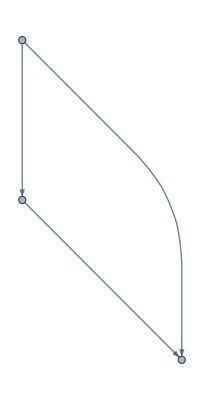

```mathematica
Graph[{1->2,1->3,2->3}]
```



```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeWeight->RandomInteger[5,3]]
```

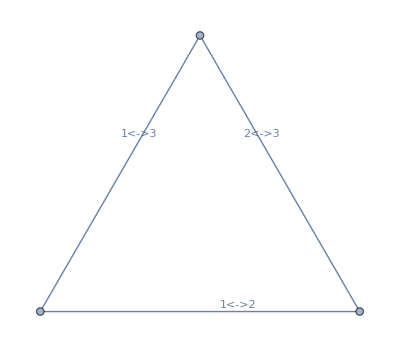

```mathematica
Show[SetProperty[Graph[{1, 2, 3}, {UndirectedEdge[1, 2], UndirectedEdge[2, 3], UndirectedEdge[3, 1]}, {EdgeWeight -> {0, 2, 3}}],EdgeLabels->Placed["Name",1./GoldenRatio]],PlotRange->All]
```

```mathematica
{
```

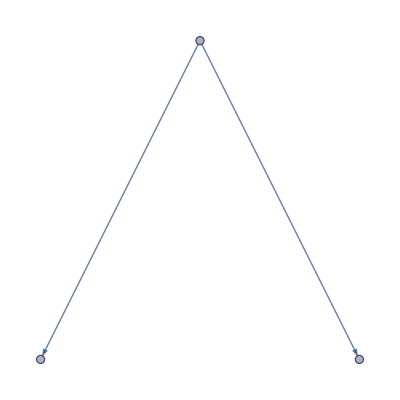

```mathematica
Graph[{3->7,3->4},EdgeWeight->{7, 4}]
```

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
Combinatorica`Dijkstra[Combinatorica`Graph[{3->7,3->4},Combinatorica`EdgeWeight->{7, 4}], {3, 4, 7}]
```

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

First::normal: Nonatomic expression expected at position 1 in First[All].

Rest::normal: Nonatomic expression expected at position 1 in Rest[All].

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Table::iterb: Iterator {Combinatorica`Private`i$34464,V[Graph[{3→7,3→4},EdgeWeight→{7,4}]]} does not have appropriate bounds.

Join::heads: Heads Combinatorica`Private`Double and Table at positions 1 and 2 are expected to be the same.

Rest::norest: Cannot take Rest of expression Combinatorica`Private`Double[] with length zero.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Rest::norest: Cannot take Rest of expression Table[] with length zero.

Rest::argx: Rest called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[All].

Rest::normal: Nonatomic expression expected at position 1 in Rest[All].

Table::iterb: Iterator {Combinatorica`Private`i$34498,V[Graph[{3→7,3→4},EdgeWeight→{7,4}]]} does not have appropriate bounds.

Join::heads: Heads Combinatorica`Private`Double and Table at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Rest::norest: Cannot take Rest of expression Combinatorica`Private`Double[] with length zero.

General::stop: Further output of Rest::norest will be suppressed during this calculation.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Rest::argx: Rest called with 2 arguments; 1 argument is expected.

First::normal: Nonatomic expression expected at position 1 in First[All].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[All].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Table::iterb: Iterator {Combinatorica`Private`i$34521,V[Graph[{3→7,3→4},EdgeWeight→{7,4}]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Table::argm will be suppressed during this calculation.

Rest::argx: Rest called with 2 arguments; 1 argument is expected.

General::stop: Further output of Rest::argx will be suppressed during this calculation.

{Dijkstra[Rest[Combinatorica`Private`Double[],Table[]],3],Dijkstra[Rest[Combinatorica`Private`Double[],Table[]],4],Dijkstra[Rest[Combinatorica`Private`Double[],Table[]],7]}